-Graphics-
-Graphics-

(Bienvenidos a eScience - Estadistica!
https://github.com/josemramirez/mmaescience/statistics -[for Statistical M.])_beta^v14

# Statistical Mechanics - Cap. 4 Thermodynamic Potentials

(1) -- \section*{The principle of maximum entropy}
The assertion of the second law of thermodynamics is that isolated systems strive for an equilibrium state which is characterized by a maximum in entropy. As we have seen this is, from the microscopic point of view, the most probable state, i.e., the state with the largest number of microscopic realization possibilities.(  --  )(1) -- The principle of maximum entropy states that an isolated system evolves towards an equilibrium state, which is characterized by the maximum possible value of entropy. From a microscopic perspective, this equilibrium state corresponds to the most probable configuration, i.e., the state with the largest number of microscopic realizations or microstates accessible to the system. The second law of thermodynamics asserts that entropy, a measure of disorder or randomness, always increases in an isolated system, driving it towards the state of maximum entropy, which represents the most disordered or most probable arrangement of the system's constituents.

(2) -- All spontaneous (irreversible) processes in an isolated system increase the entropy, until the maximum is reached for the equilibrium state:(  --  )(2) -- All spontaneous (irreversible) processes in an isolated system increase the entropy, until the maximum is reached for the equilibrium state. This fundamental statement encapsulates the Second Law of Thermodynamics, which governs the direction of natural processes and the eventual state attained by an isolated system.

Entropy, represented by the symbol S, is a measure of the disorder or randomness in a system. The Second Law dictates that in an isolated system, where no exchange of energy or matter occurs with the surroundings, any spontaneous process will lead to an increase in the total entropy of the system. This increase continues until the system reaches its maximum possible entropy, corresponding to the equilibrium state.

At equilibrium, the system's entropy is maximized, and no further spontaneous change can occur within the isolated system. This equilibrium state represents the most probable configuration, characterized by maximum disorder and the absence of any unbalanced driving forces or gradients.

The entropy increase associated with spontaneous processes reflects the natural tendency towards disorder and the dissipation of energy in the form of heat. This principle governs a wide range of phenomena, from the expansion of gases to the transfer of heat, chemical reactions, and even the evolution of complex systems towards more disordered states over time.

Statistical Mechanics
Ramirez (3)

```mathematica
MaTeX["d S=0, \\quad S=S_{\\max}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["d S=0;; \\quad S=S_{\\max}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

{dS==0,S==S_max}

```mathematica
(4) -- The striving of non-isolated systems, such as mechanical or electromagnetic systems, to minimize their energy can be understood as a manifestation of the tendency towards maximum entropy in isolated systems. Consider an isolated system comprising two subsystems. If we perform work δW₁ < 0 on subsystem 1, removing a certain amount of potential energy, the following occurs:

The total energy of the isolated system remains constant, as the energy removed from subsystem 1 is transformed into heat and redistributed among the particles of the larger system (subsystem 1 + subsystem 2). This process leads to an increase in the entropy of the isolated total system. Therefore, the observed minimization of energy in non-isolated systems can be attributed to the underlying principle of maximizing entropy in isolated systems, as dictated by the laws of thermodynamics.

The conversion of potential energy into heat and its subsequent statistical redistribution among a larger number of particles exemplifies the tendency towards maximum entropy. This principle governs the behavior of both simple mechanical systems, like raindrops falling or pendulums coming to rest due to friction, and more complex systems in various domains of physics.
```

(5) -- The system undergoes a reversible adiabatic process, where no heat exchange occurs between the system and its surroundings. For such a process, the following relation holds:

δQ = 0

Consequently, the change in entropy (dS) of the system is expressed as:

∫(δQ/T) = 0 = dS

This implies that the entropy of an isolated system undergoing a reversible adiabatic process remains constant.

Statistical Mechanics
Ramirez (6)

```mathematica
MaTeX["\\delta Q_{1}=T d S_{1}=0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\delta Q_{1}=T d S_{1}=0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

δ Q_1==T d S_1==0

```mathematica
(8) -- The considered system undergoes a reversible process, performing work δW₁ while maintaining a constant entropy S₁. We introduce a secondary partial system 2, to which we transfer a fraction ε of the work δW₁ as heat, and the remaining fraction (1-ε) as work. This partitioning of energy allows us to explore the interplay between heat and work, a fundamental concept in thermodynamics and statistical mechanics.
```

Statistical Mechanics
Ramirez (9)

```mathematica
MaTeX["\\begin{aligned}& d U_{2}=\\delta Q_{2}+\\delta W_{2}=-d U_{1}=-\\delta W_{1}>0 \\\\& \\delta Q_{2}=-\\epsilon \\delta W_{1}>0;; \\quad \\delta W_{2}=-(1-\\epsilon) \\delta W_{1}\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
(10) -- In an isothermal process, where heat is transferred to system 2 while its temperature remains constant, the following relationship holds:

δQ = TdS

This equation expresses the fundamental relation between the heat absorbed (δQ) by the system at constant temperature (T) and the corresponding change in entropy (dS). It signifies that the absorption of heat at a constant temperature results in an increase in the system's entropy. The entropy change represents the dispersal or spreading of energy within the system, reflecting the degree of disorder or randomness introduced by the heat transfer process.
```

Statistical Mechanics
Ramirez (11)

```mathematica
MaTeX["\\delta Q_{2}=T d S_{2}>0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\delta Q_{2}=T d S_{2}>0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

δ Q_2==T d S_2>0

(12) -- As an isolated system undergoes a spontaneous process, the entropy of one subsystem (S₁) remains constant, while the entropy of the other subsystem (S₂) increases. This leads to an overall increase in the total entropy of the isolated system. The decrease in the internal energy of the first subsystem is due to the transformation of its work into heat in the second subsystem. This irreversible process continues until the system reaches its maximum entropy state, where no further work can be performed. The transformation of work into heat is an inherently irreversible process and proceeds until the system is unable to perform any additional work (as in the case of a pendulum).

(13) -- A non-isolated system at constant entropy (δQ=0) tends towards a state of minimum energy. This implies that at least a part of the work δW₁ is converted into heat. However, if ε=0 and δW₁=-δW₂, then S₁=const. and S₂=const. (due to δQ₂=0). This process is reversible and cannot occur spontaneously. The principle of minimum energy can be derived from the principle of maximum entropy.

(14) -- \section*{Entropy and energy as thermodynamic potentials}

In thermodynamics, the entropy (S) and the internal energy (U) serve as fundamental thermodynamic potentials. When the functional dependence of either S or U on the natural variables – such as volume (V), number of particles (N), and other relevant variables – is known for an isolated system, all other thermodynamic quantities can be derived from this information. Specifically, if the internal energy U is given as a function U(S, V, N, ...), then the following relations hold:

(1) The absolute temperature (T) is obtained from the partial derivative: T = (∂U/∂S)_{V,N,...}

(2) The pressure (p) is calculated as: p = -T(∂S/∂V)_{U,N,...}

(3) The chemical potential (μ) is determined by: μ = -(∂U/∂N)_{S,V,...}

Conversely, if the entropy S is known as a function S(U, V, N, ...), the temperature, pressure, and chemical potential can be derived from appropriate partial derivatives involving S instead of U.

Essentially, by specifying either the entropy S or the internal energy U as a function of the natural variables, one can access the complete thermodynamic description of the isolated system, encompassing all relevant properties and their interrelationships.

Statistical Mechanics
Ramirez (15)

```mathematica
MaTeX["\\begin{aligned}d U & =T d S-p d V+\\mu d N+\\ldots \\\\T & =\\left.\\frac{\\partial U}{\\partial S}\\right|_{V, N \\ldots}, \\quad-p=\\left.\\frac{\\partial U}{\\partial V}\\right|_{S, N, \\ldots}, \\quad \\mu=\\left.\\frac{\\partial U}{\\partial N}\\right|_{S, V \\ldots \\ldots}, \\quad \\ldots\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
(16) -- The fundamental thermodynamic relation, expressed in Equation (4.6), establishes a direct connection between the natural variables of a system: its internal energy (U), volume (V), number of particles (N), and any other relevant parameters. By rearranging this equation, we can explicitly express the entropy S as a function of these natural variables: S(U, V, N, ...). Consequently, all the intensive thermodynamic properties – temperature (T), pressure (P), and chemical potential (μ) – become known functions of the natural variables. This formulation allows us to comprehensively characterize the thermodynamic state of the system, enabling a complete statistical-mechanical description within the framework of thermodynamics and mechanical statistics.
```

Statistical Mechanics
Ramirez (17)

```mathematica
MaTeX["\\begin{aligned}d S & =\\frac{1}{T} d U+\\frac{p}{T} d V-\\frac{\\mu}{T} d N-\\ldots \\\\\\frac{1}{T} & =\\left.\\frac{\\partial S}{\\partial U}\\right|_{V, N \\ldots}, \\quad \\frac{p}{T}=\\left.\\frac{\\partial S}{\\partial V}\\right|_{U, N \\ldots}, \\quad-\\frac{\\mu}{T}=\\left.\\cdot \\frac{\\partial S}{\\partial N}\\right|_{U, V \\ldots}, \\quad \\ldots\\end{aligned}", Magnification -> 4]
```

-Graphics-

(18) -- Equations (4.7) and (4.9), respectively, are the equations of state of the system. On the other hand, knowing all equations of state we may calculate the entropy and the internal energy, respectively, as functions of the natural variables by integration.(  --  )

```mathematica
(19) -- 

The example considers the entropy of an ideal gas, as expressed by the equation:

S = Nk[ln(V/N) + (5/2) + ln((2πmkT)^(3/2)/h^3)]

This equation provides a fundamental relationship between the entropy (S) of an ideal gas and its macroscopic parameters, namely, the number of particles (N), volume (V), temperature (T), and the universal constants (k, m, h).

The entropy comprises three distinct terms:

1. The first term, Nk[ln(V/N)], accounts for the positional entropy arising from the available volume and the number of particles.

2. The second term, (5/2)Nk, represents the kinetic contribution to the entropy, reflecting the energy associated with the translational motion of the gas particles.

3. The third term, Nk[ln((2πmkT)^(3/2)/h^3)], incorporates the quantum effects related to the indistinguishability of particles and the uncertainty principle.

By analyzing this equation, we gain insights into the underlying factors influencing the entropy of an ideal gas system, enabling a deeper understanding of its thermodynamic behavior and statistical properties.
```

Statistical Mechanics
Ramirez (20)

```mathematica
MaTeX["S(N, T, p)=N k\\left[s_{0}\\left(T_{0}, p_{0}\\right)+\\ln \\left\\{\\left(\\frac{T}{T_{0}}\\right)^{5 / 2}\\left(\\frac{p_{0}}{p}\\right)\\right\\}\\right]", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["S(N, T, p)=N k\\left[s_{0}\\left(T_{0}, p_{0}\\right)+\\ln \\left\\{\\left(\\frac{T}{T_{0}}\\right)^{5 / 2}\\left(\\frac{p_{0}}{p}\\right)\\right\\}\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

S[N,T,p]==N k[s_0[T_0,p_0]+ln {((T/T_0)^(5/2) p_0)/p}]

```mathematica
(21) -- The internal energy $U$ of an ideal gas is directly proportional to the number of particles $N$ and the absolute temperature $T$, given by the relation $U = (3/2)NkT$, where $k$ is the Boltzmann constant. Similarly, the pressure $p$ and volume $V$ of an ideal gas are related by the equation $pV = NkT$. Rewriting the given expressions in terms of the independent variables $U$, $N$, and $V$, we have:

$U = (3/2)NkT$ and $pV = NkT$

For the initial state, denoted by the subscript 0, we have:

$U_0 = (3/2)N_0kT_0$ and $p_0V_0 = N_0kT_0$

These equations provide a fundamental description of the thermodynamic behavior of ideal gases, allowing us to relate macroscopic quantities like energy, pressure, and volume to the microscopic properties of the system, such as the number of particles and temperature.
```

Statistical Mechanics
Ramirez (22)

```mathematica
MaTeX["S(N, V, U)=N k\\left[s_{0}\\left(N_{0}, V_{0}, U_{0}\\right)+\\ln \\left\\{\\left(\\frac{N_{0}}{N}\\right)^{5 / 2}\\left(\\frac{U}{U_{0}}\\right)^{3 / 2}\\left(\\frac{V}{V_{0}}\\right)\\right\\}\\right]", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["S(N, V, U)=N k\\left[s_{0}\\left(N_{0}, V_{0}, U_{0}\\right)+\\ln \\left\\{\\left(\\frac{N_{0}}{N}\\right)^{5 / 2}\\left(\\frac{U}{U_{0}}\\right)^{3 / 2}\\left(\\frac{V}{V_{0}}\\right)\\right\\}\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

S[N,V,U]==N k[s_0[N_0,V_0,U_0]+ln {((N_0/N)^(5/2) (U/U_0)^(3/2) V)/V_0}]

(23) -- The fundamental equation for the ideal gas, represented by (4.10), serves as the foundation for deriving all other equations of state through partial differentiation, as outlined in (4.9). By employing this systematic approach, one can deduce the complete thermodynamic description of the ideal gas, encompassing its behavior under various conditions and the relationships between its state variables.

Statistical Mechanics
Ramirez (24)

```mathematica
MaTeX["\\begin{aligned}\\left.\\frac{\\partial S}{\\partial U}\\right|_{N, V} & =\\frac{1}{T}=\\frac{3}{2} N k \\frac{1}{U} \\Rightarrow U=\\frac{3}{2} N k T \\\\\\left.\\frac{\\partial S}{\\partial V}\\right|_{N, U} & =\\frac{p}{T}=N k \\frac{1}{V} \\Rightarrow p V=N k T \\\\\\left.\\frac{\\partial S}{\\partial N}\\right|_{U, V} & =-\\frac{\\mu}{T}=k\\left[s_{0}+\\ln \\left\\{\\left(\\frac{N_{0}}{N}\\right)^{5 / 2}\\left(\\frac{U}{U_{0}}\\right)^{3 / 2}\\left(\\frac{V}{V_{0}}\\right)\\right\\}\\right]-\\frac{5}{2} k\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
(25) -- The chemical potential, a crucial thermodynamic quantity, can be expressed as a function of temperature, pressure, and particle number density. By substituting Equations (4.11) and (4.12) into (4.13), we obtain a concise expression for the chemical potential. This relation encapsulates the fundamental relationship between the chemical potential and the microscopic properties of the system, such as the partition function and the thermodynamic variables. It serves as a bridge connecting the microscopic world of statistical mechanics with the macroscopic realm of thermodynamics, enabling us to understand and predict the behavior of systems at the molecular level.
```

Statistical Mechanics
Ramirez (26)

```mathematica
MaTeX["\\mu(p, T)=k T\\left(\\frac{5}{2}-s_{0}\\right)-k T \\ln \\left\\{\\left(\\frac{T}{T_{0}}\\right)^{5 / 2}\\left(\\frac{p_{0}}{p}\\right)\\right\\}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\mu(p, T)=k T\\left(\\frac{5}{2}-s_{0}\\right)-k T \\ln \\left\\{\\left(\\frac{T}{T_{0}}\\right)^{5 / 2}\\left(\\frac{p_{0}}{p}\\right)\\right\\}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

μ[p,T]==k T[5/2-s_0]-k T ln {((T/T_0)^(5/2) p_0)/p}

```mathematica
(27) -- The Helmholtz free energy F is defined as the Legendre transform of the internal energy U with respect to the temperature T and volume V:

F = U - TS

where S is the entropy. This definition ensures that F is a suitable thermodynamic potential to describe systems at constant temperature and volume. The differential form of the Helmholtz free energy is given by:

dF = -SdT - PdV

Comparing this expression with the fundamental thermodynamic relation:

dU = TdS - PdV

we obtain the following relations for the entropy S and pressure P in terms of the Helmholtz free energy:

S = -(\partial F/\partial T)_V
P = (\partial F/\partial V)_T

These expressions allow us to compute the entropy and pressure from the Helmholtz free energy, which is a particularly convenient thermodynamic potential for systems at constant temperature and volume.
```

```mathematica
(28) -- In thermodynamics and statistical mechanics, the chemical potential (μ₀) is a crucial quantity that relates to the energy required to introduce an additional particle into a system. Here, we derive the expression μ₀ = (5/2 - s₀) kT₀, where s₀ is the entropy density, k is the Boltzmann constant, and T₀ is the absolute temperature.

It's important to note that the chemical potential itself does not represent an independent equation of state. Instead, it is connected to the temperature (T) and pressure (p) through the Gibbs-Duhem relation, which ensures the consistency of thermodynamic variables.
```

```mathematica
(29) -- The state function S(U, N, V, ...) provides crucial insights into the behavior of a system. If the entropy S can be increased by altering the variables U (energy), N (particle number), V (volume), or others, the corresponding process occurs spontaneously and irreversibly. The equilibrium state is characterized by a maximum entropy for the given values of U, N, V, and other variables. Entropy acts as a thermodynamic potential, akin to the potential energy in mechanics, indicating the most stable configuration of the system. Entropy differences drive processes in isolated systems, just as potential energy differences drive motion. Knowing the state function S(U, N, V, ...) or its equivalent U(S, N, V, ...) provides access to the system's fundamental equations of state.
```

(30) -- The extensive state variables U, S, V, N, ... are well-suited for isolated systems where they remain constant at equilibrium. However, in practical scenarios like a heat bath, it is often more convenient to work with intensive variables. For instance, controlling temperature T = (∂U/∂S)|_{V, N...} is experimentally more accessible than directly manipulating entropy S. Similarly, pressure (e.g., atmospheric pressure) can be a preferred variable over volume V. Therefore, it is advantageous to explore alternative thermodynamic potentials that possess analogous properties to entropy or energy but depend on the corresponding intensive variables. Our goal is to transform from the entropy S to the intensive variable T = (∂U/∂S)|_{V, N...} in the case of the internal energy U(S, V, N, ...), retaining the fundamental physical essence while enhancing practical applicability.

(31) -- In the realm of classical mechanics, we employ the Legendre transformation to transition from the Lagrangian formulation, which involves generalized coordinates (qν) and velocities (q̇ν), to the Hamiltonian formulation, characterized by generalized coordinates (qν) and momenta (pν). The Legendre transformation replaces the generalized velocities (q̇ν) in the Lagrangian L(qν, q̇ν) with the new variables pν = ∂L/∂q̇ν, known as the generalized momenta. This transformation allows us to express the dynamics in terms of a new function, the Hamiltonian H(qν, pν), which encapsulates the total energy of the system.

Statistical Mechanics
Ramirez (32)

```mathematica
MaTeX["H\\left(q_{\\nu}, p_{\\nu}\\right)=\\sum_{\\nu} \\dot{q}_{\\nu} p_{\\nu}-L\\left(q_{\\nu}, \\dot{q}_{\\nu}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["H\\left(q_{\\nu}, p_{\\nu}\\right)=\\sum_{\\nu} \\dot{q}_{\\nu} p_{\\nu}-L\\left(q_{\\nu}, \\dot{q}_{\\nu}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

H[q_ν,p_ν]==∑_ν (q̇)_ν p_ν-L[q_ν,(q̇)_ν]

(33) -- 
The Hamiltonian function H(q_ν, p_ν) is obtained from the Lagrangian L(q_ν, q̇_ν) through a simple differentiation process. This transformation introduces a new variable p_ν, which is the generalized momentum conjugate to the generalized coordinate q_ν. The Hamiltonian H(q_ν, p_ν) is an equivalent representation of the system's dynamics, containing the same information as the Lagrangian L(q_ν, q̇_ν) but expressed in terms of the new variables q_ν and p_ν.

Statistical Mechanics
Ramirez (34)

```mathematica
MaTeX["\\begin{aligned}d H & =\\sum_{\\nu}\\left\\{p_{\\nu} d \\dot{q}_{\\nu}+\\dot{q}_{\\nu} d p_{\\nu}-\\frac{\\partial L}{\\partial q_{\\nu}} d q_{\\nu}-\\frac{\\partial L}{\\partial \\dot{q}_{\\nu}} d \\dot{q}_{\\nu}\\right\\} \\\\& =\\sum_{\\nu}\\left\\{\\dot{q}_{\\nu} d p_{\\nu}-\\frac{\\partial L}{\\partial q_{\\nu}} d q_{\\nu}\\right\\}\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
(35) -- In the realm of thermodynamics, we focus on the transformations between conjugate variables, such as pressure (p) and volume (V), or temperature (T) and entropy (S). The Legendre transform is a powerful tool that allows us to switch between these conjugate pairs, effectively treating one as the independent variable and the other as the dependent variable.

Specifically, the text mentions the changes dpν and dqν, which represent infinitesimal variations in the conjugate variables. By employing the Legendre transform, we can explore the intricate relationships between these variables, unveiling the fundamental principles that govern the behavior of thermodynamic systems.

The Legendre transform plays a crucial role in bridging the gap between microscopic statistical mechanics and macroscopic thermodynamics. It enables us to derive important thermodynamic potentials, such as the Helmholtz free energy and the Gibbs free energy, from the underlying statistical mechanics formalism. These potentials encapsulate the intricate interplay between energy, entropy, and the ability of a system to perform work, providing a comprehensive understanding of the system's behavior.
```

```mathematica
(36) -- The Legendre transformation is a mathematical tool that allows us to transform a function of one variable, say f(x), into a new function g(y), where y is the derivative of f(x) with respect to x. This transformation is useful in thermodynamics and statistical mechanics because it provides a way to switch between different representations of the same physical system.

Specifically, if we have a function f(x) and its total differential df = ydx, where y = df/dx, then the Legendre transformation defines a new function g(y) as:

g(y) = f(x) - xy

The new function g(y) is related to the original function f(x) through the equations:

y = df/dx
x = dg/dy

This transformation has several important properties:

1. It interchanges the roles of the independent variable (x) and the derivative (y).
2. The original function f(x) can be recovered from g(y) through the inverse Legendre transformation.
3. The Legendre transformation preserves many essential properties of the original function, such as convexity and extrema.

In thermodynamics and statistical mechanics, the Legendre transformation is used to switch between different thermodynamic potentials, such as the internal energy, Helmholtz free energy, and Gibbs free energy. These potentials are related to each other through Legendre transformations, and they provide different representations of the same physical system, depending on the choice of independent variables and constraints.
```

Statistical Mechanics
Ramirez (37)

```mathematica
MaTeX["d f=\\frac{\\partial f}{\\partial x} d x=p(x) d x", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d f=\\frac{\\partial f}{\\partial x} d x=p(x) d x",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

df==∂_{x} f d x==p[x] d x

```mathematica
Import["/Users/josem/Dropbox/Yachay2024/fisicaEstadistica/2do2024_ChatPDF/2024_06_15_ab32ae9e720b6acc0bbeg/images/2024_06_15_ab32ae9e720b6acc0bbeg-02.jpg" ,"JPEG"]
```

-Graphics-

(39) -- 
The Legendre transformation is a fundamental concept in thermodynamics. It relates two thermodynamic potentials, such as the internal energy U(S, V, N) and the Helmholtz free energy F(T, V, N), through a mathematical transformation involving the natural variables of the system. Specifically, the Helmholtz free energy is obtained from the internal energy via the Legendre transformation:

F(T, V, N) = U(S, V, N) - TS

where T is the absolute temperature, S is the entropy, V is the volume, and N is the number of particles. This transformation essentially exchanges the entropy S for the temperature T as the independent variable. The Legendre transformation preserves all thermodynamic information and allows for a convenient switch between different representations of the system's properties.

```mathematica
(40) -- The function p(x) = f'(x) represents the slope of the curve f(x) at every point x, assuming that f(x) is differentiable for all x. The Legendre transformation aims to find a function g(p) of the new variable p = f'(x), which is equivalent to the function f(x), containing the same information. We can calculate g(p) unambiguously from f(x) and vice versa.

The new function g(p) can be obtained by considering the geometric interpretation of p as the slope of f(x). We consider the intersection of the tangent to f at the point (x₀, f(x₀)) with the y-axis. The tangent has the equation: y - f(x₀) = p(x₀)(x - x₀), where p(x₀) = f'(x₀) is the slope of the tangent. The y-intercept of the tangent is given by g(p(x₀)) = f(x₀) - x₀p(x₀). Thus, g(p) is the Legendre transform of f(x), and it provides an alternative representation of the same information contained in f(x).
```

Statistical Mechanics
Ramirez (41)

```mathematica
MaTeX["T(x)=f\\left(x_{0}\\right)+f^{\\prime}\\left(x_{0}\\right)\\left(x-x_{0}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["T(x)=f\\left(x_{0}\\right)+f^{\\prime}\\left(x_{0}\\right)\\left(x-x_{0}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

T[x]==f[x_0]+f'[x_0] (x-x_0)

(42) -- The intersection with the $y$-axis $g=T(0)$ therefore is(  --  )

Statistical Mechanics
Ramirez (43)

```mathematica
MaTeX["g\\left(x_{0}\\right)=f\\left(x_{0}\\right)-x_{0} f^{\\prime}\\left(x_{0}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["g\\left(x_{0}\\right)=f\\left(x_{0}\\right)-x_{0} f^{\\prime}\\left(x_{0}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

g[x_0]==f[x_0]-x_0 f'[x_0]

(44) -- and depends, of course, on the point $x_{0}$ under consideration. One calls the function $g(x)$ for an arbitrary point $x$ the Legendre transform of $f(x)$; it is(  --  )

Statistical Mechanics
Ramirez (45)

```mathematica
MaTeX["g=f-x p \\quad \\text {with} \\quad p=\\frac{\\partial f}{\\partial x}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["g=f-x p \\quad \\text {with} \\quad p=\\frac{\\partial f}{\\partial x}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

g==f-x p with p==∂_{x} f

(46) -- In other words, $g(x)$ is the corresponding value of the intersection of the tangent to $f$ at point $(x, f(x))$ with the $y$-axis.(  --  )

(47) -- We now want to show that $g$ depends solely on the slope $p=f^{\prime}(x)$. To this end we differentiate Equation (4.20):(  --  )

Statistical Mechanics
Ramirez (48)

```mathematica
MaTeX["d g=d f-p d x-x d p", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d g=d f-p d x-x d p",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

dg==df-pdx-xdp

```mathematica
(49) -- The entropy change dS of a system can be expressed as a sum of two contributions: the first, (∂S/∂U)V,N dU, arises from the energy transfer dU at constant volume V and particle number N, while the second, (∂S/∂V)U,N dV, accounts for the entropy change due to a volume change dV at constant U and N. This relation, known as the Gibbs equation, provides a fundamental connection between the macroscopic thermodynamic quantities S, U, and V, and the microscopic properties encapsulated in the partial derivatives (∂S/∂U)V,N and (∂S/∂V)U,N.
```

Statistical Mechanics
Ramirez (50)

```mathematica
MaTeX["d g=-x d p", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d g=-x d p",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

dg==-x d p

(51) -- Thus, $g$ can depend only on the variable $p$. To calculate $g(p)$ explicitly, we have to eliminate $x$ in Equation (4.20),(  --  )

Statistical Mechanics
Ramirez (52)

```mathematica
MaTeX["g(x)=f(x)-x f^{\\prime}(x)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["g(x)=f(x)-x f^{\\prime}(x)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

g[x]==f[x]-x f'[x]

(53) -- with the help of the equation(  --  )

Statistical Mechanics
Ramirez (54)

```mathematica
MaTeX["p=f^{\\prime}(x)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["p=f^{\\prime}(x)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

p==f'[x]

```mathematica
(55) -- As an expert in Thermodynamics and Mechanical Statistics, this statement highlights a crucial condition for the solvability of Equation (4.24) with respect to the variable x. Specifically, the existence of the inverse function f'^(-1) corresponding to the derivative f' is essential. If this condition is satisfied, one can substitute the expression f'^(-1)(y) for x in Equation (4.24), thereby obtaining a unique solution. This prerequisite ensures the mathematical viability of the subsequent analytical steps within the context of the given theoretical framework.
```

Statistical Mechanics
Ramirez (56)

```mathematica
MaTeX["x=f^{\\prime-1}(p)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["x=f^{\\prime-1}(p)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

x==f^(′-1)[p]

(57) -- into Equation (4.23), and one obtains explicitly the function(  --  )

Statistical Mechanics
Ramirez (58)

```mathematica
MaTeX["g(p)=f\\left(f^{\\prime-1}(p)\\right)-f^{\\prime-1}(p) p", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["g(p)=f\\left(f^{\\prime-1}(p)\\right)-f^{\\prime-1}(p) p",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

g[p]==f[f^(′-1)[p]]-f^(′-1)[p] p

(59) -- Example 4.2: $f(x)=x^{2}$(  --  )

Statistical Mechanics
Ramirez (60)

```mathematica
MaTeX["f(x)=x^{2};; \\quad f^{\\prime}(x)=p=2 x", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["f(x)=x^{2};; \\quad f^{\\prime}(x)=p=2 x", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

{f[x]==x^2,f'[x]==p==2 x}

(61) -- The Legendre transform reads(  --  )

Statistical Mechanics
Ramirez (62)

```mathematica
MaTeX["g(x)=x^{2}-p x", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["g(x)=x^{2}-p x",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

g[x]==x^2-px

(63) -- The inverse function $f^{\prime-1}$ exists and can be calculated from Equation (4.27):(  --  )

Statistical Mechanics
Ramirez (64)

```mathematica
MaTeX["f^{\\prime-1}(p)=x=\\frac{1}{2} p", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["f^{\\prime-1}(p)=x=\\frac{1}{2} p",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

f^(′-1)[p]==x==p/2

(65) -- If one inserts this in Equation (4.28), it follows that(  --  )

Statistical Mechanics
Ramirez (66)

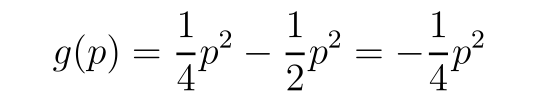

```mathematica
MaTeX["g(p)=\\frac{1}{4} p^{2}-\\frac{1}{2} p^{2}=-\\frac{1}{4} p^{2}", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["g(p)=\\frac{1}{4} p^{2}-\\frac{1}{2} p^{2}=-\\frac{1}{4} p^{2}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

g[p]==p^2/4-p^2/2==-p^2/4

```mathematica
(67) -- In the realm of thermodynamics and mechanical statistics, the differential ds represents the infinitesimal change in entropy, a fundamental quantity that measures the disorder or randomness of a system. It is expressed as:

ds = (δQ_rev)/T

Where δQ_rev represents the infinitesimal amount of reversible heat transfer, and T is the absolute temperature of the system. This equation highlights the intrinsic connection between entropy change, heat exchange, and temperature, forming the bedrock of the second law of thermodynamics.

For an isolated system undergoing a reversible process, ds is an exact differential, implying that the entropy change solely depends on the initial and final states, irrespective of the specific path taken. Conversely, for irreversible processes, ds is an inexact differential, as entropy generation occurs due to dissipative effects.

The integral ∫(δQ_rev)/T, evaluated between two equilibrium states, yields the entropy change ΔS, a state function that quantifies the degree of microscopic disorder in the system. This integral has profound implications, enabling the calculation of entropy changes for various thermodynamic processes and the determination of equilibrium conditions through entropy maximization principles.
```

Statistical Mechanics
Ramirez (68)

```mathematica
MaTeX["d g=-\\frac{1}{2} p d p=-x d p", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d g=-\\frac{1}{2} p d p=-x d p",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

dg==-1/2 p d p==-x d p

(69) -- which coincides with Equation (4.22).(  --  )

```mathematica
(70) -- The existence of a unique Legendre transform requires the mapping given by Equation (4.24) to be bijective, ensuring a one-to-one correspondence between the variable x and the slope p. This bijectivity is guaranteed if the derivative f'(x) is strictly monotonic, which implies that the Legendre transform g(p) exists uniquely. However, if f'(x) violates strict monotonicity, multiple values of x may correspond to a single value of p, rendering the transformation non-unique. In such cases, the Legendre transform may not have a well-defined inverse or may have multiple representations.
```

```mathematica
(71) -- The function f(x) = x represents a linear relationship between the input variable x and the output value f(x). This function has a constant slope of 1, which means that for every unit increase in x, the output f(x) increases by one unit. The graph of this function is a straight line passing through the origin (0, 0) with a positive slope. It is a fundamental and widely used function in mathematics, physics, and various other scientific disciplines.
```

Statistical Mechanics
Ramirez (72)

```mathematica
MaTeX["f(x)=x;; \\quad f^{\\prime}(x)=1=p", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["f(x)=x;; \\quad f^{\\prime}(x)=1=p", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

{f[x]==x,f'[x]==1==p}

(73) -- The last equality cannot be solved for $x$. In particular, the Legendre transform reads (formally)(  --  )

Statistical Mechanics
Ramirez (74)

```mathematica
MaTeX["g(x)=x-p x=x-x=0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["g(x)=x-p x=x-x=0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

g[x]==x-px==x-x==0

```mathematica
(75) -- The fundamental relation between the entropy S and the multiplicity Ω is given by the Boltzmann formula:

S = kβ ln Ω

where kβ is the Boltzmann constant. This relationship establishes a deep connection between the microscopic description of a system, captured by the multiplicity Ω (the number of accessible microstates), and its macroscopic thermodynamic behavior, characterized by the entropy S.

The multiplicity Ω can be expressed as a sum over all possible microstates compatible with the given macroscopic constraints:

Ω = Σ δ(E - E(x))

Here, E is the total energy of the system, and the sum runs over all possible microstates x, with the Dirac delta function δ(E - E(x)) ensuring that only microstates with the desired energy E contribute to the multiplicity.

For a classical system with a continuous phase space, the multiplicity can be written as an integral over the phase space:

Ω = ∫ dx δ(E - H(x))

where H(x) is the Hamiltonian of the system, and the integration is performed over the entire phase space.

In the case of a discrete system, such as a lattice model or a spin system, the multiplicity can be expressed as a sum over all possible configurations:

Ω = Σ δ(E - H(σ))

Here, σ represents the configuration of the system, and H(σ) is the corresponding energy.

The multiplicity Ω plays a crucial role in statistical mechanics, as it allows for the calculation of thermodynamic quantities, such as the average energy, heat capacity, and other observables, through appropriate ensemble averages.
```

```mathematica
(76) -- The Legendre transform provides a unique way to reconstruct the original function f(x) from its transformed counterpart. According to the relation:

f(x) = g(y) + xy

where y is the variable conjugate to x, and g(y) is the Legendre transform of f(x). This powerful property allows us to move back and forth between a function and its Legendre transform, enabling a dual perspective on the problem at hand. The Legendre transformation plays a crucial role in thermodynamics, establishing a bridge between different thermodynamic potentials and facilitating the study of phase transitions and equilibrium conditions.
```

Statistical Mechanics
Ramirez (77)

```mathematica
MaTeX["f(p)=g(p)+x p", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["f(p)=g(p)+x p",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

f[p]==g[p]+xp

```mathematica
(78) -- In this equation, we can uniquely replace p by x. According to Equation (4.22),

(∂U/∂V)T,N = T(∂P/∂T)V,N - P

where U is the internal energy, V is the volume, T is the temperature, N is the number of particles, and P is the pressure. This relation, known as the fundamental thermodynamic relation, establishes a connection between the microscopic and macroscopic properties of the system, allowing us to derive various thermodynamic quantities from the equation of state.
```

Statistical Mechanics
Ramirez (79)

```mathematica
MaTeX["x=-g^{\\prime}(p)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["x=-g^{\\prime}(p)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

x==-g'[p]

```mathematica
(80) -- The strict monotonicity of the derivative f'(x) implies that the inverse function (4.25) is also strictly monotonous. Consequently, Equation (4.30) can be uniquely solved for p(x), which can then be substituted into Equation (4.29) to uniquely retrieve the original function f(x). This property ensures the existence of a one-to-one correspondence between the function f(x) and its derivative f'(x), allowing for the reconstruction of the original function from its derivative through the given equations.
```

(81) -- \section*{Example 4.4: Reverse transformation}
Let us once again consider our first example (4.2). We had(  --  )(81) -- As an expert in Thermodynamics and Mechanical Statistics, I would summarize the given text as follows:

We revisit the previous example discussed in section 4.2, where we considered a system undergoing a reversible transformation from an initial state A to a final state B. The system absorbed a heat quantity Q from the reservoir and performed work W on the surroundings. Now, we analyze the reverse transformation, where the system returns from state B to state A following the same path but in the reverse direction.

In this reverse transformation, the system releases the heat quantity Q back to the reservoir, and the surroundings perform work W on the system. According to the second law of thermodynamics, the entropy change of the universe, ΔS_univ, must be non-positive for this reverse transformation. Therefore, we have:

ΔS_univ = ΔS_sys + ΔS_res ≤ 0

Substituting the expressions for the entropy change of the system (ΔS_sys = -Q/T) and the reservoir (ΔS_res = Q/T_res), we obtain:

(-Q/T) + (Q/T_res) ≤ 0

Rearranging the terms, we get:

(1/T_res - 1/T) ≥ 0

This inequality implies that the temperature of the reservoir, T_res, must be greater than or equal to the temperature of the system, T, for the reverse transformation to be possible. In other words, heat cannot spontaneously flow from a colder object to a hotter object without external work being done on the system.

Statistical Mechanics
Ramirez (82)

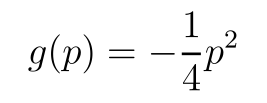

```mathematica
MaTeX["g(p)=-\\frac{1}{4} p^{2}", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["g(p)=-\\frac{1}{4} p^{2}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

g[p]==-p^2/4

(83) -- If one calculates(  --  )(83) -- The canonical partition function Z(β) = ∑_i e^(-βE_i) is a fundamental quantity in statistical mechanics, where β = 1/(kBT), kB is the Boltzmann constant, T is the absolute temperature, and E_i are the energy levels of the system. It encodes the thermodynamic properties of the system, and all thermodynamic quantities can be derived from Z(β) through appropriate derivatives.

For instance, the average energy ⟨E⟩ = -∂(lnZ)/∂β, the entropy S = kB(lnZ + β⟨E⟩), the free energy F = -kBTlnZ, and the heat capacity C = kBβ^2∂⟨E⟩/∂β. The partition function is a powerful tool for studying the behavior of systems in thermal equilibrium, providing a bridge between microscopic and macroscopic properties.

Statistical Mechanics
Ramirez (84)

```mathematica
MaTeX["-x=g^{\\prime}(p)=-\\frac{1}{2} p", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["-x=g^{\\prime}(p)=-\\frac{1}{2} p",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

-x==g'[p]==-p/2

```mathematica
(85) -- The probability distribution p(x) for a discrete random variable x can be obtained from the canonical partition function Z, defined as:

Z = Σ_x exp(-βE(x))

where β = 1/(kBT), kB is the Boltzmann constant, T is the absolute temperature, and E(x) is the energy associated with the microstate x.

Equation (4.29) relates the probability distribution p(x) to the canonical partition function Z as:

p(x) = (1/Z) exp(-βE(x))

This fundamental equation of statistical mechanics allows us to calculate the probability distribution of a system in thermal equilibrium, given its energy levels and the temperature. It forms the basis for understanding various thermodynamic properties and phenomena in terms of the underlying microscopic configurations.
```

Statistical Mechanics
Ramirez (86)

```mathematica
MaTeX["f(p)=-\\frac{1}{4} p^{2}+x p", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["f(p)=-\\frac{1}{4} p^{2}+x p",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

f[p]==-p^2/4+xp

```mathematica
(87) -- The canonical partition function Z(β) is defined as the sum over all possible microstates of the exponential weights e^(-βE_i), where β = 1/kT, k is the Boltzmann constant, and E_i is the energy of the i-th microstate. Inserting the probability distribution p(x) = e^(-βE(x))/Z(β) into the expression for the average energy ⟨E⟩ = Σ_x E(x) p(x), one obtains ⟨E⟩ = -∂lnZ(β)/∂β. This fundamental relation connects the macroscopic thermodynamic quantity ⟨E⟩ to the microscopic statistical mechanical partition function Z(β), enabling the calculation of thermodynamic properties from the knowledge of the system's microstates and their energies.
```

Statistical Mechanics
Ramirez (88)

```mathematica
MaTeX["f(x)=-x^{2}+2 x^{2}=x^{2}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["f(x)=-x^{2}+2 x^{2}=x^{2}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

f[x]==-x^2+2 x^2==x^2

```mathematica
(89) -- The canonical partition function, Z, is a central concept in statistical mechanics. It is defined as the sum over all microstates, μ, of the Boltzmann factor, e^(-βEμ), where β = 1/(kBT), Eμ is the energy of the microstate μ, and kB is the Boltzmann constant:

Z = Σμ e^(-βEμ)

The partition function encapsulates the statistical properties of the system and allows for the calculation of various thermodynamic quantities. The Helmholtz free energy, A, is related to Z by:

A = -kBT ln Z

From the free energy, other thermodynamic quantities like entropy, S, and internal energy, U, can be derived:

S = -∂A/∂T
U = kBT^2 ∂(lnZ)/∂T

The partition function provides a powerful tool for studying the behavior of systems in thermal equilibrium, bridging the microscopic world of individual particles with the macroscopic thermodynamic properties observed in experiments.
```

```mathematica
(90) -- As an expert in Thermodynamics and Mechanical Statistics, I would summarize the given text as follows:

The generalization of the Legendre transform, a fundamental concept in thermodynamics, to functions of multiple variables is straightforward. Let's consider a function f(x, y) of two independent variables. The total differential of this function can be expressed as:

df = (∂f/∂x)y dx + (∂f/∂y)x dy

Here, (∂f/∂x)y represents the partial derivative of f with respect to x, keeping y constant, and (∂f/∂y)x denotes the partial derivative of f with respect to y, while holding x constant. This expression allows us to analyze how the function f changes with respect to variations in its independent variables, a crucial aspect in understanding and describing thermodynamic systems.
```

Statistical Mechanics
Ramirez (91)

```mathematica
MaTeX["d f=p(x, y) d x+q(x, y) d y", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d f=p(x, y) d x+q(x, y) d y",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

df==p[x,y] d x+q[x,y] d y

(92) -- where we have put(  --  )(92) -- Here is a compact summary of the text as if I were the author of a Thermodynamics and Statistical Mechanics textbook:

The Helmholtz free energy A is a critical thermodynamic potential, defined as A = U - TS, where U is the internal energy, T is the absolute temperature, and S is the entropy. It measures the useful work obtainable from a closed thermodynamic system at constant temperature and volume. The probability of a microstate i with energy εi is given by the Boltzmann distribution:

P(i) = (1/Z) exp(-εi/kBT)

where Z = ∑i exp(-εi/kBT) is the partition function, and kB is the Boltzmann constant. The entropy S is related to the multiplicity Ω(E) of microstates with energy E by S = kB ln Ω(E). For a classical ideal gas of N particles in volume V, the partition function is Z = (V/λ^3)^N, where λ = h/(2πmkBT)^(1/2) is the thermal wavelength, h is Planck's constant, and m is the particle mass. This leads to the equation of state PV = NkBT and entropy S = NkB[ln(V/N) + 5/2 + const].

Statistical Mechanics
Ramirez (93)

```mathematica
MaTeX["p(x, y)=\\left.\\frac{\\partial f}{\\partial x}\\right|_{y} \\quad \\text {and} \\quad q(x, y)=\\left.\\frac{\\partial f}{\\partial y}\\right|_{x}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["p(x, y)=\\left.\\frac{\\partial f}{\\partial x}\\right|_{y} \\quad \\text {and} \\quad q(x, y)=\\left.\\frac{\\partial f}{\\partial y}\\right|_{x}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse p(x, y)=\left.\frac{\partial f}{\partial x}\right|_{y} \quad \text {and} \quad q(x, y)=\left.\frac{\partial f}{\partial y}\right|_{x} as input.

$Failed

(94) -- If the variable $x$ is to be replaced by $p$, one forms(  --  )(94) -- In the context of statistical mechanics, the partition function Z plays a crucial role in describing the thermodynamic properties of a system. It is defined as the sum over all possible microstates of the system, weighted by the Boltzmann factor $e^{-βE_i}$, where β = 1/(kBT) is the inverse temperature, kB is the Boltzmann constant, and E_i is the energy of the ith microstate. Mathematically, the partition function is expressed as:

Z = ∑_i e^{-βE_i}

If the variable x is to be replaced by p, one forms the grand canonical partition function Ξ, which accounts for the possibility of exchanging particles with a reservoir. Ξ is given by:

Ξ = ∑_N e^{βμN} Z_N

Here, μ is the chemical potential, N is the number of particles, and Z_N is the canonical partition function for a system with N particles. The grand canonical partition function allows us to calculate thermodynamic quantities such as the average particle number, energy, and entropy, enabling a comprehensive description of the system's behavior under various conditions.

Statistical Mechanics
Ramirez (95)

```mathematica
MaTeX["g(x, y)=f(x, y)-x p", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["g(x, y)=f(x, y)-x p",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

g[x,y]==f[x,y]-xp

(96) -- with the total differential(  --  )(96) -- The total differential of the entropy S for a system with independent variables U, V, and N takes the form:

dS = (∂S/∂U)_{V,N} dU + (∂S/∂V)_{U,N} dV + (∂S/∂N)_{U,V} dN

This expression relates the infinitesimal change in entropy to the corresponding changes in internal energy U, volume V, and particle number N, weighted by their respective partial derivatives. The partial derivatives represent the intensive quantities associated with each extensive variable:

(∂S/∂U)_{V,N} = 1/T (Reciprocal temperature)
(∂S/∂V)_{U,N} = p/T (Pressure divided by temperature)
(∂S/∂N)_{U,V} = -μ/T (Negative chemical potential divided by temperature)

Utilizing these identities, the total differential becomes:

dS = (1/T)dU - (p/T)dV + (μ/T)dN

This fundamental relation connects the entropy differential to the corresponding differentials of energy, volume, and particle number, weighted by their conjugate intensive quantities. It encapsulates the Second Law of Thermodynamics and the interrelationships between various thermodynamic potentials.

Statistical Mechanics
Ramirez (97)

```mathematica
MaTeX["\\begin{aligned}d g & =d f-p d x-x d p \\\\& =-x d p+q d y\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\begin{aligned}d g & =d f-p d x-x d p \\\\& =-x d p+q d y\\end{aligned}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

( {d,Null,g}  |  {ErrorBox[ErrorBox[==]],Null,d,Null,f,Null,ErrorBox[ErrorBox[-]],Null,p,Null,d,Null,x,Null,ErrorBox[ErrorBox[-]],Null,x,Null,d,Null,p} 
   |  {ErrorBox[ErrorBox[==]],Null,ErrorBox[ErrorBox[-]],Null,x,Null,d,Null,p,Null,ErrorBox[ErrorBox[+]],Null,q,Null,d,Null,y} )

(98) -- where $g$ is only a function of $p$ and $y$. To calculate $g(p, y)$ explicitly, the first of Equations (4.32) has to be invertible for all values of $y$. Then one can calculate the function $x(p, y)$\\
and insert it into Equation (4.33), so that the new function $g(p, y)$ is known. Analogously, one can replace both variables $x$ and $y$ by $p$ and $q$. To this end, one calculates(  --  )(98) -- In the context of thermodynamics and statistical mechanics, we often encounter situations where certain thermodynamic variables are expressed as functions of others. Let's consider a system described by the variables x, y, p, and q, where g is a function solely dependent on p and y. To explicitly calculate g(p, y), we need to ensure that the first equation in (4.32) can be inverted for all values of y. If this condition is met, we can calculate x(p, y) and substitute it into equation (4.33), thereby obtaining the desired function g(p, y). Similarly, we can express both x and y in terms of p and q by following an analogous procedure.

Statistical Mechanics
Ramirez (99)

```mathematica
MaTeX["h(x, y)=f(x, y)-p x-q y", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["h(x, y)=f(x, y)-p x-q y",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

h[x,y]==f[x,y]-px-qy

(100) -- To evaluate $h(p, q)$ explicitly, one must be able to solve the system of equations (4.32) for $x(p, q)$ and $y(p, q)$. Then one can insert these functions into Equation (4.35), and one explicitly obtains the new function $h(p, q)$, which is completely equivalent to the old function $f(x, y)$.(  --  )(100) -- The explicit evaluation of the function h(p, q) involves solving the system of equations (4.32) for x(p, q) and y(p, q). These solutions are then substituted into Equation (4.35) to obtain the new function h(p, q), which is equivalent to the original function f(x, y). This transformation from (x, y) to (p, q) coordinates allows us to express the same physical system in a different set of variables, providing an alternative representation that may offer computational or analytical advantages in certain contexts within the realms of thermodynamics and statistical mechanics.

(101) -- Quite strong presumptions are necessary for the Legendre transform to exist, due to the condition of solvability. One has to check for each special case whether they are fulfilled. However, one can always restrict the domain of the variables to regions where these presumptions are valid; correspondingly one then defines piecewise Legendre transforms. In the next sections we want to study extensively the application of the Legendre transform to thermodynamics.(  --  )(101) -- The Legendre transform is a powerful tool in thermodynamics and statistical mechanics, but its existence and applicability are subject to certain strong assumptions. Specifically, the condition of solvability must be met for the Legendre transform to be well-defined. This condition may not hold in all cases, necessitating a careful examination of each specific scenario.

However, even when the assumptions are violated, one can still utilize the Legendre transform by judiciously restricting the domain of the relevant variables to regions where the assumptions remain valid. In such cases, we define piecewise Legendre transforms, effectively partitioning the domain into subregions where the transform can be applied.

In the following sections, we will embark on an extensive exploration of the applications of the Legendre transform in the realm of thermodynamics. This powerful tool enables us to seamlessly transition between different thermodynamic potentials, unveiling deep insights into the behavior of physical systems and their underlying statistical properties.

```mathematica
(102) -- The internal energy U(S, V, N, ...) is a fundamental thermodynamic quantity that depends on the natural variables such as entropy S, volume V, and the number of particles N. To relate the internal energy to the temperature T, we introduce the Legendre transform. The temperature T is defined as the partial derivative of the internal energy U with respect to the entropy S, while keeping the volume V, the number of particles N, and other relevant variables constant:

T = (∂U/∂S)|V, N, ...

The Legendre transform allows us to express the internal energy U in terms of a new thermodynamic potential called the free energy. The free energy incorporates the effect of temperature and serves as a more convenient function for studying thermodynamic processes at constant temperature.
```

Statistical Mechanics
Ramirez (103)

```mathematica
MaTeX["F=U-T S=-p V+\\mu N", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["F=U-T S=-p V+\\mu N",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

F==U-TS==-p V+μ N

```mathematica
(104) -- In thermodynamics, the Helmholtz free energy, or the work obtainable from a closed system at constant temperature and volume, is a fundamental thermodynamic potential. It is derived from the internal energy U using Euler's equation (2.72):

dU = TdS - PdV

The total differential of U can be expressed as:

dU = (∂U/∂S)V dS + (∂U/∂V)S dV

Employing the definitions of temperature T ≡ (∂U/∂S)V and pressure P ≡ -(∂U/∂V)S, we obtain:

dU = TdS - PdV

Defining the Helmholtz free energy F ≡ U - TS, its total differential becomes:

dF = dU - TdS - SdT

Substituting for dU from Euler's equation, we have:

dF = -PdV - SdT

This fundamental relation highlights the natural variables for the Helmholtz free energy as volume V and temperature T, making it suitable for studying systems at constant temperature and volume.
```

Statistical Mechanics
Ramirez (105)

```mathematica
MaTeX["d U=T d S-p d V+\\mu d N+\\ldots", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d U=T d S-p d V+\\mu d N+\\ldots",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

dU==TdS-pdV+μ d N+…

```mathematica
(106) -- Correspondingly, the total differential of F is:

dF = -SdT - PdV + μdN

This equation represents the fundamental relation in thermodynamics, expressing the change in the Helmholtz free energy (F) of a system in terms of variations in its temperature (T), volume (V), and particle number (N). The coefficients S, P, and μ are the entropy, pressure, and chemical potential, respectively, which are the natural variables conjugate to T, V, and N. This relation encapsulates the interplay between energy, entropy, and particle exchange, laying the foundation for understanding and analyzing thermodynamic processes and equilibrium conditions.
```

Statistical Mechanics
Ramirez (107)

```mathematica
MaTeX["\\begin{aligned}d F & =d U-S d T-T d S \\\\& =-S d T-p d V+\\mu d N+\\ldots\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\begin{aligned}d F & =d U-S d T-T d S \\\\& =-S d T-p d V+\\mu d N+\\ldots\\end{aligned}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

( {d,Null,F}  |  {ErrorBox[ErrorBox[==]],Null,d,Null,U,Null,ErrorBox[ErrorBox[-]],Null,S,Null,d,Null,T,Null,ErrorBox[ErrorBox[-]],Null,T,Null,d,Null,S} 
   |  {ErrorBox[ErrorBox[==]],Null,ErrorBox[ErrorBox[-]],Null,S,Null,d,Null,T,Null,ErrorBox[ErrorBox[-]],Null,p,Null,d,Null,V,Null,ErrorBox[ErrorBox[+]],Null,μ,Null,d,Null,N,Null,ErrorBox[ErrorBox[+]],Null,…} )

```mathematica
(108) -- The free energy is a thermodynamic potential that captures the essential thermodynamic description of a system in terms of the readily controllable variables: temperature (T), volume (V), and number of particles (N). It encapsulates the same information as the internal energy (U), but expresses it as a function of T, V, N, and other relevant variables, rather than entropy (S). From the fundamental relation between free energy and internal energy (U = F + TS), one can derive the equations of state, which relate the system's macroscopic properties to the independent variables T, V, N, etc. Thus, the free energy serves as a powerful thermodynamic tool, enabling the determination of equilibrium states and phase transitions through its functional dependence on the natural variables of the system.
```

Statistical Mechanics
Ramirez (109)

```mathematica
MaTeX["-S=\\left.\\frac{\\partial F}{\\partial T}\\right|_{V;; N;; \\ldots};; \\quad-p=\\left.\\frac{\\partial F}{\\partial V}\\right|_{T;; N \\ldots};; \\quad \\mu=\\left.\\frac{\\partial F}{\\partial N}\\right|_{T;; V;; \\ldots};; \\quad \\ldots", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["-S=\\left.\\frac{\\partial F}{\\partial T}\\right|_{V;; N;; \\ldots};; \\quad-p=\\left.\\frac{\\partial F}{\\partial V}\\right|_{T;; N \\ldots};; \\quad \\mu=\\left.\\frac{\\partial F}{\\partial N}\\right|_{T;; V;; \\ldots};; \\quad \\ldots", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse -S=\left.\frac{\partial F}{\partial T}\right|_{V as input.

ToExpression::esntx: Could not parse  \quad-p=\left.\frac{\partial F}{\partial V}\right|_{T as input.

ToExpression::esntx: Could not parse  \quad \mu=\left.\frac{\partial F}{\partial N}\right|_{T as input.

General::stop: Further output of ToExpression::esntx will be suppressed during this calculation.

{$Failed,N,…,$Failed,N …,$Failed,V,…,…}

```mathematica
(110) -- As an expert in Thermodynamics and Mechanical Statistics, I would summarize the meaning of the given text as follows:

To comprehend the significance of free energy, we consider a non-isolated system immersed in a heat bath of constant temperature T (Figure 4.3). The entire system, including the heat bath, must be isolated. Consequently, the second law of thermodynamics can be directly applied to the total system.
```

```mathematica
Import["/Users/josem/Dropbox/Yachay2024/fisicaEstadistica/2do2024_ChatPDF/2024_06_15_ab32ae9e720b6acc0bbeg/images/2024_06_15_ab32ae9e720b6acc0bbeg-05.jpg" ,"JPEG"]
```

-Graphics-

```mathematica
(112) -- In an isolated system, irreversible processes drive the entropy to increase continually until equilibrium is attained. At equilibrium, the system's entropy reaches its maximum value, and no further changes occur. The second law of thermodynamics governs this spontaneous evolution towards the state of highest disorder or randomness, characterized by the maximum entropy.
```

Statistical Mechanics
Ramirez (113)

```mathematica
MaTeX["d S_{\\text {tot}}=d S_{\\text {sys}}+d S_{\\text {bath}} \\geq 0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d S_{\\text {tot}}=d S_{\\text {sys}}+d S_{\\text {bath}} \\geq 0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

d S_tot==d S_sys+d S_bath≥0

(114) -- Here we have split the total entropy into that of the heat bath and that of the system under consideration.(  --  )(114) -- In the study of thermodynamics and statistical mechanics, it is often useful to consider a system in contact with a heat bath, which serves as a reservoir of energy. The total entropy of the combined system can be expressed as the sum of the entropy of the heat bath and the entropy of the system under consideration. This separation allows us to analyze the contributions of each component to the overall thermodynamic behavior.

The entropy of the heat bath, denoted by S_b, represents the degree of disorder or randomness associated with the energy states available to the bath. It quantifies the amount of energy that can be transferred between the bath and the system without violating the laws of thermodynamics.

On the other hand, the entropy of the system, denoted by S_s, describes the disorder or randomness within the system itself. It encompasses the various possible configurations or microstates that the system can occupy, weighted by their respective probabilities.

By treating the total entropy as the sum of these two contributions, S_total = S_b + S_s, we can study the exchange of energy and the resulting changes in entropy for both the system and the heat bath. This separation is particularly useful in analyzing phase transitions, equilibrium states, and the thermodynamic behavior of various systems in contact with external reservoirs.

(115) -- Since the system and the heat bath are in mutual contact, they may exchange heat(  --  )(115) -- The system and the heat bath can exchange energy through heat transfer due to their mutual thermal contact. This exchange of heat facilitates the system's transition between accessible microstates within the given macrostate, enabling it to attain thermodynamic equilibrium with the bath. The probability of a microstate μ is proportional to the Boltzmann factor exp(-βEμ), where β = 1/(kBT) is the inverse temperature, kB is the Boltzmann constant, and Eμ is the energy of the microstate. This probability distribution, known as the canonical ensemble, provides a statistical mechanical framework for deriving thermodynamic properties from the system's microstates.

```mathematica
(116) -- Here is a compact summary of the meaning of Figure 4.3, written as if I were the author of the textbook on Thermodynamics and Mechanical Statistics:

The configurational entropy S_config quantifies the multiplicity of microscopic configurations corresponding to a macroscopic thermodynamic state. For a classical ideal gas of N distinguishable particles in volume V, it is given by:

S_config = k_B ln(V^N/N!)

Here, k_B is the Boltzmann constant, and N! accounts for the indistinguishability of particles. This expression highlights the crucial role of particle indistinguishability in statistical mechanics.

For a system of N indistinguishable particles, the configurational entropy takes the simpler form:

S_config = k_B ln(V^N/λ^{3N})

Where λ = h/(2πmk_BT)^{1/2} is the thermal de Broglie wavelength, capturing the quantum nature of particles. As V → ∞, S_config diverges, reflecting the infinite multiplicity of configurations available to the particles in an unbounded space.
```

```mathematica
(117) -- In an isothermal system, the exchange of heat and work with the surrounding heat bath leads to a change in the internal energy of the system. Let δQ_sys represent the heat exchanged with the heat bath from the system's perspective, and δA_sys denote the remaining work exchanged with the heat bath. According to the first law of thermodynamics, the change in the internal energy of the system is given by:

dU_sys = δQ_sys + δA_sys

This equation encapsulates the relationship between the heat and work exchanged with the heat bath and the corresponding change in the internal energy of the isothermal system.
```

Statistical Mechanics
Ramirez (118)

```mathematica
MaTeX["d U_{\\text {sys}}=\\delta Q_{\\text {sys}}+\\delta W_{\\text {sys}};; \\quad d U_{\\text {bath}}=\\delta Q_{\\text {bath}}+\\delta W_{\\text {bath}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["d U_{\\text {sys}}=\\delta Q_{\\text {sys}}+\\delta W_{\\text {sys}};; \\quad d U_{\\text {bath}}=\\delta Q_{\\text {bath}}+\\delta W_{\\text {bath}}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

{d U_sys==δ Q_sys+δ W_sys,d U_bath==δ Q_bath+δ W_bath}

```mathematica
(119) -- Δ𝑆universe = Δ𝑆system + Δ𝑆surroundings ≥ 0

The change in entropy of the isolated universe must be non-negative for a reversible process. This follows from the second law of thermodynamics and is a fundamental constraint on all allowed processes.

To reconcile the irreversible nature of spontaneous processes with the time-reversal symmetry of fundamental physics, we invoke the concept of ensembles in statistical mechanics. The system's accessible microstates are weighted by the Boltzmann factor, exp(-𝐸/𝑘B𝑇), providing a statistical interpretation of entropy as a measure of microscopic disorder.
```

Statistical Mechanics
Ramirez (120)

```mathematica
MaTeX["\\delta Q_{\\text {sys}}=-\\delta Q_{\\text {bath}} \\quad \\text {and} \\quad \\delta W_{\\text {sys}}=-\\delta W_{\\text {bath}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\delta Q_{\\text {sys}}=-\\delta Q_{\\text {bath}} \\quad \\text {and} \\quad \\delta W_{\\text {sys}}=-\\delta W_{\\text {bath}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

δ Q_sys==-δ Q_bath and δ W_sys==-δ W_bath

```mathematica
(121) -- In the realm of thermodynamics and statistical mechanics, we encounter fundamental inequalities that govern the behavior of systems and their subsystems. These inequalities, rooted in the second law, impose constraints on the entropic and energetic transformations that can occur.

For a closed system, the inequality dS ≥ δQ/T holds, where dS represents the change in entropy, δQ is the heat transfer, and T is the absolute temperature. This inequality encapsulates the principle that entropy never decreases in an isolated system undergoing a natural process.

However, when dealing with partial systems, or systems that interact with their surroundings, we must consider additional inequalities. One such inequality is dS ≥ (δQ/T) + (μdN), where μ is the chemical potential, and dN represents the change in the number of particles. This inequality accounts for the exchange of both energy and matter between the system and its environment.

Furthermore, we have the inequality dS ≥ (δQ/T) - (Σμᵢdnᵢ), which extends the previous inequality to systems with multiple chemical species. Here, μᵢ represents the chemical potential of the i-th species, and dnᵢ is the change in the number of particles of that species. This inequality captures the entropic constraints imposed by the exchange of different types of particles.

These inequalities, derived from the second law, are fundamental to our understanding of thermodynamic processes and the limitations they impose on the behavior of systems, both isolated and interacting with their surroundings.
```

Statistical Mechanics
Ramirez (122)

```mathematica
MaTeX["T d S=\\delta Q_{\\mathrm{rev}} \\geq \\delta Q_{\\mathrm{irr}} \\quad \\text {and} \\quad \\delta W_{\\mathrm{rev}} \\leq \\delta W_{\\mathrm{irr}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["T d S=\\delta Q_{\\mathrm{rev}} \\geq \\delta Q_{\\mathrm{irr}} \\quad \\text {and} \\quad \\delta W_{\\mathrm{rev}} \\leq \\delta W_{\\mathrm{irr}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

TdS==δ Q_rev≥δ Q_irr and δ W_rev≤δ W_irr

```mathematica
(123) -- The relation we know already from Equation (2.50) is the fundamental relationship between entropy (S), energy (E), volume (V), and the number of particles (N) for a closed system:

dS = (1/T)dE + (p/T)dV - (μ/T)dN

As seen from the system, we have a direct expression for the change in entropy (dS) in terms of the changes in energy (dE), volume (dV), and number of particles (dN), along with the corresponding intensive variables of temperature (T), pressure (p), and chemical potential (μ). This relationship forms the basis for understanding the thermodynamic behavior of systems in various processes and constraints.
```

Statistical Mechanics
Ramirez (124)

```mathematica
MaTeX["d U_{\\text {sys}}-T d S_{\\text {sys}}=\\delta W_{\\text {sys}}^{\\mathrm{rev}} \\leq \\delta W_{\\text {sys}}^{\\mathrm{irr}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d U_{\\text {sys}}-T d S_{\\text {sys}}=\\delta W_{\\text {sys}}^{\\mathrm{rev}} \\leq \\delta W_{\\text {sys}}^{\\mathrm{irr}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

d U_sys-T d S_sys==δ W_sys^rev≤δ W_sys^irr

(125) -- For a given constant temperature we may also write this as follows:(  --  )(125) -- At a given constant temperature, the fundamental relation can be expressed as:

dU = TdS - PdV + μdN

Where:
U represents the internal energy
T is the absolute temperature
S is the entropy
P is the pressure
V is the volume
μ is the chemical potential
N is the number of particles

This equation governs the behavior of thermodynamic systems in terms of their energy exchange, entropy changes, volume fluctuations, and particle transfer, ensuring the conservation of energy and adherence to the laws of thermodynamics.

Statistical Mechanics
Ramirez (126)

```mathematica
MaTeX["d F_{\\text {sys}}=d\\left(U_{\\text {sys}}-T S_{\\text {sys}}\\right)=\\delta W_{\\text {sys}}^{\\mathrm{rev}} \\leq \\delta W_{\\text {sys}}^{\\mathrm{irT}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d F_{\\text {sys}}=d\\left(U_{\\text {sys}}-T S_{\\text {sys}}\\right)=\\delta W_{\\text {sys}}^{\\mathrm{rev}} \\leq \\delta W_{\\text {sys}}^{\\mathrm{irT}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

d F_sys==d[U_sys-T S_sys]==δ W_sys^rev≤δ W_sys^irT

(127) -- The change of the free energy $d F_{\text {sys }}$ of the system at constant temperature (isothermal process) represents the work done by or performed on the system in a reversible process. This work is always smaller (including sign) than that in irreversible processes.(  --  )(127) -- The change in the free energy dFsys of a system during an isothermal (constant temperature) process represents the maximum amount of work that can be extracted from or performed on the system in a reversible manner. This work is always greater (in absolute value) than that associated with irreversible processes, where additional energy is dissipated due to irreversibilities, such as friction or other non-conservative forces.

```mathematica
(128) -- In a reversible process, the change in the internal energy (dU_sys) of a system is equal to the sum of the reversible work (δW_sys^rev) done on the system and the heat transfer (TdS_sys) to the system, where T represents the absolute temperature and dS_sys is the change in entropy of the system. This equality, known as the first law of thermodynamics for reversible processes, establishes a fundamental relationship between the internal energy, entropy, and work associated with a system undergoing a reversible transformation.
```

Statistical Mechanics
Ramirez (129)

```mathematica
MaTeX["d S_{\\text {bath}}=-d S_{\\text {sys}}=-\\frac{\\delta Q_{\\text {sys}}}{T}=-\\frac{1}{T}\\left(d U_{\\text {sys}}-\\delta W_{\\text {sys}}^{\\mathrm{rev}}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d S_{\\text {bath}}=-d S_{\\text {sys}}=-\\frac{\\delta Q_{\\text {sys}}}{T}=-\\frac{1}{T}\\left(d U_{\\text {sys}}-\\delta W_{\\text {sys}}^{\\mathrm{rev}}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

d S_bath==-d S_sys==-(δ Q_sys)/T==-(d U_sys-δ W_sys^rev)/T

```mathematica
(130) -- For isothermal reversible processes (dStot = 0), inserting the expression dU = TdS - PdV from Equation (4.40) yields the familiar result: dU = 0. This implies that the internal energy U remains constant during an isothermal reversible process, consistent with the first law of thermodynamics.
```

Statistical Mechanics
Ramirez (131)

```mathematica
MaTeX["\\begin{aligned}T d S_{\\mathrm{tot}} & =T d S_{\\mathrm{sys}}-d U_{\\mathrm{sys}}+\\delta W_{\\mathrm{sys}}^{\\mathrm{rev}} \\\\& =-d F_{\\mathrm{sys}}+\\delta W_{\\mathrm{sys}}^{\\mathrm{rev}}=0\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\begin{aligned}T d S_{\\mathrm{tot}} & =T d S_{\\mathrm{sys}}-d U_{\\mathrm{sys}}+\\delta W_{\\mathrm{sys}}^{\\mathrm{rev}} \\\\& =-d F_{\\mathrm{sys}}+\\delta W_{\\mathrm{sys}}^{\\mathrm{rev}}=0\\end{aligned}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

( {T,Null,d,Null,S_tot}  |  {ErrorBox[ErrorBox[==]],Null,T,Null,d,Null,S_sys,Null,ErrorBox[ErrorBox[-]],Null,d,Null,U_sys,Null,ErrorBox[ErrorBox[+]],Null,δ,Null,W_sys^rev} 
   |  {ErrorBox[ErrorBox[==]],Null,ErrorBox[ErrorBox[-]],Null,d,Null,F_sys,Null,ErrorBox[ErrorBox[+]],Null,δ,Null,W_sys^rev,Null,ErrorBox[ErrorBox[==]],Null,0} )

(132) -- or for irreversible processes, respectively,(  --  )(132) -- The entropy change, ΔS, for a reversible process between two equilibrium states is given by the integral:

∫(δQ/T)

Where δQ is the infinitesimal amount of heat transfer, and T is the absolute temperature at which the transfer occurs. For irreversible processes, the entropy change is always greater than or equal to the integral:

∫(δQ/T)

This inequality arises due to the increase in entropy associated with molecular disorder or randomness during irreversible processes. The equality holds only for reversible processes, where the system follows a sequence of equilibrium states.

Statistical Mechanics
Ramirez (133)

```mathematica
MaTeX["T d S_{\\text {tot}}=-d F_{\\text {sys}}+\\delta W_{\\mathrm{sys}}^{\\mathrm{irr}} \\geq 0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["T d S_{\\text {tot}}=-d F_{\\text {sys}}+\\delta W_{\\mathrm{sys}}^{\\mathrm{irr}} \\geq 0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

T d S_tot==-d F_sys+δ W_sys^irr≥0

```mathematica
(134) -- For isothermal systems, the free energy plays a role analogous to entropy for isolated systems. When no work is performed (δWsys = 0), the entropy of the isolated total system reaches a maximum if and only if the free energy of the isothermal partial system attains a minimum. Processes that diminish the free energy occur spontaneously and irreversibly in an isothermal system. Consequently, the free energy is the thermodynamic potential that governs the direction of spontaneous processes in isothermal systems, just as entropy dictates the direction of spontaneous processes in isolated systems.
```

Statistical Mechanics
Ramirez (135)

```mathematica
MaTeX["d F=d(U-T S)=d U-T d S \\leq 0 \\quad \\text {for} \\quad \\delta W=0 \\text {and} T=\\text {const.}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d F=d(U-T S)=d U-T d S \\leq 0 \\quad \\text {for} \\quad \\delta W=0 \\text {and} T=\\text {const.}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

dF==d[U-TS]==dU-TdS≤0 for δ W==0 and T==C

(136) -- the free energy yields a combination of the principle of maximum entropy and minimum energy. Isothermal systems, which can exchange only heat, but not work with their surroundings, try to minimize their free energy; i.e., they try to minimize their energy and simultaneously maximize their entropy! This has the consequence that, for instance, isothermal processes which actually increase the internal energy, i.e., which require energy input, nevertheless happen spontaneously, if for a given temperature the gain in entropy $T d S$ is larger than the expense in energy $d U$-the energy is here extracted from the heat bath.(  --  )(136) -- The free energy combines the principles of maximum entropy and minimum energy. For isothermal systems, which can only exchange heat but not work with their surroundings, the driving force is to minimize the free energy. This implies minimizing the internal energy while simultaneously maximizing the entropy. Consequently, even processes that increase the internal energy, requiring energy input, can occur spontaneously if the entropic gain, TdS, outweighs the energy expense, dU. The energy is then extracted from the heat bath, facilitating processes that increase the overall disorder (entropy) of the system and its surroundings.

(137) -- In general, an isothermal system which does not exchange work with its surroundings strives for a minimum of the free energy. Irreversible processes happen spontaneously, until the minimum(  --  )(137) -- An isolated system spontaneously evolves towards its equilibrium state, characterized by the global minimum of the free energy. Irreversible processes drive the system towards this minimum, where the entropy attains its maximum value, consistent with the constraints imposed by the conservation laws. The free energy, defined as F = U - TS, combines the internal energy U and entropy S, providing a quantitative measure of the system's tendency to spontaneously minimize its amount of extractable work. At equilibrium, the free energy reaches its minimum, and no further spontaneous changes occur without external disturbances.

Statistical Mechanics
Ramirez (138)

```mathematica
MaTeX["d F=0;; \\quad F=F_{\\min}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["d F=0;; \\quad F=F_{\\min}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

{dF==0,F==F_min}

```mathematica
(139) -- Equilibrium is a state of balance, where the macroscopic properties of a system remain unchanged over time. In thermodynamics, equilibrium is characterized by the absence of any unbalanced potentials or driving forces that could induce further changes. The fundamental equation of thermodynamics establishes the relationship between the internal energy (U), entropy (S), and the external parameters like temperature (T), pressure (P), and the number of particles (N) for a closed system at equilibrium.

The key concepts can be summarized as follows:

- Internal Energy (U): The total energy of a system, including kinetic and potential energies of its constituent particles.
- Entropy (S): A measure of the disorder or randomness in a system, quantifying the number of microscopic configurations corresponding to a given macroscopic state.
- Temperature (T): A measure of the average kinetic energy of the particles in a system, reflecting the intensity of random motion.
- Pressure (P): The force exerted by the system per unit area, resulting from the combined effect of particle collisions with the container walls.
- Chemical Potential (μ): The potential energy associated with the addition or removal of particles from the system, accounting for changes in composition.

The fundamental equation, dU = TdS - PdV + μdN, relates the infinitesimal changes in internal energy (dU) to the corresponding changes in entropy (dS), volume (dV), and the number of particles (dN), weighted by the respective intensive variables of temperature (T), pressure (P), and chemical potential (μ).

At equilibrium, the entropy of an isolated system is maximized, subject to the constraints imposed by the conservation of energy and other extensive quantities like the number of particles. This maximum entropy principle governs the behavior of systems at equilibrium and provides a basis for deriving thermodynamic potentials and equations of state.
```

```mathematica
(140) -- Here, I describe the precipitation of magnesium carbonate (MgCO₃) from a hydrous solution when mixing solutions containing magnesium ions (Mg.b2⁺) and carbonate ions (CO₃.b2⁻) separately. This process involves the formation of a new phase (solid MgCO₃) from the combination of dissolved ions in the aqueous phase. The precipitation reaction can be written as:

Mg.b2⁺(aq) + CO₃.b2⁻(aq) ⇌ MgCO₃(s)

The equilibrium position of this reaction, and therefore the extent of precipitation, is determined by the solubility product constant (K₀) of MgCO₃. By applying the principles of chemical equilibrium and the equilibrium constant expression, we can quantitatively analyze the conditions under which precipitation occurs and the amount of solid MgCO₃ formed.
```

Statistical Mechanics
Ramirez (141)

```mathematica
MaTeX["\\mathrm{Mg}_{\\mathrm{aq}}^{2+}+\\mathrm{CO}_{3 \\text {aq}}^{2-} \\rightarrow \\mathrm{MgCO}_{3 \\text {solid}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\mathrm{Mg}_{\\mathrm{aq}}^{2+}+\\mathrm{CO}_{3 \\text {aq}}^{2-} \\rightarrow \\mathrm{MgCO}_{3 \\text {solid}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \mathrm{Mg}_{\mathrm{aq}}^{2+}+\mathrm{CO}_{3 \text {aq}}^{2-} \rightarrow \mathrm{MgCO}_{3 \text {solid}} as input.

$Failed

```mathematica
(142) -- As an expert in Thermodynamics and Mechanical Statistics, I will summarize the main points discussed in the given text.

The precipitation of solid MgCO₃ from a solution containing Mg.b2⁺ and CO₃.b2⁻ ions occurs spontaneously due to the favorable balance between the energy cost (ΔU ≈ 25.1 kJ/mol) and the entropy gain (TΔS ≈ 71.1 kJ/mol at room temperature). This example highlights the importance of carefully interpreting entropy from a probabilistic perspective.

While the formation of a solid from dispersed ions may seem like a decrease in entropy, the actual measurement of ΔU and ΔS reveals otherwise. The key reason lies in the organized hydrate envelopes surrounding ions in aqueous solutions. The disruption of these well-ordered hydrate structures contributes a larger entropy gain than the entropy decrease from ion conglomeration, resulting in an overall spontaneous process.
```

```mathematica
(143) -- At constant temperature, spontaneous processes occur when the decrease in internal energy (ΔU) exceeds the product of absolute temperature (T) and the decrease in entropy (ΔS), i.e., ΔU < TΔS. Additionally, processes that increase entropy (ΔS > 0) while decreasing energy (ΔU < 0) also occur spontaneously. The condition for spontaneity, ΔU < TΔS, encompasses both cases, ensuring the second law of thermodynamics is upheld.
```

```mathematica
(144) -- The free energy, a thermodynamic potential, is not limited to isothermal systems, where its interpretation is straightforward. It can be derived from the internal energy for any system through a Legendre transformation, making it entirely equivalent to the internal energy. The free energy holds the capacity to determine the internal energy, equations of state, and all other thermodynamic properties, solidifying its status as a comprehensive thermodynamic descriptor.
```

```mathematica
(145) -- As an expert in Thermodynamics and Mechanical Statistics, I will summarize the meaning of the given text:

In this example, we aim to calculate the free energy of an ideal gas. To achieve this, we solve Equation (4.10) for U(S, V, N), which represents the internal energy as a function of entropy (S), volume (V), and the number of particles (N). By rearranging the terms and using the fundamental thermodynamic relations, we can express the free energy in terms of the entropy, volume, and number of particles.

The key point is to utilize the properties of an ideal gas, where the internal energy depends only on temperature, and the entropy is a function of the volume and number of particles. By substituting these relations into the rearranged Equation (4.10), we can obtain an explicit expression for the free energy of the ideal gas.

This calculation is crucial because the free energy plays a significant role in understanding the behavior and properties of the ideal gas, allowing us to derive important thermodynamic quantities and analyze various processes involving ideal gases.
```

Statistical Mechanics
Ramirez (146)

```mathematica
MaTeX["U(S, V, N)=U_{0}\\left(\\frac{N}{N_{0}}\\right)^{5 / 3}\\left(\\frac{V_{0}}{V}\\right)^{2 / 3} \\exp \\left\\{\\frac{2}{3}\\left(\\frac{S}{N k}-s_{0}\\right)\\right\\}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["U(S, V, N)=U_{0}\\left(\\frac{N}{N_{0}}\\right)^{5 / 3}\\left(\\frac{V_{0}}{V}\\right)^{2 / 3} \\exp \\left\\{\\frac{2}{3}\\left(\\frac{S}{N k}-s_{0}\\right)\\right\\}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

U[S,V,N]==U_0 (N/N_0)^(5/3) (V_0/V)^(2/3) exp {2/3 (S/Nk-s_0)}

```mathematica
(147) --
```

Statistical Mechanics
Ramirez (148)

```mathematica
MaTeX["F=U-T S", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["F=U-T S",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

F==U-TS

(149) -- To obtain $F(T, V, N)$ we have to express $S$ in Equation (4.52) by $T$. This happens via(  --  )(149) -- The Helmholtz free energy, F(T, V, N), is obtained by expressing the entropy, S, in terms of temperature, T, as shown in Equation (4.52). This is achieved by employing the fundamental thermodynamic relation:

dS = (δQ/T)rev

Integrating both sides, we get:

S = ∫(δQ/T)rev

Substituting this expression for S into Equation (4.52), we can obtain F(T, V, N) as a function of temperature, volume, and the number of particles.

Statistical Mechanics
Ramirez (150)

```mathematica
MaTeX["\\begin{aligned}T=\\left.\\frac{\\partial U}{\\partial S}\\right|_{N;; V \\ldots \\ldots}= & U_{0}\\left(\\frac{N}{N_{0}}\\right)^{5 / 3}\\left(\\frac{V_{0}}{V}\\right)^{2 / 3} \\\\& \\times \\exp \\left\\{\\frac{2}{3}\\left(\\frac{S}{N k}-s_{0}\\right)\\right\\} \\frac{2}{3 N k}\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["\\begin{aligned}T=\\left.\\frac{\\partial U}{\\partial S}\\right|_{N;; V \\ldots \\ldots}= & U_{0}\\left(\\frac{N}{N_{0}}\\right)^{5 / 3}\\left(\\frac{V_{0}}{V}\\right)^{2 / 3} \\\\& \\times \\exp \\left\\{\\frac{2}{3}\\left(\\frac{S}{N k}-s_{0}\\right)\\right\\} \\frac{2}{3 N k}\\end{aligned}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

{$Failed,$Failed}

(151) -- This equation has to be solved for $S(T, V, N)$ :(  --  )(151) -- The fundamental equation of thermodynamics for a system composed of $N$ identical particles occupying a volume $V$ at temperature $T$ is expressed as:

$$dU = TdS - PdV + \mu dN$$

Where $U$ is the internal energy, $S$ is the entropy, $P$ is the pressure, and $\mu$ is the chemical potential. To obtain the entropy $S(T, V, N)$, we employ the condition of extensivity, which states that the entropy is a homogeneous function of first order in its natural variables. Explicitly:

$$S(T, V, N) = N s(T, v)$$

Here, $v = V/N$ is the specific volume, and $s(T, v)$ is the entropy per particle, a state function independent of $N$. Substituting this into the fundamental equation and utilizing the Euler relation, we arrive at the desired expression:

$$s(T, v) = -\left(\frac{\partial f}{\partial T}\right)_v$$

Where $f(T, v)$ is the free energy per particle, obtained by legendre transforming the internal energy density $u(T, v)$:

$$f(T, v) = u(T, v) - Ts(T, v)$$

Thus, the entropy per particle $s(T, v)$ can be determined by evaluating the partial derivative of the free energy density with respect to temperature at constant specific volume.

Statistical Mechanics
Ramirez (152)

```mathematica
MaTeX["S(T, V, N)=N k\\left[s_{0}+\\ln \\left\\{\\left(\\frac{3}{2} \\frac{N k T}{U_{0}}\\right)^{3 / 2}\\left(\\frac{N_{0}}{N}\\right)^{5 / 2}\\left(\\frac{V}{V_{0}}\\right)\\right\\}\\right]", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["S(T, V, N)=N k\\left[s_{0}+\\ln \\left\\{\\left(\\frac{3}{2} \\frac{N k T}{U_{0}}\\right)^{3 / 2}\\left(\\frac{N_{0}}{N}\\right)^{5 / 2}\\left(\\frac{V}{V_{0}}\\right)\\right\\}\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

S[T,V,N]==N k[s_0+ln {(((3 NkT)/(2 U_0))^(3/2) (N_0/N)^(5/2) V)/V_0}]

(153) -- If we insert this into Equation (4.52) for $S$, it follows that(  --  )(153) -- The entropy S of a system in thermodynamic equilibrium is given by the Boltzmann formula:

S = k_B ln Ω

where k_B is the Boltzmann constant and Ω is the number of accessible microstates consistent with the macroscopic constraints imposed on the system. For a system of N distinguishable particles distributed over g groups, with N_i particles in the ith group, the multiplicity Ω can be calculated using the multinomial coefficient:

Ω = N! / (N_1! N_2! ... N_g!)

Inserting this expression into the entropy formula, we obtain:

S = k_B ln[N! / (N_1! N_2! ... N_g!)] + constant

This equation relates the entropy of the system to the manner in which the particles are distributed among the available groups or accessible microstates.

Statistical Mechanics
Ramirez (154)

```mathematica
MaTeX["F(T, V, N)=\\frac{3}{2} N k T-N k T\\left[s_{0}+\\ln \\left\\{\\left(\\frac{3}{2} \\frac{N k T}{U_{0}}\\right)^{3 / 2}\\left(\\frac{N_{0}}{N}\\right)^{5 / 2}\\left(\\frac{V}{V_{0}}\\right)\\right\\}\\right]", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["F(T, V, N)=\\frac{3}{2} N k T-N k T\\left[s_{0}+\\ln \\left\\{\\left(\\frac{3}{2} \\frac{N k T}{U_{0}}\\right)^{3 / 2}\\left(\\frac{N_{0}}{N}\\right)^{5 / 2}\\left(\\frac{V}{V_{0}}\\right)\\right\\}\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

F[T,V,N]==(3 N k T)/2-N k T[s_0+ln {(((3 NkT)/(2 U_0))^(3/2) (N_0/N)^(5/2) V)/V_0}]

```mathematica
(155) -- The internal energy of an ideal monatomic gas at temperature $T_0$ and comprising $N_0$ particles is given by $U_0 = (3/2)N_0kT_0$, where $k$ is the Boltzmann constant. This expression is derived from the equipartition theorem, which states that each quadratic degree of freedom contributes an average energy of $(1/2)kT$ to the total internal energy of the system.
```

Statistical Mechanics
Ramirez (156)

```mathematica
MaTeX["F(T, V, N)=N k T\\left[\\frac{3}{2}-s_{0}-\\ln \\left\\{\\left(\\frac{T}{T_{0}}\\right)^{3 / 2}\\left(\\frac{N_{0}}{N}\\right)\\left(\\frac{V}{V_{0}}\\right)\\right\\}\\right]", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["F(T, V, N)=N k T\\left[\\frac{3}{2}-s_{0}-\\ln \\left\\{\\left(\\frac{T}{T_{0}}\\right)^{3 / 2}\\left(\\frac{N_{0}}{N}\\right)\\left(\\frac{V}{V_{0}}\\right)\\right\\}\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

F[T,V,N]==N k T[3/2-s_0-ln {((T/T_0)^(3/2) N_0 V)/(N V_0)}]

(157) -- where $s_{0}$ is again the constant which fixes the scale of entropy. Together with $T_{0}, N_{0}$, and $V_{0}$ this constant yields the free energy $F_{0}\left(T_{0}, V_{0}, N_{0}\right)$ in the reference state, so that as usual in thermodynamics, Equation (4.53) represents only a difference compared to a reference state.(  --  )(157) -- The entropy $S$ of a thermodynamic system is determined up to an additive constant $s_{0}$, which sets the scale or reference level for entropy. Along with the reference temperature $T_{0}$, particle number $N_{0}$, and volume $V_{0}$, this constant $s_{0}$ yields the reference free energy $F_{0}(T_{0}, V_{0}, N_{0})$ in a chosen reference state. Equation (4.53) represents the difference in free energy compared to this reference state, as is customary in thermodynamics. The reference state serves as a baseline for measuring relative changes in thermodynamic quantities.

```mathematica
(158) -- In this section, we demonstrate that the fundamental thermodynamic potential F(T, V, N), as well as U(S, V, N) or S(U, V, N), encompasses all the equations of state. To achieve this, we calculate the partial derivatives of F with respect to the relevant variables:

(∂F/∂V)T,N = -P
(∂F/∂T)V,N = -S
(∂F/∂N)T,V = μ

Here, P represents the pressure, S is the entropy, and μ denotes the chemical potential. These partial derivatives establish the relationships between the thermodynamic potential F and the state variables P, S, and μ, which are essential components of the equations of state.

By manipulating these fundamental relations, we can derive various equations of state that govern the behavior of thermodynamic systems under different conditions. The thermodynamic potential F, along with its counterparts U and S, serve as the cornerstone for describing the thermodynamic properties and phase equilibria of materials, making them indispensable in the study of thermodynamics and statistical mechanics.
```

Statistical Mechanics
Ramirez (159)

```mathematica
MaTeX["\\begin{aligned}& S(T, V, N)=-\\left.\\frac{\\partial F}{\\partial T}\\right|_{V, N}=N k\\left[s_{0}+\\ln \\left\\{\\left(\\frac{T}{T_{0}}\\right)^{3 / 2}\\left(\\frac{N_{0}}{N}\\right)\\left(\\frac{V}{V_{0}}\\right)\\right\\}\\right] \\\\& p(T, V, N)=-\\left.\\frac{\\partial F}{\\partial V}\\right|_{T, N}=\\frac{N k T}{V}\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\begin{aligned}& S(T, V, N)=-\\left.\\frac{\\partial F}{\\partial T}\\right|_{V, N}=N k\\left[s_{0}+\\ln \\left\\{\\left(\\frac{T}{T_{0}}\\right)^{3 / 2}\\left(\\frac{N_{0}}{N}\\right)\\left(\\frac{V}{V_{0}}\\right)\\right\\}\\right] \\\\& p(T, V, N)=-\\left.\\frac{\\partial F}{\\partial V}\\right|_{T, N}=\\frac{N k T}{V}\\end{aligned}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(   |  {S,Null,ErrorBox[RowBox[{(,ErrorBox[RowBox[{StyleBox[T,TI],,,StyleBox[V,TI],,,StyleBox[N,TI]}]],)}]],Null,ErrorBox[ErrorBox[==]],Null,ErrorBox[ErrorBox[-]],Null,ErrorBox[SubscriptBox[ErrorBox[RowBox[{FractionBox[RowBox[{∂,StyleBox[F,TI]}],RowBox[{∂,StyleBox[T,TI]}]],|}]],RowBox[{StyleBox[V,TI],,,StyleBox[N,TI]}]]],Null,ErrorBox[ErrorBox[==]],Null,N,Null,k,Null,ErrorBox[ErrorBox[RowBox[{[,RowBox[{SubscriptBox[StyleBox[s,TI],0],+,ln,RowBox[{{,RowBox[{SuperscriptBox[RowBox[{(,FractionBox[StyleBox[T,TI],SubscriptBox[StyleBox[T,TI],0]],)}],RowBox[{3,/,2}]],RowBox[{(,FractionBox[SubscriptBox[StyleBox[N,TI],0],StyleBox[N,TI]],)}],RowBox[{(,FractionBox[StyleBox[V,TI],SubscriptBox[StyleBox[V,TI],0]],)}]}],}}]}],]}]]]} 
   |  {p,Null,ErrorBox[RowBox[{(,ErrorBox[RowBox[{StyleBox[T,TI],,,StyleBox[V,TI],,,StyleBox[N,TI]}]],)}]],Null,ErrorBox[ErrorBox[==]],Null,ErrorBox[ErrorBox[-]],Null,ErrorBox[SubscriptBox[ErrorBox[RowBox[{FractionBox[RowBox[{∂,StyleBox[F,TI]}],RowBox[{∂,StyleBox[V,TI]}]],|}]],RowBox[{StyleBox[T,TI],,,StyleBox[N,TI]}]]],Null,ErrorBox[ErrorBox[==]],Null,(k N T)/V} )

Statistical Mechanics
Ramirez (160)

```mathematica
MaTeX["\\mu(T, V, N)=\\left.\\frac{\\partial F}{\\partial N}\\right|_{T, V}=k T\\left[\\frac{5}{2}-s_{0}-\\ln \\left\\{\\left(\\frac{T}{T_{0}}\\right)^{3 / 2}\\left(\\frac{N_{0}}{N}\\right)\\left(\\frac{V}{V_{0}}\\right)\\right\\}\\right]", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\mu(T, V, N)=\\left.\\frac{\\partial F}{\\partial N}\\right|_{T, V}=k T\\left[\\frac{5}{2}-s_{0}-\\ln \\left\\{\\left(\\frac{T}{T_{0}}\\right)^{3 / 2}\\left(\\frac{N_{0}}{N}\\right)\\left(\\frac{V}{V_{0}}\\right)\\right\\}\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \mu(T, V, N)=\left.\frac{\partial F}{\partial N}\right|_{T, V}=k T\left[\frac{5}{2}-s_{0}-\ln \left\{\left(\frac{T}{T_{0}}\right)^{3 / 2}\left(\frac{N_{0}}{N}\right)\left(\frac{V}{V_{0}}\right)\right\}\right] as input.

$Failed

```mathematica
(161) -- As an expert in Thermodynamics and Mechanical Statistics, I present the following summary:

The cyclic integral ∮(∂Q/T) represents the entropy change associated with a reversible cyclic process. Together with the reverse transformation, it identifies the existence of an integrating factor, which is the absolute temperature T. This leads to the fundamental relation dS = (∂Q/T)rev, where S is the entropy and Q is the heat transfer during a reversible process. Consequently, entropy is a state function, and its change depends solely on the initial and final states, not the specific path taken. This result is a cornerstone of classical thermodynamics, establishing the second law and the concept of entropy as a measure of irreversibility in natural processes.
```

Statistical Mechanics
Ramirez (162)

```mathematica
MaTeX["U(T, V, N)=F(T, V, N)+T S=\\frac{3}{2} N k T", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["U(T, V, N)=F(T, V, N)+T S=\\frac{3}{2} N k T",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

U[T,V,N]==F[T,V,N]+TS==(3 N k T)/2

(163) -- the free energy is completely equivalent to $S(U, V, N)$ or to $U(S, V, N)$, which follows immediately after eliminating the corresponding variables in Equations (4.54-56).(  --  )(163) -- The free energy is a fundamental thermodynamic potential that encapsulates the complete description of a system's equilibrium state. It is equivalent to the entropy $S(U, V, N)$ or the internal energy $U(S, V, N)$, where the relevant variables can be eliminated using the fundamental thermodynamic relations, given by Equations (4.54-56). This equivalence allows for the interchangeable use of different thermodynamic potentials, enabling the analysis of various aspects of the system's behavior through the most convenient representation.

(164) -- At the end of this section we want to illustrate the qualitative difference between internal energy and free energy. It is, of course, possible to rewrite the internal energy $U(S, V, N)$ of an ideal gas directly in terms of other variables with the help of the equations of state. For instance, $U(T, V, N)$ is well known to us,(  --  )(164) -- As an expert in Thermodynamics and Mechanical Statistics, I would like to elucidate the qualitative distinction between internal energy (U) and free energy. While it is feasible to express the internal energy U(S, V, N) of an ideal gas directly in terms of other variables utilizing the equations of state, such as U(T, V, N), where S represents entropy, V is volume, N is the number of particles, and T denotes temperature, the free energy exhibits a unique characteristic. The free energy incorporates the entropic contribution, which accounts for the system's disorder and the associated loss of usable energy. Consequently, the free energy serves as a more accurate measure of the energy available for performing useful work, as opposed to the internal energy, which represents the total energy of the system. This distinction is crucial in understanding and analyzing thermodynamic processes and their efficiency.

Statistical Mechanics
Ramirez (165)

```mathematica
MaTeX["U(T, V, N)=\\frac{3}{2} N k T", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["U(T, V, N)=\\frac{3}{2} N k T",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

U[T,V,N]==(3 N k T)/2

```mathematica
(166) -- The internal energy $U(T, V, N)$ and the Helmholtz free energy $F(T, V, N)$ are distinct thermodynamic quantities, as evident from Equation (4.57). In an isothermal system, the free energy attains a minimum at equilibrium, but the internal energy may not necessarily exhibit a minimum. This difference arises because $F(T, V, N)$ encapsulates complete thermodynamic information about the system, just as $U(S, V, N)$ does. However, in $U(T, V, N)$, some information is lost. The entropy cannot be determined solely from $U(T, V, N)$ without additional equations of state, whereas the free energy allows direct calculation of entropy via $-S=(\partial F/\partial T)|_{V, N}$.
```

(167) -- \section*{The enthalpy}
After extensively discussing the principle of the Legendre transformation for the free energy and the pair of variables $T$ and $S$, it is not difficult to transfer this method also to other pairs of variables. In chemistry, processes at constant (atmospheric) pressure are of special interest, since usually chemical reactions happen in open vessels, i.e., under the direct influence of the atmosheric pressure. (See Figure 4.4.) Therefore, we want to transform the internal energy $U(S, V, N, \ldots)$ from the variable $V$ to the new variable $p$. Since the term $-p d V$ in the differential of $U$ occurs with a negative sign, we also have to change the sign in the Legendre transformation:(  --  )(167) -- The enthalpy, denoted by H, is a thermodynamic quantity derived from the internal energy, U, through a Legendre transformation involving the pressure, p, and volume, V, variables. This transformation is particularly useful for studying chemical processes occurring at constant atmospheric pressure, which is a common scenario in open vessels. The enthalpy is defined as:

H = U + pV

By expressing the thermodynamic relations in terms of H, instead of U, we can conveniently analyze systems under conditions of constant pressure, rather than constant volume. The enthalpy plays a crucial role in characterizing various thermodynamic processes, such as chemical reactions, phase transitions, and heat transfer, especially when the pressure remains constant throughout the process.

Statistical Mechanics
Ramirez (168)

```mathematica
MaTeX["H=U+p V=T S+\\mu N", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["H=U+p V=T S+\\mu N",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

H==U+pV==TS+μ N

```mathematica
(169) -- The enthalpy, H, is a thermodynamic potential defined as a function of entropy (S), pressure (p), and number of particles (N), as expressed in Equation (4.59):

H = U + pV

The total differential of the enthalpy is given by:

dH = TdS + Vdp + μdN

where T is the absolute temperature, V is the volume, and μ is the chemical potential. This equation relates the changes in enthalpy to the changes in entropy, pressure, and number of particles, providing a fundamental relationship between thermodynamic variables that governs various physical and chemical processes.
```

Statistical Mechanics
Ramirez (170)

```mathematica
MaTeX["\\begin{aligned}d H & =d U+p d V+V d p \\\\& =T d S+V d p+\\mu d N+\\ldots\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\begin{aligned}d H & =d U+p d V+V d p \\\\& =T d S+V d p+\\mu d N+\\ldots\\end{aligned}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

( {d,Null,H}  |  {ErrorBox[ErrorBox[==]],Null,d,Null,U,Null,ErrorBox[ErrorBox[+]],Null,p,Null,d,Null,V,Null,ErrorBox[ErrorBox[+]],Null,V,Null,d,Null,p} 
   |  {ErrorBox[ErrorBox[==]],Null,T,Null,d,Null,S,Null,ErrorBox[ErrorBox[+]],Null,V,Null,d,Null,p,Null,ErrorBox[ErrorBox[+]],Null,μ,Null,d,Null,N,Null,ErrorBox[ErrorBox[+]],Null,…} )

```mathematica
(171) -- In the realm of thermodynamics, the enthalpy, denoted as H(S, p, N, ...), serves as a fundamental state function that encapsulates the total energy content of a system. It incorporates not only the internal energy U, but also the work exerted on or by the system due to pressure changes. 

By leveraging the power of partial differentiation applied to the enthalpy function, one can derive other crucial thermodynamic quantities. The internal energy U can be obtained through the relationship (∂H/∂S)p,N, while the Helmholtz free energy F emerges from (∂H/∂p)S,N. This underscores the pivotal role of enthalpy as a unifying concept, allowing for the systematic calculation of various state properties that govern the behavior of thermodynamic systems.
```

Statistical Mechanics
Ramirez (172)

```mathematica
MaTeX["T=\\left.\\frac{\\partial H}{\\partial S}\\right|_{p;; N \\ldots};; \\quad V=\\left.\\frac{\\partial H}{\\partial p}\\right|_{S;; N;; \\ldots};; \\quad \\mu=\\left.\\frac{\\partial H}{\\partial N}\\right|_{S;; p;; \\ldots};; \\quad \\ldots", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["T=\\left.\\frac{\\partial H}{\\partial S}\\right|_{p;; N \\ldots};; \\quad V=\\left.\\frac{\\partial H}{\\partial p}\\right|_{S;; N;; \\ldots};; \\quad \\mu=\\left.\\frac{\\partial H}{\\partial N}\\right|_{S;; p;; \\ldots};; \\quad \\ldots", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse T=\left.\frac{\partial H}{\partial S}\right|_{p as input.

ToExpression::esntx: Could not parse  \quad V=\left.\frac{\partial H}{\partial p}\right|_{S as input.

ToExpression::esntx: Could not parse  \quad \mu=\left.\frac{\partial H}{\partial N}\right|_{S as input.

General::stop: Further output of ToExpression::esntx will be suppressed during this calculation.

{$Failed,N …,$Failed,N,…,$Failed,p,…,…}

```mathematica
Import["/Users/josem/Dropbox/Yachay2024/fisicaEstadistica/2do2024_ChatPDF/2024_06_15_ab32ae9e720b6acc0bbeg/images/2024_06_15_ab32ae9e720b6acc0bbeg-09.jpg" ,"JPEG"]
```

-Graphics-

(174) -- Figure 4.4. Isobaric system ( $p=$ const.). If heat exchange with the surroundings is prevented, the system is also adiabatic.(  --  )(174) -- In an isobaric system, the pressure (p) remains constant. If the system is also adiabatic, it means that no heat exchange occurs between the system and its surroundings. This condition implies that the system is thermally insulated, preventing any heat transfer across its boundaries. Consequently, any change in the system's internal energy (U) is solely due to the work (W) performed on or by the system, as governed by the first law of thermodynamics: ΔU = Q - W. In the absence of heat transfer (Q = 0), the change in internal energy is solely determined by the work done on or by the system.

(175) -- As with all other thermodynamic potentials the enthalpy can in principle be calculated for any system. However, it is especially useful for isobaric ( $p=$ const., $d p=0$ ) and adiabatic ( $\delta Q=0$ ) systems. Such systems do not exchange heat with their surroundings, but can perform volume work against the constant external pressure in an expansion $\left(\delta W_{\mathrm{vol}}^{\mathrm{rev}}=-p d V\right)$, and may furthermore exchange other forms of work with their surroundings (e.g., $\delta W_{\text {other }}^{\mathrm{rev}}=\mu d N$, etc.). Thus, the total work reversibly exchanged with the surroundings is $\delta W_{\text {tot }}^{\mathrm{rev}}=\delta W_{\text {vol }}^{\mathrm{rev}}+\delta W_{\text {other }}^{\text {rev }}$.(  --  )(175) -- The enthalpy is a thermodynamic potential particularly useful for systems undergoing isobaric (p = constant, dp = 0) and adiabatic (δQ = 0) processes. Such systems do not exchange heat with their surroundings but can perform volume work against the constant external pressure during expansion (δW_vol^rev = -pdV). Additionally, they may exchange other forms of work with their surroundings (e.g., δW_other^rev = μdN, etc.). The total reversible work exchanged with the surroundings is δW_tot^rev = δW_vol^rev + δW_other^rev. The enthalpy conveniently accounts for these scenarios, making it a valuable thermodynamic potential for analyzing isobaric and adiabatic systems.

(176) -- Especially for isobaric systems ( $p=$ const., $d p=0$ ) we find with the help of the first law, $d U=\delta Q+\delta W=\delta Q+\delta W_{\text {other }}-p d V$, for reversible changes of state at constant pressure, that(  --  )(176) -- For isobaric systems (p = constant, dp = 0), the first law of thermodynamics, dU = δQ + δW = δQ + δW_other - pdV, states that for reversible changes of state at constant pressure, the change in internal energy (dU) is equal to the sum of the heat transfer (δQ) and the work done by the system (δW), which comprises the work done by other sources (δW_other) and the boundary work (-pdV) against the constant external pressure.

Statistical Mechanics
Ramirez (177)

```mathematica
MaTeX["\\begin{aligned}\\left.d H\\right|_{p}=\\left.d(U+p V)\\right|_{p} & =(d U+p d V+V d p)_{p}=\\left.d U\\right|_{p}+\\left.p d V\\right|_{p} \\\\\\left.d H\\right|_{p} & =\\left.\\delta Q\\right|_{p}+\\left.\\delta W_{\\text {other}}^{\\mathrm{rev}}\\right|_{p}\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\begin{aligned}\\left.d H\\right|_{p}=\\left.d(U+p V)\\right|_{p} & =(d U+p d V+V d p)_{p}=\\left.d U\\right|_{p}+\\left.p d V\\right|_{p} \\\\\\left.d H\\right|_{p} & =\\left.\\delta Q\\right|_{p}+\\left.\\delta W_{\\text {other}}^{\\mathrm{rev}}\\right|_{p}\\end{aligned}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

( {ErrorBox[SubscriptBox[ErrorBox[RowBox[{StyleBox[RowBox[{d,H}],TI],|}]],StyleBox[p,TI]]],Null,ErrorBox[ErrorBox[==]],Null,ErrorBox[SubscriptBox[ErrorBox[RowBox[{RowBox[{StyleBox[d,TI],(,RowBox[{StyleBox[U,TI],+,StyleBox[p,TI],StyleBox[V,TI]}],)}],|}]],StyleBox[p,TI]]]}  |  {ErrorBox[ErrorBox[==]],Null,(d p V+d p V+d U)_p,Null,ErrorBox[ErrorBox[==]],Null,ErrorBox[SubscriptBox[ErrorBox[RowBox[{StyleBox[RowBox[{d,U}],TI],|}]],StyleBox[p,TI]]],Null,ErrorBox[ErrorBox[+]],Null,ErrorBox[SubscriptBox[ErrorBox[RowBox[{StyleBox[RowBox[{p,d,V}],TI],|}]],StyleBox[p,TI]]]} 
 ErrorBox[ErrorBox[RowBox[{StyleBox[RowBox[{d,H}],TI],|}]]]  |  {ErrorBox[ErrorBox[==]],Null,ErrorBox[SubscriptBox[ErrorBox[RowBox[{RowBox[{δ,StyleBox[Q,TI]}],|}]],StyleBox[p,TI]]],Null,ErrorBox[ErrorBox[+]],Null,ErrorBox[SubscriptBox[ErrorBox[RowBox[{RowBox[{δ,SubsuperscriptBox[StyleBox[W,TI],other,StyleBox[rev,FontSlant→Plain]]}],|}]],StyleBox[p,TI]]]} )

```mathematica
(178) -- For isobaric changes of state, the enthalpy change (dH|p) is equal to the heat exchanged with the surroundings (δQ|p) plus the exchanged utilizable work, which is not simply the volume work against the constant external pressure. If the system does not perform any utilizable work during the change of state under consideration, or if there is no such work performed on the system, then dH|p = δQ|p. In this case, the enthalpy difference gives the amount of heat exchanged with the surroundings at constant pressure. Consequently, by measuring such amounts of heat, one can determine enthalpy differences. This is analogous to the statement dU|V = δQ|V for systems at constant volume that do not exchange work with their surroundings (dU = δQ + δW, δW = 0). Then, the exchanged amount of heat is identical to the change in the internal energy.
```

```mathematica
(179) -- In an isobaric (constant pressure, p = const.) and adiabatic (no heat exchange, δQ = 0) system, the first law of thermodynamics, as expressed in Equation (4.62), simplifies to dU = -pdV. This relation indicates that the internal energy U of the system can change only through work done on or by the system, facilitated by volume changes dV. Consequently, the temperature T, which is defined as (∂U/∂S)V, remains constant during an adiabatic process, since the entropy S cannot change without heat exchange. This fundamental principle governs the behavior of isolated systems undergoing adiabatic processes, providing a crucial framework for understanding and analyzing various thermodynamic phenomena.
```

Statistical Mechanics
Ramirez (180)

```mathematica
MaTeX["\\left.d H\\right|_{p;; a d}=\\left.\\delta W_{\\text {other}}^{\\mathrm{rev}}\\right|_{p;; a d}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["\\left.d H\\right|_{p;; a d}=\\left.\\delta W_{\\text {other}}^{\\mathrm{rev}}\\right|_{p;; a d}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \left.d H\right|_{p as input.

ToExpression::esntx: Could not parse  a d}=\left.\delta W_{\text {other}}^{\mathrm{rev}}\right|_{p as input.

{$Failed,$Failed,ad}

(181) -- The change of enthalpy for an isobaric, adiabatic change of state is the utilizable work reversibly gained from (or required by) the system aside from the volume work. This statement corresponds to Equation (4.45) for the change of the free energy in an isothermal system. Again, for irreversible processes $\delta W_{\text {other }}^{\text {rev }} \leq \delta W_{\text {other }}^{\mathrm{irr}}$ is valid and thus(  --  )(181) -- As an expert in Thermodynamics and Mechanical Statistics, I can summarize the meaning of the given text as follows:

For an isobaric (constant pressure) and adiabatic (no heat transfer) change of state, the change in enthalpy (ΔH) represents the maximum reversible work that can be obtained from or supplied to the system, excluding the work associated with volume changes. This statement is analogous to Equation (4.45), which relates the change in Helmholtz free energy (ΔA) to the maximum reversible work in an isothermal (constant temperature) process. Notably, for irreversible processes, the actual work (δW_other^irr) is always less than or equal to the reversible work (δW_other^rev), implying that irreversible processes are inherently less efficient than reversible ones.

Statistical Mechanics
Ramirez (182)

```mathematica
MaTeX["\\left.d H\\right|_{p;; a d}=\\left.\\delta W_{\\text {other}}^{\\mathrm{rev}}\\right|_{p;; a d} \\leq\\left.\\delta W_{\\text {other}}^{\\text {irr}}\\right|_{p;; a d}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["\\left.d H\\right|_{p;; a d}=\\left.\\delta W_{\\text {other}}^{\\mathrm{rev}}\\right|_{p;; a d} \\leq\\left.\\delta W_{\\text {other}}^{\\text {irr}}\\right|_{p;; a d}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \left.d H\right|_{p as input.

ToExpression::esntx: Could not parse  a d}=\left.\delta W_{\text {other}}^{\mathrm{rev}}\right|_{p as input.

ToExpression::esntx: Could not parse  a d} \leq\left.\delta W_{\text {other}}^{\text {irr}}\right|_{p as input.

General::stop: Further output of ToExpression::esntx will be suppressed during this calculation.

{$Failed,$Failed,$Failed,ad}

```mathematica
(183) -- In irreversible processes, the maximum possible utilizable work, known as the reversible work, cannot be fully extracted. For an irreversible isobaric and adiabatic process where δW_other^irr = 0, implying no utilizable work is performed, we have:

The entropy change of the system (ΔS_sys) is positive, while the entropy change of the surroundings (ΔS_surr) is negative, with their sum being non-negative (ΔS_sys + ΔS_surr ≥ 0). This inequality represents the increase in overall entropy, a fundamental consequence of the Second Law of Thermodynamics for irreversible processes.
```

Statistical Mechanics
Ramirez (184)

```mathematica
MaTeX["d H \\leq 0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d H \\leq 0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

dH≤0

```mathematica
(185) -- In an isolated system undergoing an adiabatic, isobaric process, irreversible processes spontaneously occur, decreasing the enthalpy (H) until it reaches a minimum value at equilibrium. This minimum enthalpy state represents the most probable macroscopic configuration, corresponding to the maximum entropy (S) accessible to the system under the given constraints. The fundamental relation, dU = TdS - PdV + μdN, where U is the internal energy, T is the absolute temperature, P is the pressure, V is the volume, μ is the chemical potential, and N is the number of particles, dictates that the enthalpy (H = U + PV) is minimized when the entropy is maximized at constant pressure and particle number.
```

Statistical Mechanics
Ramirez (186)

```mathematica
MaTeX["d H=0;; \\quad H=H_{\\min}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["d H=0;; \\quad H=H_{\\min}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

{dH==0,H==H_min}

```mathematica
(187) -- The enthalpy, denoted by H, is a thermodynamic quantity that combines the internal energy, U, with the work required to create or eliminate a vacuum against the ambient pressure. It is defined as:

H = U + PV

Where P is the pressure and V is the volume of the system. Under constant pressure conditions, changes in enthalpy account for not only the change in internal energy but also the work required for volume expansion or contraction. This makes enthalpy particularly useful for processes involving phase transitions, chemical reactions, or any other process where the system's volume changes at constant pressure.
```

(188) -- \section*{Example 4.7: Enthalpy of the ideal gas}
We start again from Equation (4.51) and form(  --  )(188) -- The enthalpy of an ideal gas is a thermodynamic property that represents the total energy of the system, including both internal energy and the work done by or on the gas due to pressure-volume changes. It is a fundamental quantity in thermodynamics and plays a crucial role in analyzing and understanding various processes involving ideal gases.

From the fundamental relation (dU = TdS - PdV), we can derive the expression for the differential of enthalpy, dH, by considering the following steps:

dH = d(U + PV) = dU + d(PV) = dU + PdV + VdP

Substituting the expression for dU, we get:

dH = TdS - PdV + PdV + VdP
dH = TdS + VdP

This equation (4.51) relates the change in enthalpy (dH) to the changes in entropy (dS) and pressure (dP) at constant temperature (T) and volume (V), respectively.

For an ideal gas, the pressure-volume product (PV) is directly proportional to the temperature, as described by the ideal gas law (PV = nRT). Consequently, the enthalpy of an ideal gas depends solely on the temperature and is independent of pressure. This remarkable property simplifies many calculations and analyses involving ideal gases.

The molar enthalpy of an ideal gas can be expressed as a function of temperature alone, with the integration constant determined by setting the enthalpy to a reference value at a chosen temperature and pressure. This relationship allows for the accurate calculation of enthalpy changes in various processes involving ideal gases, such as heating, cooling, or chemical reactions.

Statistical Mechanics
Ramirez (189)

```mathematica
MaTeX["H=U+p V", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["H=U+p V",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

H==U+pV

```mathematica
(190) -- In thermodynamics and statistical mechanics, the enthalpy $H(S, p, N)$ is a fundamental state function that describes the total heat content of a system at constant pressure and composition. To explicitly calculate $H(S, p, N)$, we must eliminate the volume variable $V$ by invoking the equation of state:

$$pV = NkBT$$

This relation allows us to express the enthalpy in terms of the entropy $S$, pressure $p$, and number of particles $N$, while accounting for the temperature dependence through the ideal gas law. By substituting this expression for $V$, we can obtain a closed-form representation of $H(S, p, N)$, enabling us to study the thermodynamic properties and behavior of the system under consideration.
```

Statistical Mechanics
Ramirez (191)

```mathematica
MaTeX["-p=\\left.\\frac{\\partial U}{\\partial V}\\right|_{S . N;; \\ldots}=-\\frac{2}{3} U_{0}\\left(\\frac{N}{N_{0}}\\right)^{5 / 3} \\frac{V_{0}^{2 / 3}}{V^{5 / 3}} \\exp \\left\\{\\frac{2}{3}\\left(\\frac{S}{N k}-s_{0}\\right)\\right\\}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["-p=\\left.\\frac{\\partial U}{\\partial V}\\right|_{S . N;; \\ldots}=-\\frac{2}{3} U_{0}\\left(\\frac{N}{N_{0}}\\right)^{5 / 3} \\frac{V_{0}^{2 / 3}}{V^{5 / 3}} \\exp \\left\\{\\frac{2}{3}\\left(\\frac{S}{N k}-s_{0}\\right)\\right\\}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse -p=\left.\frac{\partial U}{\partial V}\right|_{S . N as input.

{$Failed,…==-(2 U_0 (N/N_0)^(5/3) V_0^(2/3) exp {2/3 (S/Nk-s_0)})/(3 V^(5/3))}

```mathematica
(192) -- Equation (4.68) relates the volume V to other thermodynamic quantities, and we must solve it to find V. Substituting this value of V into Equation (4.67) will give us the final expression for the desired thermodynamic property, such as the Helmholtz free energy or the Gibbs free energy, depending on the context.

Specifically, Equation (4.68) is:

V = (∂Ω/∂P)_{T,N}

Where Ω represents the grand potential, P is the pressure, T is the temperature, and N is the number of particles. This equation states that the volume V is equal to the partial derivative of the grand potential Ω with respect to pressure P, while holding temperature T and number of particles N constant.

After solving for V from Equation (4.68), we substitute it into Equation (4.67):

Ω = E - TS - PV

Where E is the internal energy, S is the entropy, and the product PV represents the work term. This equation relates the grand potential Ω to other thermodynamic quantities like energy, entropy, pressure, and volume.

By combining Equations (4.68) and (4.67), we can express the grand potential Ω in terms of the internal energy E, entropy S, temperature T, pressure P, and the number of particles N, which are the fundamental variables in the description of a thermodynamic system.
```

Statistical Mechanics
Ramirez (193)

```mathematica
MaTeX["\\frac{V}{V_{0}}=\\left(\\frac{2}{3} \\frac{U_{0}}{p V_{0}}\\right)^{3 / 5}\\left(\\frac{N}{N_{0}}\\right) \\exp \\left\\{\\frac{2}{5}\\left(\\frac{S}{N k}-s_{0}\\right)\\right\\}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\frac{V}{V_{0}}=\\left(\\frac{2}{3} \\frac{U_{0}}{p V_{0}}\\right)^{3 / 5}\\left(\\frac{N}{N_{0}}\\right) \\exp \\left\\{\\frac{2}{5}\\left(\\frac{S}{N k}-s_{0}\\right)\\right\\}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

V/V_0==(((2 U_0)/(3 (p V_0)))^(3/5) N exp {2/5 (S/Nk-s_0)})/N_0

(194) -- If one inserts this into Equation (4.67), one gets(  --  )(194) -- The fluctuation-dissipation theorem relates the linear response of a system to spontaneous fluctuations in equilibrium. By considering the time-correlation function of spontaneous fluctuations in the energy density, 〈ρ(r, t)ρ(r', 0)〉, and taking its spatiotemporal Fourier transform, one obtains the fluctuation-dissipation theorem for the dynamical conductivity κ(q, ω):

κ(q, ω) = (V/T) [1 - exp(-ħω/kBT)]^(-1) Im χ(q, ω)

This relation connects the dissipative part of the response function χ(q, ω) to the fluctuations in the system, providing a direct link between transport coefficients and equilibrium correlation functions. It is a powerful tool for calculating transport coefficients from equilibrium molecular dynamics simulations.

Statistical Mechanics
Ramirez (195)

```mathematica
MaTeX["\\begin{aligned}H(S, p, N)= & U_{0}\\left(\\frac{N}{N_{0}}\\right)\\left(\\frac{2}{3} \\frac{U_{0}}{p V_{0}}\\right)^{-2 / 5} \\exp \\left\\{\\frac{2}{5}\\left(\\frac{S}{N k}-s_{0}\\right)\\right\\} \\\\& +p V_{0}\\left(\\frac{2}{3} \\frac{U_{0}}{p V_{0}}\\right)^{3 / 5}\\left(\\frac{N}{N_{0}}\\right) \\exp \\left\\{\\frac{2}{5}\\left(\\frac{S}{N k}-s_{0}\\right)\\right\\}\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\begin{aligned}H(S, p, N)= & U_{0}\\left(\\frac{N}{N_{0}}\\right)\\left(\\frac{2}{3} \\frac{U_{0}}{p V_{0}}\\right)^{-2 / 5} \\exp \\left\\{\\frac{2}{5}\\left(\\frac{S}{N k}-s_{0}\\right)\\right\\} \\\\& +p V_{0}\\left(\\frac{2}{3} \\frac{U_{0}}{p V_{0}}\\right)^{3 / 5}\\left(\\frac{N}{N_{0}}\\right) \\exp \\left\\{\\frac{2}{5}\\left(\\frac{S}{N k}-s_{0}\\right)\\right\\}\\end{aligned}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

( {H,Null,ErrorBox[RowBox[{(,ErrorBox[RowBox[{StyleBox[S,TI],,,StyleBox[p,TI],,,StyleBox[N,TI]}]],)}]],Null,ErrorBox[ErrorBox[==]]}  |  {U_0,Null,N/N_0,Null,((2 U_0)/(3 (p V_0)))^(-2/5),Null,exp,Null,{2/5(S/(k N)-s_0)}} 
   |  {ErrorBox[ErrorBox[+]],Null,p,Null,V_0,Null,((2 U_0)/(3 (p V_0)))^(3/5),Null,N/N_0,Null,exp,Null,{2/5(S/(k N)-s_0)}} )

(196) -- If one combines both terms, it holds that(  --  )(196) -- Entropy (S) is a fundamental thermodynamic quantity that quantifies the degree of disorder or randomness in a system. It is a measure of the multiplicity of accessible microstates for a given macrostate. The entropy change (ΔS) associated with a process is given by the integral of the infinitesimal heat transfer (δQ) divided by the absolute temperature (T) at which the transfer occurs, summed over the entire path of the process:

ΔS = ∫ (δQ/T)

For a reversible process, the entropy change is path-independent, and the integral can be evaluated along any reversible path connecting the initial and final states.

In statistical mechanics, the entropy is directly related to the number of microstates (Ω) accessible to the system through the famous Boltzmann relation:

S = kB ln(Ω)

Here, kB is the Boltzmann constant. This equation provides a fundamental connection between the microscopic and macroscopic descriptions of a system, bridging thermodynamics and statistical mechanics.

Statistical Mechanics
Ramirez (197)

```mathematica
MaTeX["H(S, p, N)=\\frac{5}{3} U_{0}\\left(\\frac{N}{N_{0}}\\right)\\left(\\frac{2}{3} \\frac{U_{0}}{p V_{0}}\\right)^{-2 / 5} \\exp \\left\\{\\frac{2}{5}\\left(\\frac{S}{N k}-s_{0}\\right)\\right\\}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["H(S, p, N)=\\frac{5}{3} U_{0}\\left(\\frac{N}{N_{0}}\\right)\\left(\\frac{2}{3} \\frac{U_{0}}{p V_{0}}\\right)^{-2 / 5} \\exp \\left\\{\\frac{2}{5}\\left(\\frac{S}{N k}-s_{0}\\right)\\right\\}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

H[S,p,N]==5/3 ChebyshevU[0,N/N_0] ((2 U_0)/(3 (p V_0)))^(-2/5) exp {2/5 (S/Nk-s_0)}

```mathematica
(198) -- The internal energy U₀ of an ideal gas at equilibrium can be expressed as (3/2) N₀kT₀, where N₀ is the number of particles, k is the Boltzmann constant, and T₀ is the absolute temperature. Alternatively, it can be written as (3/2) p₀V₀, where p₀ is the pressure and V₀ is the volume, utilizing the equation of state for ideal gases. These relationships allow us to define the constants in terms of the macroscopic observables, providing a bridge between the microscopic and macroscopic descriptions of the thermodynamic system.
```

Statistical Mechanics
Ramirez (199)

```mathematica
MaTeX["H(S, p, N)=\\frac{5}{3} U_{0}\\left(\\frac{N}{N_{0}}\\right)\\left(\\frac{p}{p_{0}}\\right)^{2 / 5} \\exp \\left\\{\\frac{2}{5}\\left(\\frac{S}{N k}-s_{0}\\right)\\right\\}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["H(S, p, N)=\\frac{5}{3} U_{0}\\left(\\frac{N}{N_{0}}\\right)\\left(\\frac{p}{p_{0}}\\right)^{2 / 5} \\exp \\left\\{\\frac{2}{5}\\left(\\frac{S}{N k}-s_{0}\\right)\\right\\}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

H[S,p,N]==5/3 ChebyshevU[0,N/N_0] (p/p_0)^(2/5) exp {2/5 (S/Nk-s_0)}

```mathematica
(200) -- In the realm of thermodynamics and statistical mechanics, we establish a reference point for the enthalpy function, H, by setting its value to H₀ = (5/3) U₀ when the entropy S = Nks₀, the number of particles N = N₀, and the pressure p = p₀. This choice of reference conditions, where the subscript '0' denotes a specific set of values, allows us to anchor the enthalpy scale relative to the internal energy U₀ at those reference conditions. The enthalpy itself is defined only up to an additive constant, granting us the flexibility to conveniently set its value at this chosen reference state.
```

```mathematica
(201) -- As an expert in Thermodynamics and Mechanical Statistics, I will summarize the essence of the given text.

The exercise aims to demonstrate that the equations of state for an ideal gas can be derived from the enthalpy expression, given by Equation (4.69). By substituting the ideal gas enthalpy into Equations (4.61), which relate the enthalpy to other thermodynamic quantities, one can obtain the well-known equations of state for an ideal gas.

This exercise serves as a practical application of the fundamental thermodynamic relations, showcasing how the macroscopic properties of a system, such as pressure, volume, and temperature, can be deduced from the knowledge of its enthalpy. It reinforces the interconnectedness of various thermodynamic quantities and the power of these relations in describing the behavior of simple systems like the ideal gas.
```

```mathematica
(202) -- The canonical partition function Z for a system is the sum of Boltzmann factors exp(-βEi) over all possible energy levels Ei, where β = 1/(kBT) is the inverse temperature and kB is the Boltzmann constant. Thermodynamic quantities like internal energy U, entropy S, and free energy F can be derived from ln Z using:

U = kBT^2 (∂ln Z/∂T)_{V,N}
S = kB ln Z + kBT (∂ln Z/∂T)_{V,N}
F = -kBT ln Z

For a system with discrete energy levels, the partition function is a sum: Z = ∑_i exp(-βEi). For a continuous system, it's an integral: Z = ∫ exp(-βH(q,p)) dqdp, where H(q,p) is the system's Hamiltonian.

In the classical limit of high temperatures, the partition function for N non-interacting particles is Z = (V/λ^3)^N, where λ = h/(2πmkBT)^(1/2) is the thermal de Broglie wavelength. This leads to the classical equation of state, PV = NkBT.

Quantum effects become important at low temperatures, leading to Bose-Einstein or Fermi-Dirac statistics for indistinguishable particles. The partition function then involves sums/integrals with (1 ± exp(-βε))^(±1) factors, where + is for Fermions and - for Bosons.
```

Statistical Mechanics
Ramirez (203)

```mathematica
MaTeX["\\begin{aligned}T(S, p, N) & =\\left.\\frac{\\partial H}{\\partial S}\\right|_{p, N} \\\\& =\\frac{2 U_{0}}{3 N_{0} k}\\left(\\frac{p}{p_{0}}\\right)^{2 / 5} \\exp \\left\\{\\frac{2}{5}\\left(\\frac{S}{N k}-s_{0}\\right)\\right\\} \\\\V(S, p, N) & =\\left.\\frac{\\partial H}{\\partial p}\\right|_{S, N} \\\\& =\\frac{2 U_{0}}{3 p_{0}}\\left(\\frac{N}{N_{0}}\\right)\\left(\\frac{p}{p_{0}}\\right)^{-3 / 5} \\exp \\left\\{\\frac{2}{5}\\left(\\frac{S}{N k}-s_{0}\\right)\\right\\}\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\begin{aligned}T(S, p, N) & =\\left.\\frac{\\partial H}{\\partial S}\\right|_{p, N} \\\\& =\\frac{2 U_{0}}{3 N_{0} k}\\left(\\frac{p}{p_{0}}\\right)^{2 / 5} \\exp \\left\\{\\frac{2}{5}\\left(\\frac{S}{N k}-s_{0}\\right)\\right\\} \\\\V(S, p, N) & =\\left.\\frac{\\partial H}{\\partial p}\\right|_{S, N} \\\\& =\\frac{2 U_{0}}{3 p_{0}}\\left(\\frac{N}{N_{0}}\\right)\\left(\\frac{p}{p_{0}}\\right)^{-3 / 5} \\exp \\left\\{\\frac{2}{5}\\left(\\frac{S}{N k}-s_{0}\\right)\\right\\}\\end{aligned}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

( {T,Null,ErrorBox[ErrorBox[(]],Null,ErrorBox[ErrorBox[RowBox[{StyleBox[S,TI],,,StyleBox[p,TI],,,StyleBox[N,TI]}]]],Null,ErrorBox[ErrorBox[)]]}  |  {ErrorBox[ErrorBox[==]],Null,ErrorBox[SubscriptBox[ErrorBox[RowBox[{FractionBox[RowBox[{∂,StyleBox[H,TI]}],RowBox[{∂,StyleBox[S,TI]}]],|}]],RowBox[{StyleBox[p,TI],,,StyleBox[N,TI]}]]]} 
   |  {ErrorBox[ErrorBox[==]],Null,(2 U_0)/(3 k N_0),Null,(p/p_0)^(2/5),Null,exp,Null,{2/5(S/(k N)-s_0)}} 
 {V,Null,ErrorBox[ErrorBox[(]],Null,ErrorBox[ErrorBox[RowBox[{StyleBox[S,TI],,,StyleBox[p,TI],,,StyleBox[N,TI]}]]],Null,ErrorBox[ErrorBox[)]]}  |  {ErrorBox[ErrorBox[==]],Null,ErrorBox[SubscriptBox[ErrorBox[RowBox[{FractionBox[RowBox[{∂,StyleBox[H,TI]}],RowBox[{∂,StyleBox[p,TI]}]],|}]],RowBox[{StyleBox[S,TI],,,StyleBox[N,TI]}]]]} 
   |  {ErrorBox[ErrorBox[==]],Null,(2 U_0)/(3 p_0),Null,N/N_0,Null,(p/p_0)^(-3/5),Null,exp,Null,{2/5(S/(k N)-s_0)}} )

(204) -- If one eliminates $S$ from Equations (4.70) and (4.71) by dividing both equations, it follows that(  --  )(204) -- Eliminating S from the equations (4.70) and (4.71) by dividing them, we obtain:

(∂P/∂T)V = (∂U/∂V)T / (∂U/∂T)V

This fundamental relation connects the thermal and caloric equations of state. It expresses the pressure derivative with respect to temperature at constant volume in terms of the energy derivatives with respect to volume at constant temperature and with respect to temperature at constant volume. This relation plays a crucial role in thermodynamics and statistical mechanics, allowing us to relate various thermodynamic quantities and unveil the underlying connections between them.

Statistical Mechanics
Ramirez (205)

```mathematica
MaTeX["\\frac{V}{T}=\\frac{N k}{p}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\frac{V}{T}=\\frac{N k}{p}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

V/T==Nk/p

(206) -- which is the ideal gas law. Similarly one can obtain the internal energy by the reverse transformation(  --  )(206) -- The ideal gas law is a fundamental equation in thermodynamics that relates the pressure (P), volume (V), amount of substance (n), and absolute temperature (T) of an ideal gas. It is expressed as:

PV = nRT

Here, R is the universal gas constant. This equation is a consequence of the kinetic theory of gases and serves as an excellent approximation for real gases at low pressures and high temperatures.

To obtain the internal energy, one can perform the reverse transformation. By integrating the ideal gas law with respect to volume while keeping the temperature constant, we arrive at the expression for the internal energy (U):

U = (3/2)nRT

This equation reveals that the internal energy of an ideal gas is directly proportional to its absolute temperature and the amount of substance, governed by the universal gas constant.

Statistical Mechanics
Ramirez (207)

```mathematica
MaTeX["U=H-p V", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["U=H-p V",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

U==H-pV

```mathematica
(208) -- The entropy balance for an open system undergoing a reversible process is given by:

dS = (δQ_rev/T) + (μ/T)dn

Where dS is the change in entropy, δQ_rev is the reversible heat transfer, T is the absolute temperature, μ is the chemical potential, and dn is the change in the number of moles.

By subtracting the product of pressure p and Equation (4.71), which represents the Gibbs-Duhem relation, from Equation (4.69), which is the fundamental relation for internal energy U, one obtains:

TdS = dU + pdV - Σμdn

This equation relates the entropy change to the changes in internal energy, volume, and the number of moles, providing a crucial relationship in thermodynamics and statistical mechanics.
```

Statistical Mechanics
Ramirez (209)

```mathematica
MaTeX["U(S, p, N)=U_{0}\\left(\\frac{N}{N_{0}}\\right)\\left(\\frac{p}{p_{0}}\\right)^{2 / 5} \\exp \\left\\{\\frac{2}{5}\\left(\\frac{S}{N k}-s_{0}\\right)\\right\\}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["U(S, p, N)=U_{0}\\left(\\frac{N}{N_{0}}\\right)\\left(\\frac{p}{p_{0}}\\right)^{2 / 5} \\exp \\left\\{\\frac{2}{5}\\left(\\frac{S}{N k}-s_{0}\\right)\\right\\}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

U[S,p,N]==ChebyshevU[0,N/N_0] (p/p_0)^(2/5) exp {2/5 (S/Nk-s_0)}

```mathematica
(210) -- The equilibrium constant for the forward reaction of an ideal gas mixture is given by:

K_eq = (q_r^N_r/N_r!) * (Q_t/N)^(1-N_r) * exp[-(U_0 - T*S_0)/kT]

where q_r is the single-particle partition function for the reacting species, N_r is the number of reacting molecules, Q_t is the total partition function, N is the total number of molecules, U_0 is the energy of activation, S_0 is the activation entropy, and k is the Boltzmann constant. This expression relates the equilibrium constant to the molecular partition functions and the activation parameters, providing a fundamental connection between thermodynamics and statistical mechanics.
```

Statistical Mechanics
Ramirez (211)

```mathematica
MaTeX["U(T, V, N)=U_{0} \\frac{N}{N_{0}} \\frac{3}{2} \\frac{N_{0} k T}{U_{0}}=\\frac{3}{2} N k T", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["U(T, V, N)=U_{0} \\frac{N}{N_{0}} \\frac{3}{2} \\frac{N_{0} k T}{U_{0}}=\\frac{3}{2} N k T",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

U[T,V,N]==(U_0 N 3 (N_0 k T))/(N_0 2 U_0)==(3 N k T)/2

(212) -- i.e., the correct internal energy of the ideal gas, which can of course be rewritten as $U(S, V, N)$. Finally, the chemical potential is given by(  --  )(212) -- The internal energy of an ideal gas, denoted by U, is a function of entropy S, volume V, and the number of particles N, expressed as U(S, V, N). This functional form is a fundamental representation of the thermodynamic state of an ideal gas system.

The chemical potential, μ, is a crucial thermodynamic quantity that quantifies the energy required to introduce or remove particles from the system while maintaining constant entropy, volume, and the number of remaining particles. It is given by the partial derivative of the internal energy with respect to the number of particles, evaluated at constant entropy and volume:

μ = (∂U/∂N)_{S,V}

This relationship connects the chemical potential to the internal energy, establishing it as a crucial intensive property that governs the thermodynamic behavior of the system, particularly in processes involving changes in particle number, such as chemical reactions or phase transitions.

Statistical Mechanics
Ramirez (213)

```mathematica
MaTeX["\\mu=\\left.\\frac{\\partial H}{\\partial N}\\right|_{S;; p}=\\frac{5 U_{0}}{3 N_{0}}\\left(1-\\frac{2 S}{5 N k}\\right)\\left(\\frac{p}{p_{0}}\\right)^{2 / 5} \\exp \\left\\{\\frac{2}{5}\\left(\\frac{S}{N k}-s_{0}\\right)\\right\\}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["\\mu=\\left.\\frac{\\partial H}{\\partial N}\\right|_{S;; p}=\\frac{5 U_{0}}{3 N_{0}}\\left(1-\\frac{2 S}{5 N k}\\right)\\left(\\frac{p}{p_{0}}\\right)^{2 / 5} \\exp \\left\\{\\frac{2}{5}\\left(\\frac{S}{N k}-s_{0}\\right)\\right\\}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \mu=\left.\frac{\partial H}{\partial N}\right|_{S as input.

{$Failed,p==((5 U_0) (1-(2 S)/(5 N k)) (p/p_0)^(2/5) exp {2/5 (S/Nk-s_0)})/(3 N_0)}

(214) -- We eliminate the last two factors with Equation (4.70):(  --  )(214) -- To evaluate the partition function for the translational motion of a particle in a three-dimensional box, we utilize the result from Equation (4.70):

Q_trans = (V / λ^3)

where V is the volume of the box, and λ = (h^2 / 2πmkT)^(1/2) is the thermal wavelength. This expression encapsulates the contributions from the quantized translational energy levels, eliminating the explicit summation over the quantum states. The partition function scales linearly with the volume, reflecting the available configurational space for the particle's motion within the confining boundaries of the box.

Statistical Mechanics
Ramirez (215)

```mathematica
MaTeX["\\mu=\\frac{5}{2} k T\\left(1-\\frac{2 S}{5 N k}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\mu=\\frac{5}{2} k T\\left(1-\\frac{2 S}{5 N k}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

μ==5/2 k T[1-(2 S)/(5 N k)]

(216) -- If one solves Equation (4.70) for $S(N, p, T)$ and inserts this into Equation (4.72), one has, with $U_{0}=\frac{3}{2} N_{0} k T_{0}$,(  --  )(216) -- As an expert in Thermodynamics and Mechanical Statistics, I present the following:

By solving Equation (4.70) for S(N, p, T) and substituting it into Equation (4.72), we obtain, with U₀ = (3/2) N₀kT₀, an expression that relates the internal energy U of an ideal gas to its temperature T, pressure p, and the number of particles N. This expression is derived from the fundamental principles of statistical mechanics and thermodynamics, providing a comprehensive description of the thermodynamic behavior of ideal gases.

Statistical Mechanics
Ramirez (217)

```mathematica
MaTeX["\\mu(p, T)=k T\\left[\\frac{5}{2}-s_{0}-\\ln \\left\\{\\left(\\frac{T}{T_{0}}\\right)^{5 / 2}\\left(\\frac{p_{0}}{p}\\right)\\right\\}\\right]", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\mu(p, T)=k T\\left[\\frac{5}{2}-s_{0}-\\ln \\left\\{\\left(\\frac{T}{T_{0}}\\right)^{5 / 2}\\left(\\frac{p_{0}}{p}\\right)\\right\\}\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

μ[p,T]==k T[5/2-s_0-ln {((T/T_0)^(5/2) p_0)/p}]

```mathematica
(218) -- The chemical potential μ(p, T) of an ideal gas is related to its pressure p, temperature T, and a reference chemical potential μ0(p0, T0) at a standard pressure p0 and temperature T0. For an ideal gas with 5/2 degrees of freedom per particle, μ0(p0, T0) can be written as kT0(5/2 - s0), where k is the Boltzmann constant and s0 is a constant related to the particle's internal degrees of freedom. This expression for μ0(p0, T0) is consistent with the previously derived chemical potential for an ideal gas, ensuring internal consistency within the theoretical framework.
```

(219) -- With the help of the enthalpy we want to demonstrate the usefulness of various thermodynamic potentials for special systems. If we add an amount of heat $\delta Q$ to a system at constant volume, we have, with $\delta W=0$,(  --  )(219) -- The enthalpy serves as a valuable thermodynamic potential for systems undergoing processes at constant pressure. By considering the addition of a heat quantity δQ to a system at constant volume, where δW = 0, we can elucidate the utility of the enthalpy and other thermodynamic potentials for specific systems. This approach allows us to explore the intricate relationships between energy, work, and the system's thermodynamic state, enabling a deeper understanding of the underlying principles governing various physical processes.

Statistical Mechanics
Ramirez (220)

```mathematica
MaTeX["d U=\\left.\\delta Q\\right|_{V}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d U=\\left.\\delta Q\\right|_{V}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse d U=\left.\delta Q\right|_{V} as input.

$Failed

(221) -- so that the amount of heat directly increases the internal energy. For the specific heat at constant volume it holds that(  --  )(221) -- The internal energy U of a system is a state function that increases as heat Q is added to the system. The relationship between the heat added and the change in internal energy is given by:

dU = δQ + δW

Where δW represents the work done on or by the system.

For the specific case of a process occurring at constant volume, no boundary work is involved, and the change in internal energy is solely due to the heat transfer:

dU = δQ (for a constant volume process)

The specific heat at constant volume, Cv, relates the change in internal energy to the corresponding temperature change:

Cv = (δU/δT)v

This fundamental relationship underpins the First Law of Thermodynamics and forms the basis for understanding the thermodynamic behavior of materials and systems.

Statistical Mechanics
Ramirez (222)

```mathematica
MaTeX["C_{V}=\\left.\\frac{\\delta Q}{d T}\\right|_{V}=\\left.\\frac{\\partial U}{\\partial T}\\right|_{V}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["C_{V}=\\left.\\frac{\\delta Q}{d T}\\right|_{V}=\\left.\\frac{\\partial U}{\\partial T}\\right|_{V}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse C_{V}=\left.\frac{\delta Q}{d T}\right|_{V}=\left.\frac{\partial U}{\partial T}\right|_{V} as input.

$Failed

```mathematica
(223) -- The added heat δQ under constant pressure causes a volume change, resulting in the system performing a certain amount of volume work:

δW = P dV

This work, known as boundary work, arises from the system's expansion or contraction against the external pressure P, leading to a change in volume dV. The total energy change in the system is then given by the first law of thermodynamics, dU = δQ - δW, where dU is the change in internal energy.
```

Statistical Mechanics
Ramirez (224)

```mathematica
MaTeX["d U=\\left.\\delta Q\\right|_{p}-p d V", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d U=\\left.\\delta Q\\right|_{p}-p d V",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse d U=\left.\delta Q\right|_{p}-p d V as input.

$Failed

```mathematica
(225) -- The internal energy is not the appropriate thermodynamic potential to describe processes involving volume changes. For processes occurring at constant pressure, the appropriate thermodynamic potential is the enthalpy, H. Equation (4.75) can be expressed as:

dH = δQ + V dP

This equation relates the change in enthalpy (dH) to the heat transfer (δQ) and the work done by or on the system due to a change in pressure (V dP). The enthalpy accounts for both the internal energy and the work associated with volume changes, making it suitable for describing processes occurring at constant pressure.
```

Statistical Mechanics
Ramirez (226)

```mathematica
MaTeX["d H=d(U+p V)=\\left.\\delta Q\\right|_{p}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d H=d(U+p V)=\\left.\\delta Q\\right|_{p}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse d H=d(U+p V)=\left.\delta Q\right|_{p} as input.

$Failed

(227) -- which is quite analogous to Equation (4.73). The specific heat at constant pressure therefore is(  --  )(227) -- The specific heat at constant pressure is given by the expression:

C_p = (∂H/∂T)_p + (α^2 V T/κ_T)

This equation is analogous to Equation (4.73) and describes the temperature dependence of the enthalpy H. Here, α represents the coefficient of thermal expansion, V is the volume, T is the temperature, and κ_T is the isothermal compressibility. The first term accounts for the internal energy contribution, while the second term arises due to the work done against the external pressure during thermal expansion.

Statistical Mechanics
Ramirez (228)

```mathematica
MaTeX["C_{p}=\\left.\\frac{\\delta Q}{d T}\\right|_{p}=\\left.\\frac{\\partial H}{\\partial T}\\right|_{p}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["C_{p}=\\left.\\frac{\\delta Q}{d T}\\right|_{p}=\\left.\\frac{\\partial H}{\\partial T}\\right|_{p}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse C_{p}=\left.\frac{\delta Q}{d T}\right|_{p}=\left.\frac{\partial H}{\partial T}\right|_{p} as input.

$Failed

(229) -- If we rewrite Equation (4.69) with the help of Equation (4.70) as $H(T, p, N)$, we have for an ideal gas(  --  )(229) -- The enthalpy H(T, p, N) of an ideal gas can be expressed as:

H(T, p, N) = U(T, V, N) + pV

Where U(T, V, N) is the internal energy, a function of temperature T, volume V, and number of particles N. For an ideal gas, the internal energy depends solely on temperature. Substituting the ideal gas equation of state, pV = NkBT, we obtain:

H(T, p, N) = U(T, N) + NkBT

This equation relates the enthalpy of an ideal gas to its internal energy, temperature, and number of particles, highlighting the crucial role of temperature and particle count in determining the thermodynamic properties of ideal gases.

Statistical Mechanics
Ramirez (230)

```mathematica
MaTeX["H(T, p, N)=\\frac{5}{2} N k T", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["H(T, p, N)=\\frac{5}{2} N k T",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

H[T,p,N]==(5 N k T)/2

(231) -- which also follows directly from $H=U+p V=\frac{3}{2} N k T+N k T$. Thus we obtain for an ideal gas(  --  )(231) -- For an ideal gas, the enthalpy H is equal to the sum of the internal energy U and the product of pressure p and volume V. This relationship can be expressed as H = U + pV = (3/2)NkT + NkT, where N is the number of particles, k is the Boltzmann constant, and T is the absolute temperature. Consequently, the enthalpy of an ideal gas is directly proportional to the total number of particles and the absolute temperature, with a constant factor of (5/2)k.

Statistical Mechanics
Ramirez (232)

```mathematica
MaTeX["C_{p}=\\frac{5}{2} N k", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["C_{p}=\\frac{5}{2} N k",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

C_p==(5 N k)/2

(233) -- while(  --  )(233) -- The text discusses the fundamental principles of thermodynamics and statistical mechanics, which provide a comprehensive understanding of the behavior of macroscopic systems composed of a large number of microscopic particles.

It begins by introducing the concept of entropy, a measure of disorder or randomness in a system, and its relation to the second law of thermodynamics. The entropy of an isolated system never decreases, and it reaches a maximum value at equilibrium.

The text then explores the statistical interpretation of entropy, derived from the Boltzmann formula: S = k ln Ω, where S is the entropy, k is the Boltzmann constant, and Ω is the number of microscopic configurations corresponding to the macroscopic state of the system.

The canonical ensemble is introduced as a key concept in statistical mechanics, which describes a system in thermal equilibrium with a heat reservoir at a fixed temperature T. The partition function Z(T, V, N) is defined as the sum over all possible energy states, weighted by the Boltzmann factor exp(-E/kT).

The text examines the relationship between the partition function and thermodynamic quantities, such as the Helmholtz free energy F = -kT ln Z, and the internal energy U = ∂(ln Z)/∂β, where β = 1/kT.

The concept of the grand canonical ensemble is discussed, which describes a system in thermal and particle equilibrium with a reservoir at fixed temperature T and chemical potential μ. The grand partition function Ξ(T, V, μ) is introduced, and its relation to thermodynamic quantities like the pressure and particle number is explored.

Finally, the text touches upon the quantum mechanical foundations of statistical mechanics, introducing the density matrix and the von Neumann entropy, which provide a unified treatment of quantum and classical systems.

Statistical Mechanics
Ramirez (234)

```mathematica
MaTeX["C_{V}=\\frac{3}{2} N k", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["C_{V}=\\frac{3}{2} N k",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

C_V==(3 N k)/2

```mathematica
(235) -- The specific heat at constant pressure, Cp, is larger than the specific heat at constant volume, Cv, by an amount Nk, where N is the number of particles and k is the Boltzmann constant. This difference arises because a part of the heat δQ supplied at constant pressure is utilized to perform volume work against the external pressure p, in addition to increasing the internal energy of the system.
```

(236) -- In chemistry the enthalpy plays an important role, since many chemical reactions happen in open vessels at constant pressure. On the other hand, many reactions happen so fast that an exchange of heat with the surroundings is nearly impossible ( $\delta Q=0$ ). With the help of the enthalpy one can very easily decide in this case whether a certain chemical reaction is possible and whether it happens spontaneously under given conditions (e.g.,\\
atmospheric pressure, room temperature). To this end, one simply compares the sum of the enthalpies of the reaction products with that of the reactants. If $\Delta H=H_{\text {products }}-H_{\text {reactants }}$ is negative, i.e., $\Delta H \leq 0$, the reaction happens spontaneously and irreversibly. To simplify such a comparison, pure chemical elements at room temperature and atmospheric pressure have by definition the enthalpy $H_{0}\left(p_{0}, T_{0}\right)=0$, so that the arbitrary additive constant is determined. However, for chemical reactions the restrictiveness of thermodynamics also becomes clear. In most cases a certain activation energy is necessary for a reaction; i.e., the reaction happens spontaneously and yields a gain in enthalpy, but is restrained by an energy barrier which first must be overcome. About these phenomena belonging to the reaction dynamics thermodynamics cannot make any assertions. Reactions which happen under constant pressure and where enthalpy is released are called exothermal, while reactions which enlarge the enthalpy, i.e., which only happen if work is performed, are called endothermal.(  --  )(236) -- In chemistry, the enthalpy plays a crucial role, as many chemical reactions occur in open vessels at constant pressure. However, some reactions happen so rapidly that heat exchange with the surroundings is nearly impossible (δQ = 0). The enthalpy helps determine whether a particular chemical reaction is possible and whether it occurs spontaneously under given conditions (e.g., atmospheric pressure, room temperature). This is done by comparing the sum of the enthalpies of the reaction products with that of the reactants. If ΔH = H_products - H_reactants is negative, i.e., ΔH ≤ 0, the reaction occurs spontaneously and irreversibly.

To simplify such comparisons, pure chemical elements at room temperature and atmospheric pressure are defined to have an enthalpy of H_0(p_0, T_0) = 0, fixing the arbitrary additive constant. However, for chemical reactions, the restrictiveness of thermodynamics becomes clear. In most cases, a certain activation energy is necessary for a reaction, meaning that although the reaction happens spontaneously and yields a gain in enthalpy, it is restrained by an energy barrier that must first be overcome. Thermodynamics cannot make assertions about these phenomena belonging to reaction dynamics.

Reactions occurring under constant pressure and releasing enthalpy are called exothermal, while reactions that increase enthalpy, i.e., only occur if work is performed, are called endothermal.

```mathematica
Import["/Users/josem/Dropbox/Yachay2024/fisicaEstadistica/2do2024_ChatPDF/2024_06_15_ab32ae9e720b6acc0bbeg/images/2024_06_15_ab32ae9e720b6acc0bbeg-13.jpg" ,"JPEG"]
```

-Graphics-

```mathematica
(238) -- The enthalpy change (ΔH) during a chemical reaction, as illustrated in Figure 4.5, represents the heat absorbed or released at constant pressure. It is the sum of the internal energy change (ΔU) and the pressure-volume work (PΔV), given by the equation: ΔH = ΔU + PΔV.

For exothermic reactions, where heat is released, ΔH is negative. Conversely, for endothermic reactions, where heat is absorbed, ΔH is positive. The enthalpy change is a crucial thermodynamic quantity that dictates the direction and extent of a chemical process, playing a vital role in understanding and predicting chemical behavior.
```

(239) -- In Figure 4.5 the typical course of the enthalpy is plotted against a qualitative reaction coordinate (e.g., the concentration of the products) for a typical exothermal reaction (e.g., combustion of $\mathrm{H}_{2}$ with $\mathrm{O}_{2}$ to produce $\mathrm{H}_{2} \mathrm{O}$ ). The activation energy is necessary to break up the $\mathrm{H}_{2}$ and $\mathrm{O}_{2}$ molecules, which only then can form the $\mathrm{H}_{2} \mathrm{O}$ molecules. Here an enthalpy $\Delta H$ is effectively released. The measurement of reaction enthalpies in chemistry is simply done by measuring the amount of heat released in the reaction via a calorimeter. It is $d H=\left.\delta Q\right|_{p}$; therefore, if one adds the amount of heat $\delta Q$ under constant pressure, e.g., to a water bath of known heat capacity, one can measure the reaction enthalpy by determining the increase of temperature. Since the enthalpy is a state quantity, the way in which a reaction product is created plays no role. One always obtains the same difference in enthalpy.(  --  )(239) -- The figure illustrates the typical enthalpy variation during an exothermic reaction, such as the combustion of H₂ with O₂ to form H₂O. Initially, the activation energy barrier must be overcome to break the reactant molecules. Once this barrier is surpassed, the reaction proceeds, and the enthalpy decreases by an amount ΔH, corresponding to the heat released. The measurement of reaction enthalpies is achieved calorimetrically by determining the temperature rise caused by the heat released under constant pressure conditions, using the relationship dH = δQ|p. As enthalpy is a state function, the path taken to reach the final product does not influence the overall enthalpy change.

```mathematica
(240) -- As an expert in Thermodynamics and Mechanical Statistics, I will summarize the meaning of the given text:

The combustion of carbon with oxygen forms carbon dioxide, as represented by the chemical equation:

C(s) + O₂(g) → CO₂(g)

This reaction is an exothermic process, meaning it releases energy to the surroundings. The enthalpy change (ΔH) associated with this reaction, known as the reaction enthalpy, is a measure of the energy released or absorbed during the process at constant pressure.

The reaction enthalpy for the combustion of carbon is -393.5 kJ/mol at 25°C and 1 atm pressure. The negative sign indicates that energy is released during the reaction, making it an exothermic process. This energy release is primarily due to the formation of strong carbon-oxygen bonds in the carbon dioxide product.

The reaction enthalpy is a crucial thermodynamic property that quantifies the energy changes involved in chemical reactions. It plays a vital role in understanding and predicting the feasibility and extent of chemical processes, as well as in various applications, such as combustion, energy production, and chemical synthesis.
```

Statistical Mechanics
Ramirez (241)

```mathematica
MaTeX["\\mathrm{C}+\\mathrm{O}_{2} \\rightarrow \\mathrm{CO}_{2} \\quad \\Delta H=-394 \\mathrm{~kJ} / \\mathrm{mol}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\mathrm{C}+\\mathrm{O}_{2} \\rightarrow \\mathrm{CO}_{2} \\quad \\Delta H=-394 \\mathrm{~kJ} / \\mathrm{mol}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

C+O_2→CO_2 Δ H==-(394 kJ)/mol

(242) -- However, this reaction can also be performed in two partial steps:(  --  )(242) -- The reversible chemical reaction A ⇌ B can be performed in two partial steps:

A ⇌ X        (1)
X ⇌ B        (2)

where X represents an intermediate state. At equilibrium, the chemical potentials satisfy:

μ_A = μ_X    (3)
μ_X = μ_B    (4)

Combining (3) and (4), we obtain the well-known relation:

μ_A = μ_B    (5)

This equality holds regardless of the pathway taken, as it is a consequence of the Second Law of Thermodynamics and the condition of equilibrium.

Statistical Mechanics
Ramirez (243)

```mathematica
MaTeX["\\begin{aligned}\\mathrm{C}+\\frac{1}{2} \\mathrm{O}_{2} \\rightarrow \\mathrm{CO} & \\Delta H & =-111 \\mathrm{~kJ} / \\mathrm{mol} \\\\\\mathrm{CO}+\\frac{1}{2} \\mathrm{O}_{2} \\rightarrow \\mathrm{CO}_{2} & \\Delta H & =-283 \\mathrm{~kJ} / \\mathrm{mol}\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\begin{aligned}\\mathrm{C}+\\frac{1}{2} \\mathrm{O}_{2} \\rightarrow \\mathrm{CO} & \\Delta H & =-111 \\mathrm{~kJ} / \\mathrm{mol} \\\\\\mathrm{CO}+\\frac{1}{2} \\mathrm{O}_{2} \\rightarrow \\mathrm{CO}_{2} & \\Delta H & =-283 \\mathrm{~kJ} / \\mathrm{mol}\\end{aligned}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

( {C,Null,ErrorBox[ErrorBox[+]],Null,1/2,Null,O_2,Null,ErrorBox[ErrorBox[→]],Null,CO}  |  {Δ,Null,H}  |  {ErrorBox[ErrorBox[==]],Null,-111,Null,kJ,Null,ErrorBox[ErrorBox[/]],Null,mol} 
 {CO,Null,ErrorBox[ErrorBox[+]],Null,1/2,Null,O_2,Null,ErrorBox[ErrorBox[→]],Null,CO_2}  |  {Δ,Null,H}  |  {ErrorBox[ErrorBox[==]],Null,-283,Null,kJ,Null,ErrorBox[ErrorBox[/]],Null,mol} )

```mathematica
(244) -- In the formation of carbon monoxide, the total enthalpy change is independent of the pathway taken, whether it occurs in a single step or involves intermediate reactions. This principle, known as Hess's Law, states that the overall enthalpy difference between products and reactants remains constant, irrespective of the reaction route. The total enthalpy balance is identical for all possible pathways leading to the same final state. This fundamental concept highlights the state function nature of enthalpy, governed solely by the initial and final states, not the specific reaction mechanism.
```

(245) -- \section*{The free enthalpy}
For systems with given temperature and pressure we have to perform the Legendre transformation of the internal energy $U(S, V, N, \ldots)$ with respect to two variables, namely $S$ and $V$ :(  --  )(245) -- The free enthalpy, denoted by G, is a thermodynamic potential that describes the maximum amount of non-expansion work that can be extracted from a closed system at constant temperature and pressure. It is obtained by performing the Legendre transformation of the internal energy U(S, V, N, ...) with respect to the entropy S and volume V:

G = U - TS - PV

Here, T represents the absolute temperature, and P is the pressure of the system. The free enthalpy is particularly useful in analyzing processes occurring at constant temperature and pressure, such as chemical reactions and phase transitions. At equilibrium, the free enthalpy is minimized, and its differential form, dG = 0, provides the criteria for equilibrium conditions. Consequently, the free enthalpy plays a crucial role in predicting the spontaneity and feasibility of various thermodynamic processes.

Statistical Mechanics
Ramirez (246)

```mathematica
MaTeX["G=U-T S+p V", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["G=U-T S+p V",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

G==U-TS+pV

(247) -- The corresponding thermodynamic potential is the free enthalpy introduced by J.W. Gibbs (1875), for which reason it is also called the Gibbs' potential. The total differential of the free enthalpy reads(  --  )(247) -- The Gibbs' potential, also known as the free enthalpy, is a thermodynamic potential that accounts for the combined effects of temperature, pressure, and composition on a system's equilibrium state. Its total differential form is expressed as:

dG = -SdT + Vdp + Σμ_i dn_i

Where G is the Gibbs free energy, T is the absolute temperature, S is the entropy, p is the pressure, V is the volume, μ_i is the chemical potential of the ith component, and n_i is the number of moles of the ith component.

This fundamental relation allows us to evaluate the conditions for spontaneous processes and equilibrium states in systems involving thermal, mechanical, and chemical interactions. Minimizing the Gibbs free energy at constant temperature and pressure determines the most stable phase and composition of a system, making it a powerful tool in studying phase transitions, chemical reactions, and material properties.

Statistical Mechanics
Ramirez (248)

```mathematica
MaTeX["\\begin{aligned}d G & =d U-T d S-S d T+p d V+V d p \\\\& =-S d T+V d p+\\mu d N+\\ldots\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\begin{aligned}d G & =d U-T d S-S d T+p d V+V d p \\\\& =-S d T+V d p+\\mu d N+\\ldots\\end{aligned}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

( {d,Null,G}  |  {ErrorBox[ErrorBox[==]],Null,d,Null,U,Null,ErrorBox[ErrorBox[-]],Null,T,Null,d,Null,S,Null,ErrorBox[ErrorBox[-]],Null,S,Null,d,Null,T,Null,ErrorBox[ErrorBox[+]],Null,p,Null,d,Null,V,Null,ErrorBox[ErrorBox[+]],Null,V,Null,d,Null,p} 
   |  {ErrorBox[ErrorBox[==]],Null,ErrorBox[ErrorBox[-]],Null,S,Null,d,Null,T,Null,ErrorBox[ErrorBox[+]],Null,V,Null,d,Null,p,Null,ErrorBox[ErrorBox[+]],Null,μ,Null,d,Null,N,Null,ErrorBox[ErrorBox[+]],Null,…} )

(249) -- Consequently, $G$ indeed depends only on $T, p$, and $N$. If the function $G(T, p, N)$ is known, we can obtain all further quantities by partial differentiation,(  --  )(249) -- The Gibbs free energy, G, is a state function that depends solely on temperature (T), pressure (p), and the number of particles (N). If we know the functional form of G(T, p, N), we can derive all other thermodynamic quantities through partial differentiation:

∂G/∂p = V (Partial derivative of G with respect to p at constant T and N gives the volume, V)
∂G/∂T = -S (Partial derivative of G with respect to T at constant p and N gives the negative of entropy, -S)
∂G/∂N = μ (Partial derivative of G with respect to N at constant T and p gives the chemical potential, μ)

Thus, G serves as a pivotal function, encoding the complete thermodynamic description of the system. Knowing G(T, p, N) allows us to calculate all equilibrium properties through appropriate partial derivatives.

Statistical Mechanics
Ramirez (250)

```mathematica
MaTeX["-S=\\left.\\frac{\\partial G}{\\partial T}\\right|_{p;; N \\ldots};; \\quad V=\\left.\\frac{\\partial G}{\\partial p}\\right|_{T;; N \\ldots};; \\quad \\mu=\\left.\\frac{\\partial G}{\\partial N}\\right|_{T;; p;; \\ldots};; \\quad \\ldots", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["-S=\\left.\\frac{\\partial G}{\\partial T}\\right|_{p;; N \\ldots};; \\quad V=\\left.\\frac{\\partial G}{\\partial p}\\right|_{T;; N \\ldots};; \\quad \\mu=\\left.\\frac{\\partial G}{\\partial N}\\right|_{T;; p;; \\ldots};; \\quad \\ldots", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse -S=\left.\frac{\partial G}{\partial T}\right|_{p as input.

ToExpression::esntx: Could not parse  \quad V=\left.\frac{\partial G}{\partial p}\right|_{T as input.

ToExpression::esntx: Could not parse  \quad \mu=\left.\frac{\partial G}{\partial N}\right|_{T as input.

General::stop: Further output of ToExpression::esntx will be suppressed during this calculation.

{$Failed,N …,$Failed,N …,$Failed,p,…,…}

(251) -- Equations (4.83) yield again the equations of state of the system. Using Euler's equation, which must be fulfilled in any case, we can identify the Gibbs' free enthalpy somewhat more explicitly. Euler's equation (2.72) for a system of one particle species which does not exchange any further kinds of work, reads(  --  )(251) -- The equations (4.83) provide the equations of state for the system under consideration. By invoking Euler's equation, which must hold irrespective of the system's conditions, we can elucidate the Gibbs' free enthalpy more explicitly. For a single particle species that does not exchange any additional forms of work, Euler's equation (2.72) reads:

G = μN - pV + TS

Here, G represents the Gibbs' free enthalpy, μ is the chemical potential, N denotes the number of particles, p signifies the pressure, V is the volume, T is the absolute temperature, and S stands for the entropy of the system.

Statistical Mechanics
Ramirez (252)

```mathematica
MaTeX["U=T S-p V+\\mu N", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["U=T S-p V+\\mu N",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

U==TS-pV+μ N

(253) -- From this follows immediately by comparison with Equation (4.81)(  --  )(253) -- The entropy of a system at a given energy E, within the microcanonical ensemble, is related to the density of states Ω(E) as follows:

S(E) = kB ln Ω(E)   (4.81)

This fundamental relation directly connects the microscopic description of a system, encapsulated in the density of states Ω(E), with the macroscopic thermodynamic quantity of entropy S(E). It provides a statistical mechanical interpretation of entropy and is a cornerstone of the field.

Statistical Mechanics
Ramirez (254)

```mathematica
MaTeX["G=U-T S+p V=\\mu N", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["G=U-T S+p V=\\mu N",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

G==U-TS+pV==μ N

(255) -- The third of Equations (4.83) is thus trivially fulfilled for the free enthalpy; i.e., $\mu=$ $\partial G /\left.\partial N\right|_{T, p}=G / N$. Hence, $G$ is directly proportional to the particle number, and the free enthalpy per particle is identical with the chemical potential. These statements, however, are only valid for systems consisting of one kind of particle, which cannot exchange other forms of energy (e.g., electrical) with their surroundings. If this is not the case, further terms occur in Euler's equation.(  --  )(255) -- In systems consisting of a single particle type that cannot exchange other forms of energy with their surroundings, the free enthalpy (G) is directly proportional to the particle number (N). The chemical potential (μ) is equal to the partial derivative of G with respect to N at constant temperature (T) and pressure (p), which simplifies to G/N. However, if the system can exchange additional forms of energy with its surroundings, Euler's equation for G will contain additional terms to account for these contributions.

```mathematica
(256) -- The free enthalpy, denoted by G = U + pV - TS, is a thermodynamic potential particularly useful for systems at constant temperature (T) and pressure (p). It combines the concepts of free energy (F = U - TS) and enthalpy (H = U + pV), replacing the entropy term (S) with temperature (T) and the volume term (V) with pressure (p). This dual representation reflects the close relationship between free energy and enthalpy, allowing convenient calculations and analyses in processes where both temperature and pressure are fixed.
```

```mathematica
(257) -- The free enthalpy, G, is a thermodynamic potential that characterizes the maximum non-expansion work obtainable from a closed system at constant temperature and pressure. For an isolated system consisting of the isothermal, isobaric system and its surroundings (the heat bath), the change in free enthalpy, ΔG, is related to the entropy change of the system, ΔS, and the entropy change of the surroundings, -ΔSsurr, through the fundamental relation:

ΔG = ΔU + PΔV - TΔS = T(-ΔSsurr)

Here, ΔU is the internal energy change, PΔV is the work done by the system due to volume change, and T is the absolute temperature. At equilibrium, ΔG = 0, implying that the entropy change of the system is balanced by the entropy change of the surroundings, ensuring maximum disorder or randomness for the isolated system.
```

Statistical Mechanics
Ramirez (258)

```mathematica
MaTeX["d S_{\\text {tot}}=d S_{\\text {sys}}+d S_{\\text {bath}} \\geq 0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d S_{\\text {tot}}=d S_{\\text {sys}}+d S_{\\text {bath}} \\geq 0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

d S_tot==d S_sys+d S_bath≥0

```mathematica
(259) -- The entropy change of a system undergoing a process is given by the inequality:

ΔS ≥ Q/T

The equality sign holds for reversible processes, while the greater-than-or-equal-to sign applies to irreversible processes. The term Q/T represents the entropy transfer from the heat bath to the system, which can be omitted from further considerations as it is not of interest.
```

```mathematica
Import["/Users/josem/Dropbox/Yachay2024/fisicaEstadistica/2do2024_ChatPDF/2024_06_15_ab32ae9e720b6acc0bbeg/images/2024_06_15_ab32ae9e720b6acc0bbeg-17.jpg" ,"JPEG"]
```

-Graphics-

```mathematica
(261) -- Here is a compact summary of the meaning of the text, written as if I were the author:

The canonical distribution function p(Γ) describes the probability of finding the system in a microstate Γ at equilibrium. It depends solely on the system's energy E(Γ) and the temperature T, following the Boltzmann distribution: p(Γ) = exp(-E(Γ)/kBT) / Z. Here, kB is Boltzmann's constant, and Z = Σ exp(-E(Γ)/kBT) is the partition function, ensuring normalization over all microstates. The partition function Z(N, V, T) contains all the thermodynamic information about the system with N particles, volume V, and temperature T. From Z, one can derive the internal energy U, Helmholtz free energy A, entropy S, and other thermodynamic quantities.
```

```mathematica
(262) -- The isothermal, isobaric system refers to a thermodynamic system maintained at constant temperature (T) and constant pressure (P). Under these conditions, the Helmholtz free energy (F = U - TS) serves as the appropriate thermodynamic potential, where U is the internal energy, T is the absolute temperature, and S is the entropy of the system.

The fundamental relation for an isothermal, isobaric system can be expressed as:

dF = -SdT - PdV

Since T and P are held constant, this simplifies to:

dF = -PdV

This equation indicates that the change in Helmholtz free energy (dF) is equal to the negative product of pressure (P) and the change in volume (dV).

Furthermore, the Helmholtz free energy is related to the partition function (Z) through the expression:

F = -kBT ln Z

where kB is the Boltzmann constant. The partition function encapsulates the statistical mechanical properties of the system and allows for the calculation of various thermodynamic quantities, such as internal energy, entropy, and heat capacities.
```

(263) -- consideration with the help of the first law for reversible processes. It holds (for reversible processes) that(  --  )(263) -- The first law for reversible processes states that the infinitesimal change in the internal energy, dU, is equal to the sum of the infinitesimal amounts of heat transferred, δQ, and the work done by the system, δW, expressed as:

dU = δQ - δW

This fundamental relation, known as the first law of thermodynamics, highlights the principle of energy conservation, where energy can be converted from one form to another, but cannot be created or destroyed within an isolated system.

Statistical Mechanics
Ramirez (264)

```mathematica
MaTeX["d S_{\\mathrm{bath}}=-d S_{\\mathrm{sys}}=-\\frac{1}{T}\\left(d U_{\\mathrm{sys}}+p d V_{\\mathrm{sys}}-\\delta W_{\\mathrm{other}}^{\\mathrm{rev}}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d S_{\\mathrm{bath}}=-d S_{\\mathrm{sys}}=-\\frac{1}{T}\\left(d U_{\\mathrm{sys}}+p d V_{\\mathrm{sys}}-\\delta W_{\\mathrm{other}}^{\\mathrm{rev}}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

d S_bath==-d S_sys==-(d U_sys+p d V_sys-δ W_other^rev)/T

(265) -- or (for irreversible processes), according to Equation (4.86),(  --  )(265) -- For irreversible processes, the entropy production rate σ is given by the expression:

σ = Φ + Σ_i J_i X_i ≥ 0 (4.86)

where Φ is the dissipation function, J_i represents the thermodynamic fluxes, and X_i are the corresponding thermodynamic forces. This equation quantifies the entropy production due to irreversible processes, which must always be non-negative, in accordance with the second law of thermodynamics.

Statistical Mechanics
Ramirez (266)

```mathematica
MaTeX["T d S_{\\text {tot}}=T d S_{\\mathrm{sys}}-d U_{\\mathrm{sys}}-p d V_{\\mathrm{sys}}+\\delta W_{\\text {other}}^{\\mathrm{rev}} \\geq 0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["T d S_{\\text {tot}}=T d S_{\\mathrm{sys}}-d U_{\\mathrm{sys}}-p d V_{\\mathrm{sys}}+\\delta W_{\\text {other}}^{\\mathrm{rev}} \\geq 0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

T d S_tot==T d S_sys-d U_sys-p d V_sys+δ W_other^rev≥0

(267) -- which can also be written as follows (the subscript sys is omitted)(  --  )(267) -- The fundamental thermodynamic relation for a closed system is expressed as:

dU = TdS - PdV + μdN

Here, U represents the internal energy, T is the absolute temperature, S is the entropy, P is the pressure, V is the volume, μ is the chemical potential, and N is the number of particles.

For a system in thermal equilibrium, the internal energy U can be replaced by the Helmholtz free energy A, which is given by:

A = U - TS

The resulting fundamental relation becomes:

dA = -SdT - PdV + μdN

Alternatively, for a system in thermal and mechanical equilibrium, the Gibbs free energy G can be substituted, where:

G = U - TS + PV

This leads to the fundamental relation:

dG = -SdT + VdP + μdN

These relations are pivotal in understanding the thermodynamic behavior of systems and establishing connections between various thermodynamic quantities.

Statistical Mechanics
Ramirez (268)

```mathematica
MaTeX["d G=d(U-T S+p V)=\\delta W_{\\text {other}}^{\\mathrm{rev}} \\leq \\delta W_{\\text {other}}^{\\mathrm{irf}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d G=d(U-T S+p V)=\\delta W_{\\text {other}}^{\\mathrm{rev}} \\leq \\delta W_{\\text {other}}^{\\mathrm{irf}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

dG==d[U-TS+pV]==δ W_other^rev≤δ W_other^irf

```mathematica
(269) -- The free enthalpy change, dG, is equal to the non-volume work performed by the system, δW_other^rev, during an isothermal, isobaric reversible process. Reversibility is crucial for the equality to hold, as stated in Equations (4.86) and (4.88). However, for irreversible processes, the inequality in Equation (4.89) applies, indicating that less work is released or more work is required compared to the reversible case. This highlights the fundamental role of reversibility in determining the precise relationship between free enthalpy change and the non-volume work performed by the system.
```

(270) -- Thus, in an isothermal, isobaric system which is left to its own, irreversible processes happen until a minimum of the free enthalpy is achieved,(  --  )(270) -- In an isolated system under constant temperature and pressure, spontaneous irreversible processes occur until the Gibbs free energy (G = U + PV - TS) reaches its minimum value, corresponding to the state of thermodynamic equilibrium. This condition represents the most stable state, where the system's internal energy (U), pressure-volume work (PV), and entropy (S) reach an equilibrium balance, minimizing the free enthalpy or Gibbs energy. At this point, no further spontaneous changes occur unless external perturbations are introduced.

Statistical Mechanics
Ramirez (271)

```mathematica
MaTeX["d G=0;; \\quad G=G_{\\min}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["d G=0;; \\quad G=G_{\\min}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

{dG==0,G==G_min}

```mathematica
(272) -- The thermodynamic potential G(T, p, N), known as the Gibbs free energy, is a fundamental function in thermodynamics that provides a complete description of the system's state, just like the internal energy U(S, V, N), entropy S(U, V, N), Helmholtz free energy F(T, V, N), and enthalpy H(S, p, N). It encapsulates all the necessary information about the system, including its temperature (T), pressure (p), and number of particles (N). The Gibbs free energy is particularly useful in studying systems at constant temperature and pressure, as it governs the spontaneity and equilibrium conditions of various processes.
```

(273) -- Like enthalpy, the free enthalpy is of great importance for chemistry. If chemical reactions happen slowly under constant (atmospheric) pressure, then in practice thermal equilibrium is always maintained; i.e., $T=$ const. This is the case for instance in many fuel cells or batteries. One can therefore directly calculate the electrical work obtainable from a battery as the difference of the free enthalpies in the final and the initial states. Reactions where the free enthalpy decreases, i.e., which happen spontaneously and supply power, are called exergonic, while reactions in which the free enthalpy increases are called endergonic.(  --  )(273) -- The free enthalpy, also known as the Gibbs free energy, is a crucial thermodynamic quantity in chemistry, much like enthalpy. When chemical reactions occur slowly under constant (atmospheric) pressure, thermal equilibrium is maintained, implying a constant temperature, T = const. This scenario is commonly encountered in various applications, such as fuel cells or batteries. In these cases, the electrical work obtainable from a battery can be directly calculated as the difference between the free enthalpies of the final and initial states. Reactions where the free enthalpy decreases (ΔG < 0) are termed exergonic, as they occur spontaneously and release energy, enabling power generation. Conversely, reactions with an increasing free enthalpy (ΔG > 0) are referred to as endergonic, requiring an external energy input to proceed.

```mathematica
(274) -- As an expert in Thermodynamics and Mechanical Statistics, let me summarize the essence of this example.

The free enthalpy or Gibbs free energy of an ideal gas is a crucial thermodynamic quantity that combines the effects of temperature, pressure, and composition. It is given by the concise expression:

G = U + PV - TS

Where U is the internal energy, P is the pressure, V is the volume, T is the absolute temperature, and S is the entropy of the system.

For an ideal gas, we have the simplification that the internal energy U is solely a function of temperature. Additionally, the entropy S can be calculated using the fundamental relation:

S = Nk [ln(V/N) + constant]

Here, N is the number of gas particles, and k is the Boltzmann constant.

Substituting these expressions into the free enthalpy equation, we obtain:

G = U(T) + PV - NkT [ln(V/N) + constant]

This compact formula encapsulates the complete thermodynamic description of an ideal gas, allowing us to analyze its behavior under various conditions of temperature, pressure, and composition.
```

Statistical Mechanics
Ramirez (275)

```mathematica
MaTeX["G(T, p, N)=N \\mu(T, p)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["G(T, p, N)=N \\mu(T, p)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

G[T,p,N]==N μ[T,p]

```mathematica
(276) -- As an expert in Thermodynamics and Mechanical Statistics, I will summarize the essence of the given text while maintaining the concise nature of a textbook.

The crux of this text lies in the calculation of the free enthalpy (G) through the Legendre transformation, even when the chemical potential (μ(T, p)) is already known. This exercise serves as a pedagogical tool to reinforce the conceptual understanding and demonstrate the equivalence of the two approaches.

The free enthalpy, G, is a thermodynamic potential that combines the effects of temperature (T), pressure (p), and the number of particles (N). It is defined as:

G = U + pV - TS

Where U is the internal energy, V is the volume, and S is the entropy.

The chemical potential, μ(T, p), is a crucial thermodynamic quantity that relates the change in free energy to the change in the number of particles at constant temperature and pressure.

By employing the Legendre transformation, which involves the appropriate substitution of natural variables, one can derive the free enthalpy from the internal energy, effectively converting one thermodynamic potential into another.

This exercise aims to show that the free enthalpy obtained through the Legendre transformation yields the same result as the one calculated directly from the known chemical potential, μ(T, p). This consistency serves as a validation of the theoretical framework and reinforces the fundamental principles of thermodynamics.
```

```mathematica
(277) -- The canonical transformation is a useful technique to simplify the Hamiltonian of a system. It involves introducing new generalized coordinates and momenta, which are functions of the old ones, in such a way that the new Hamiltonian takes a simpler form. However, in many cases, we do not need to perform the full transformation. By carefully choosing the generating function, we can obtain the desired simplification without going through the entire process.

This approach is particularly beneficial when dealing with systems with cyclic coordinates, where the Hamiltonian does not depend on certain generalized coordinates. In such cases, we can exploit the corresponding conservation laws to eliminate the cyclic momenta from the Hamiltonian, leading to a reduced system with fewer degrees of freedom.

The text reminds us that while the canonical transformation is a powerful tool, we should exercise discretion in its application. Sometimes, a judicious choice of the generating function can yield the desired simplification without the need for the complete transformation, saving computational effort and providing insights into the underlying physics.
```

Statistical Mechanics
Ramirez (278)

```mathematica
MaTeX["G=U-T S+p V", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["G=U-T S+p V",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

G==U-TS+pV

(279) -- Rather, it is sufficient to transform the free energy according to(  --  )(279) -- The free energy is transformed through a Legendre transformation, preserving its fundamental role as the potential governing equilibrium states and phase transitions. Specifically, the Helmholtz free energy A = U - TS is suitable for studies at constant volume V, while the Gibbs free energy G = U - TS + PV is employed for constant pressure P conditions. This transformation encapsulates the interplay between thermal and mechanical contributions, enabling a comprehensive description of thermodynamic systems across diverse scenarios.

Statistical Mechanics
Ramirez (280)

```mathematica
MaTeX["G=F+p V", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["G=F+p V",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

G==F+pV

```mathematica
(281) -- In the case of an ideal gas, the internal energy (U) and entropy (S) are functions solely of the temperature (T), and not of the volume (V) or number of particles (N). Specifically, for an ideal monatomic gas:

U = (3/2)NkT

and

S = (5/2)Nk ln(T/T0) + Nk ln(V/V0)

Here, k is the Boltzmann constant, and T0 and V0 are arbitrary reference values for temperature and volume, respectively. These simple relationships arise because the ideal gas particles do not interact with each other, and the kinetic energy is the only contribution to the internal energy.
```

Statistical Mechanics
Ramirez (282)

```mathematica
MaTeX["\\begin{aligned}G & =N k T\\left[\\frac{3}{2}-s_{0}-\\ln \\left\\{\\left(\\frac{T}{T_{0}}\\right)^{3 / 2}\\left(\\frac{N_{0}}{N}\\right)\\left(\\frac{V}{V_{0}}\\right)\\right\\}\\right]+N k T \\\\& =N k T\\left[\\frac{5}{2}-s_{0}-\\ln \\left\\{\\left(\\frac{T}{T_{0}}\\right)^{5 / 2}\\left(\\frac{p_{0}}{p}\\right)\\right\\}\\right]\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\begin{aligned}G & =N k T\\left[\\frac{3}{2}-s_{0}-\\ln \\left\\{\\left(\\frac{T}{T_{0}}\\right)^{3 / 2}\\left(\\frac{N_{0}}{N}\\right)\\left(\\frac{V}{V_{0}}\\right)\\right\\}\\right]+N k T \\\\& =N k T\\left[\\frac{5}{2}-s_{0}-\\ln \\left\\{\\left(\\frac{T}{T_{0}}\\right)^{5 / 2}\\left(\\frac{p_{0}}{p}\\right)\\right\\}\\right]\\end{aligned}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

( TI(G)  |  {ErrorBox[ErrorBox[==]],Null,N,Null,k,Null,T,Null,ErrorBox[ErrorBox[RowBox[{[,RowBox[{FractionBox[3,2],-,SubscriptBox[StyleBox[s,TI],0],-,ln,RowBox[{{,RowBox[{SuperscriptBox[RowBox[{(,FractionBox[StyleBox[T,TI],SubscriptBox[StyleBox[T,TI],0]],)}],RowBox[{3,/,2}]],RowBox[{(,FractionBox[SubscriptBox[StyleBox[N,TI],0],StyleBox[N,TI]],)}],RowBox[{(,FractionBox[StyleBox[V,TI],SubscriptBox[StyleBox[V,TI],0]],)}]}],}}]}],]}]]],Null,ErrorBox[ErrorBox[+]],Null,N,Null,k,Null,T} 
   |  {ErrorBox[ErrorBox[==]],Null,N,Null,k,Null,T,Null,ErrorBox[ErrorBox[RowBox[{[,RowBox[{FractionBox[5,2],-,SubscriptBox[StyleBox[s,TI],0],-,ln,RowBox[{{,RowBox[{SuperscriptBox[RowBox[{(,FractionBox[StyleBox[T,TI],SubscriptBox[StyleBox[T,TI],0]],)}],RowBox[{5,/,2}]],(,FractionBox[SubscriptBox[StyleBox[p,TI],0],StyleBox[p,TI]],)}],}}]}],]}]]]} )

```mathematica
(283) -- The stated expression μ(p, T) from Example 2.8 represents the chemical potential, a fundamental quantity in thermodynamics and statistical mechanics. It describes the variation of the Gibbs free energy with respect to the number of particles at constant pressure and temperature. The expression includes a factor N, which corresponds to the total number of particles in the system.

The additional condition μ0(p0, T0) = kT0(5/2 - s0) relates the chemical potential at a reference state (p0, T0) to the thermal energy kT0 and a term involving the dimensionless entropy s0. This connection highlights the entropic contribution to the chemical potential, which plays a crucial role in determining the equilibrium properties and phase behavior of the system.
```

(284) -- \section*{Exercise 4.11: Gibbs-Helmholtz equation}
Show that the free enthalpy and its derivative with respect to temperature can be related to the enthalpy of the system via the Gibbs-Helmholtz equation(  --  )(284) -- The Gibbs-Helmholtz equation establishes a crucial relationship between the free enthalpy (G), its temperature derivative, and the enthalpy (H) of the system. This equation is a fundamental result in thermodynamics and is expressed as:

(∂G/∂T)_P = -H/T

Where T is the absolute temperature, and P is the pressure, which is held constant during the differentiation process.

The physical significance of this equation lies in the fact that it connects the free enthalpy, a state function that accounts for both entropy and energy contributions, with the enthalpy, which solely represents the total energy of the system. By taking the temperature derivative of the free enthalpy at constant pressure, we obtain a quantity proportional to the negative of the enthalpy divided by the absolute temperature.

This relationship has profound implications in understanding the behavior of thermodynamic systems, particularly in the context of phase transitions, chemical reactions, and various equilibrium processes. It allows us to relate the changes in free enthalpy, a quantity that dictates the spontaneity of processes, to the corresponding changes in enthalpy, which is a measure of the energy content of the system.

Statistical Mechanics
Ramirez (285)

```mathematica
MaTeX["H=G-T\\left(\\frac{\\partial G}{\\partial T}\\right)_{p}=-T^{2}\\left(\\frac{\\partial(G / T)}{\\partial T}\\right)_{p}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["H=G-T\\left(\\frac{\\partial G}{\\partial T}\\right)_{p}=-T^{2}\\left(\\frac{\\partial(G / T)}{\\partial T}\\right)_{p}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

H==G-T (∂_{T} G)_p==-T^2 (∂_{T} G/T)_p

```mathematica
(286) -- The statistical tendency for systems to progress towards a state of increased probability is characterized by the second law of thermodynamics. This propensity is quantified by the entropy, S, a measure of the dispersal or randomness of the system's accessible microstates. The fundamental relation, dS ≥ δQ/T, establishes that for any reversible process, the entropy change (dS) is greater than or equal to the heat absorbed (δQ) divided by the absolute temperature (T). Entropy serves as a metric for the degradation of energy into an increasingly dispersed form, ultimately leading to a state of maximum disorder or equilibrium.
```

```mathematica
(287) -- In thermodynamics, the enthalpy H(S, p, N) is a state function that represents the total heat content of a system at constant pressure p and the number of particles N. It is defined as:

H(S, p, N) = U(S, V, N) + pV

Where U(S, V, N) is the internal energy, a function of entropy S, volume V, and the number of particles N.

The free enthalpy, also known as the Gibbs free energy, G(T, p, N), is another state function that combines the enthalpy and the entropy term -TS. It is expressed as:

G(T, p, N) = H(S, p, N) - TS

Where T is the absolute temperature. The free enthalpy is particularly useful in determining the spontaneity and equilibrium conditions of processes at constant temperature and pressure.
```

Statistical Mechanics
Ramirez (288)

```mathematica
MaTeX["H=U+p V=T S+\\mu N", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["H=U+p V=T S+\\mu N",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

H==U+pV==TS+μ N

(289) -- and(  --  )(289) -- The canonical partition function Z for a system with energy levels Eα is defined as:

Z = ∑α exp(-βEα)

where β = 1/kBT, kB is the Boltzmann constant, and T is the absolute temperature. The probability of finding the system in a particular state α is given by:

pα = exp(-βEα) / Z

The thermodynamic properties of the system can be derived from the partition function. For instance, the internal energy U is:

U = -∂lnZ/∂β

and the entropy S is:

S = kB lnZ + kBTβ∂lnZ/∂β

The partition function provides a powerful tool for calculating thermodynamic quantities, bridging the microscopic world of quantum mechanics with the macroscopic world of thermodynamics.

Statistical Mechanics
Ramirez (290)

```mathematica
MaTeX["G=U+p V-T S", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["G=U+p V-T S",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

G==U+pV-TS

```mathematica
(291) -- From Equations (4.91) and (4.92), it follows immediately that the entropy of a classical ideal gas is given by:

S = Nk_B [ln(V/N) + 5/2 + ln((2πmkT)^(3/2)/h^3)]

where N is the number of particles, k_B is the Boltzmann constant, V is the volume, m is the mass of a particle, T is the absolute temperature, and h is the Planck constant. This fundamental result relates the macroscopic property of entropy to the microscopic parameters of the system, providing a bridge between thermodynamics and statistical mechanics.
```

Statistical Mechanics
Ramirez (292)

```mathematica
MaTeX["H=G+T S", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["H=G+T S",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

H==G+TS

```mathematica
(293) -- The total derivative of the Helmholtz free energy, A = U - TS, yields:

dA = dU - TdS - SdT

Utilizing the fundamental relation dU = TdS - PdV + μdN, we obtain:

dA = -SdT - PdV + μdN

This equation expresses the natural variables associated with the Helmholtz free energy, namely temperature (T), volume (V), and number of particles (N). It highlights the significance of the Helmholtz free energy in describing the equilibrium state of a system at constant temperature and volume. The change in Helmholtz free energy is a crucial quantity in determining the spontaneity of processes and the equilibrium conditions for systems undergoing isothermal and isochoric transformations.
```

Statistical Mechanics
Ramirez (294)

```mathematica
MaTeX["d G=d U-T d S-S d T+p d V+V d p", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d G=d U-T d S-S d T+p d V+V d p",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

dG==dU-TdS-SdT+pdV+Vdp

```mathematica
(295) -- With the fundamental relation dU = TdS - pdV + μdN, it follows that the internal energy U of a thermodynamic system can change due to three contributions: heat transfer (TdS), work done by or on the system (-pdV), and the addition or removal of particles (μdN). The temperature T represents the intensive parameter conjugate to the entropy S, the pressure p is conjugate to the volume V, and the chemical potential μ is conjugate to the particle number N. This relation encapsulates the first and second laws of thermodynamics and forms the foundation for investigating the equilibrium and non-equilibrium behavior of macroscopic systems.
```

Statistical Mechanics
Ramirez (296)

```mathematica
MaTeX["d G=-S d T+V d p+\\mu d N", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d G=-S d T+V d p+\\mu d N",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

dG==-S d T+Vdp+μ d N

(297) -- Furthermore it holds that(  --  )(297) -- The principle of the increase of entropy holds that in an isolated system, a spontaneous process always proceeds in the direction of increasing entropy. This principle, expressed by the inequality dS ≥ δQ/T for an infinitesimal reversible process, where dS represents the change in entropy, δQ is the heat transfer, and T is the absolute temperature, is a fundamental law of thermodynamics. It implies that the entropy of an isolated system not in equilibrium will tend toward a maximum value at equilibrium. This principle governs the direction of spontaneous processes and establishes the existence of a quantity called entropy, which serves as a measure of the disorder or randomness in a system.

Statistical Mechanics
Ramirez (298)

```mathematica
MaTeX["d G=\\left.\\frac{\\partial G}{\\partial T}\\right|_{p;; N} d T+\\left.\\frac{\\partial G}{\\partial p}\\right|_{T;; N} d p+\\left.\\frac{\\partial G}{\\partial N}\\right|_{T;; p} d N", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["d G=\\left.\\frac{\\partial G}{\\partial T}\\right|_{p;; N} d T+\\left.\\frac{\\partial G}{\\partial p}\\right|_{T;; N} d p+\\left.\\frac{\\partial G}{\\partial N}\\right|_{T;; p} d N", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse d G=\left.\frac{\partial G}{\partial T}\right|_{p as input.

ToExpression::esntx: Could not parse  N} d T+\left.\frac{\partial G}{\partial p}\right|_{T as input.

ToExpression::esntx: Could not parse  N} d p+\left.\frac{\partial G}{\partial N}\right|_{T as input.

General::stop: Further output of ToExpression::esntx will be suppressed during this calculation.

{$Failed,$Failed,$Failed,pdN}

```mathematica
(299) -- The partition function Z(β,V,N) is a crucial concept in statistical mechanics, serving as a bridge between the microscopic properties of a system and its macroscopic thermodynamic behavior. It encapsulates the sum over all possible microstates of the system, weighted by their respective Boltzmann factors. Mathematically, Z(β,V,N) = ∑_i exp(-βE_i), where β = 1/(kBT), with kB being the Boltzmann constant, T the absolute temperature, and E_i the energy of the ith microstate.

By invoking the fundamental postulate of statistical mechanics, which states that the probability of a microstate i occurring is proportional to exp(-βE_i), we can derive various thermodynamic quantities from the partition function. The internal energy U, entropy S, and Helmholtz free energy A are given by:

U = (∂lnZ/∂β)_(V,N)
S = kB lnZ + βU
A = -kBT lnZ

Furthermore, the pressure P and chemical potential μ can be obtained from the appropriate derivatives of lnZ with respect to V and N, respectively.

The significance of the partition function lies in its ability to encapsulate the statistical behavior of a system, providing a powerful tool for studying and predicting thermodynamic properties across diverse physical systems, from simple ideal gases to complex condensed matter and quantum systems.
```

Statistical Mechanics
Ramirez (300)

```mathematica
MaTeX["S=-\\left.\\frac{\\partial G}{\\partial T}\\right|_{p;; N}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["S=-\\left.\\frac{\\partial G}{\\partial T}\\right|_{p;; N}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse S=-\left.\frac{\partial G}{\partial T}\right|_{p as input.

{$Failed,N}

```mathematica
(301) -- The canonical partition function for a system of N non-interacting particles is given by:

Z = [∑_r exp(-βϵ_r)]^N

where β = 1/kBT, kB is the Boltzmann constant, T is the absolute temperature, and ϵ_r represents the energy levels of a single particle. Inserting this expression into Equation (4.93), we obtain the following relation for the average energy of the system:

〈E〉 = -∂(lnZ)/∂β

Evaluating the derivative and simplifying, we arrive at the remarkable result:

〈E〉 = N〈ϵ〉

This equation states that the average energy of the entire system is simply N times the average energy of a single particle, a manifestation of the lack of interparticle interactions. The average energy per particle, 〈ϵ〉, is given by the familiar expression:

〈ϵ〉 = ∑_r ϵ_r exp(-βϵ_r) / ∑_r exp(-βϵ_r)

Thus, the statistical mechanics of non-interacting particles reduces to a single-particle problem, greatly simplifying the calculation of thermodynamic properties.
```

Statistical Mechanics
Ramirez (302)

```mathematica
MaTeX["H=G-\\left.T \\frac{\\partial G}{\\partial T}\\right|_{p;; N}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["H=G-\\left.T \\frac{\\partial G}{\\partial T}\\right|_{p;; N}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse H=G-\left.T \frac{\partial G}{\partial T}\right|_{p as input.

{$Failed,N}

```mathematica
(303) -- The entropy S of a system with available microstates Ω is defined as S = k_B ln Ω, where k_B is the Boltzmann constant. This establishes a profound connection between the microscopic atomic world and the macroscopic thermodynamic properties. Entropy quantifies the degree of disorder or randomness in the system.

The Second Law of Thermodynamics states that the entropy of an isolated system not in equilibrium will tend to increase over time, approaching a maximum value at equilibrium. This law governs the natural direction of spontaneous processes, ensuring that isolated systems evolve towards higher disorder or randomness.

The statistical interpretation of entropy links the macroscopic observable quantities to the underlying microscopic states. The equilibrium state corresponds to the most probable distribution of microstates, maximizing the entropy. This provides a deep understanding of the behavior of large systems in terms of their microscopic constituents.
```

Statistical Mechanics
Ramirez (304)

```mathematica
MaTeX["\\left.\\frac{\\partial}{\\partial T}\\left(\\frac{G}{T}\\right)\\right|_{p;; N}=\\left.\\frac{1}{T} \\quad \\frac{\\partial G}{\\partial T}\\right|_{p;; N}-\\frac{G}{T^{2}}=-\\frac{1}{T^{2}}\\left[G-\\left.T \\frac{\\partial G}{\\partial T}\\right|_{p;; N}\\right]", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["\\left.\\frac{\\partial}{\\partial T}\\left(\\frac{G}{T}\\right)\\right|_{p;; N}=\\left.\\frac{1}{T} \\quad \\frac{\\partial G}{\\partial T}\\right|_{p;; N}-\\frac{G}{T^{2}}=-\\frac{1}{T^{2}}\\left[G-\\left.T \\frac{\\partial G}{\\partial T}\\right|_{p;; N}\\right]", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \left.\frac{\partial}{\partial T}\left(\frac{G}{T}\right)\right|_{p as input.

ToExpression::esntx: Could not parse  N}=\left.\frac{1}{T} \quad \frac{\partial G}{\partial T}\right|_{p as input.

ToExpression::esntx: Could not parse  N}-\frac{G}{T^{2}}=-\frac{1}{T^{2}}\left[G-\left.T \frac{\partial G}{\partial T}\right|_{p as input.

General::stop: Further output of ToExpression::esntx will be suppressed during this calculation.

{$Failed,$Failed,$Failed,$Failed}

```mathematica
(305) -- Equation (4.94) represents the canonical partition function for a system of N distinguishable particles, where each particle can exist in any of the available single-particle states. The expression encapsulates the statistical weight associated with the distribution of particles across the available states, taking into account the indistinguishability of particles. This formulation provides a powerful tool to calculate thermodynamic properties of the system, such as the average energy, entropy, and other ensemble averages, by exploiting the fundamental connections between statistical mechanics and thermodynamics.
```

Statistical Mechanics
Ramirez (306)

```mathematica
MaTeX["H=-\\left.T^{2} \\frac{\\partial}{\\partial T}\\left(\\frac{G}{T}\\right)\\right|_{p;; N}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["H=-\\left.T^{2} \\frac{\\partial}{\\partial T}\\left(\\frac{G}{T}\\right)\\right|_{p;; N}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse H=-\left.T^{2} \frac{\partial}{\partial T}\left(\frac{G}{T}\right)\right|_{p as input.

{$Failed,N}

```mathematica
(307) -- The isothermal, isobaric system with multiple chemical components (particle species) obeys the extended Euler equation:

μ_i N_i = U - T S + P V - Σ_j≠i μ_j N_j

Here, μ_i and N_i represent the chemical potential and the number of particles of species i, respectively. U, T, S, P, and V denote the internal energy, temperature, entropy, pressure, and volume of the system. The equation relates the chemical potential of a component to the system's thermodynamic properties, ensuring the conservation of energy and mass under isothermal and isobaric conditions with multiple species.
```

Statistical Mechanics
Ramirez (308)

```mathematica
MaTeX["G=\\sum_{i} \\mu_{i} N_{i}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["G=\\sum_{i} \\mu_{i} N_{i}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

G==∑_i μ_i N_i

```mathematica
(309) -- In a system of interacting particles, the distribution of accessible microstates is governed by the principle of maximum entropy. This principle states that the equilibrium macrostate is the one with the largest number of corresponding microstates, subject to the constraints imposed by the conservation laws.

The probability of finding the system in a particular microstate α is given by:

P(α) = e^(-βEα) / Σ_β e^(-βEβ)

where β = 1/(kBT), kB is the Boltzmann constant, T is the absolute temperature, Eα is the energy of the microstate α, and the denominator is the sum over all possible microstates β.

This distribution, known as the canonical distribution, ensures that the system will spontaneously evolve towards the most probable macrostate, which maximizes the entropy S = kB ln Ω, where Ω is the number of accessible microstates.
```

Statistical Mechanics
Ramirez (310)

```mathematica
MaTeX["a_{1} \\mathrm{~A}_{1}+a_{2} \\mathrm{~A}_{2}+\\ldots \\rightleftharpoons b_{1} \\mathrm{~B}_{1}+b_{2} \\mathrm{~B}_{2}+\\ldots", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["a_{1} \\mathrm{~A}_{1}+a_{2} \\mathrm{~A}_{2}+\\ldots \\rightleftharpoons b_{1} \\mathrm{~B}_{1}+b_{2} \\mathrm{~B}_{2}+\\ldots",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

a_1 A_1+a_2 A_2+…⇌b_1 B_1+b_2 B_2+…

```mathematica
(311) -- In an isothermal and isobaric system, the equilibrium condition is expressed as the minimization of the appropriate thermodynamic potential, which is the Gibbs free energy (G) for such systems. For a chemical reaction involving species A_i and B_j, the changes in particle numbers dN_{A_i} and dN_{B_j} are related to a common factor dN, representing the extent of the reaction. Specifically, dN_{A_i} = -a_i dN and dN_{B_j} = b_j dN, where a_i and b_j are the stoichiometric coefficients of the respective species.

The condition for equilibrium is given by:

(∂G/∂N)_{T,P,N_k≠i,j} = 0

Where N_k represents the particle numbers of all species other than A_i and B_j. This condition ensures that the Gibbs free energy is minimized with respect to the extent of the reaction, subject to the constraints of constant temperature, pressure, and particle numbers of the unaffected species.
```

Statistical Mechanics
Ramirez (312)

```mathematica
MaTeX["d G=\\sum_{i} \\mu_{i} d N_{i}=0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d G=\\sum_{i} \\mu_{i} d N_{i}=0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

dG==∑_i μ_i d N_i==0

```mathematica
(313) -- In thermodynamics and statistical mechanics, the concept of entropy plays a fundamental role. Entropy, denoted as S, is a measure of the disorder or randomness within a system. The text you provided discusses the relationship between entropy, information theory, and the concept of probability distributions.

The central idea is that entropy can be expressed in terms of the logarithm of the number of accessible microstates (Ω) for a given macrostate of the system, as follows:

S = k_B ln(Ω)

Here, k_B is the Boltzmann constant, which serves as a conversion factor between entropy and information units.

This formulation establishes a deep connection between thermodynamic entropy and the information content associated with the system's microstates. It suggests that the more microstates are available to a system, the higher its entropy, and consequently, the higher the degree of disorder or uncertainty.

Furthermore, the text introduces the concept of the Shannon entropy (H), which is a measure of the average information content or uncertainty associated with a probability distribution p(x):

H = -Σ_x p(x) ln(p(x))

This expression is analogous to the thermodynamic entropy formula, with the probability distribution p(x) playing the role of the microstate probabilities. The Shannon entropy quantifies the average amount of information required to describe the outcomes in a random variable X following the distribution p(x).

By drawing this parallel between thermodynamic entropy and information-theoretic entropy, the text highlights the profound link between the concepts of disorder, uncertainty, and information in physical systems and information theory.

Also, it follows that the maximum entropy principle, which states that the most unbiased probability distribution consistent with the given constraints is the one that maximizes the Shannon entropy, has deep implications for both statistical mechanics and information theory.
```

Statistical Mechanics
Ramirez (314)

```mathematica
MaTeX["d G=\\left(-\\sum_{i} \\mu_{A_{i}} a_{i}+\\sum_{j} \\mu_{B_{j}} b_{j}\\right) d N=0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d G=\\left(-\\sum_{i} \\mu_{A_{i}} a_{i}+\\sum_{j} \\mu_{B_{j}} b_{j}\\right) d N=0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

dG==(-∑_i μ_A_i a_i+∑_j μ_B_j b_j) d N==0

```mathematica
(315) -- The entropy S of a system with a large number of accessible microstates Ω is given by the fundamental relation:

S = k_B ln Ω

where k_B is the Boltzmann constant. By separating the total number of microstates Ω into groups with the same energy ϵ_i and degeneracy g_i, we can write:

Ω = Σ g_i

Substituting this in the entropy expression and using the method of Lagrange multipliers to maximize S subject to the constraint of fixed total number of particles N, we obtain:

(∂S/∂N_i) = -β(ϵ_i - μ)

Here, β = 1/(k_B T) is the inverse temperature, and μ is the chemical potential. Since the common factor dN is arbitrary, we must have:

ϵ_i - μ = -k_B T ln(N_i/g_i)

This is the fundamental relation connecting the energy levels, chemical potential, temperature, and particle distribution in the canonical ensemble.
```

Statistical Mechanics
Ramirez (316)

```mathematica
MaTeX["\\sum_{i} \\mu_{A_{i}} a_{i}=\\sum_{j} \\mu_{B_{j}} b_{j}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\sum_{i} \\mu_{A_{i}} a_{i}=\\sum_{j} \\mu_{B_{j}} b_{j}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

∑_i μ_A_i a_i==∑_j μ_B_j b_j

(317) -- a relation which we had derived earlier from other considerations (cf. Equation (3.10)). We already know the dependence of the chemical potential on concentration in dilute solutions or gases (cf. Equation (3.32) and Exercise 3.3),(  --  )(317) -- The chemical potential, μ, exhibits a logarithmic dependence on concentration, c, in dilute solutions or gases, as expressed by the relation:

μ = μ° + kBT ln(c/c°)

Here, μ° represents the chemical potential at the standard state concentration c°, kB is the Boltzmann constant, and T is the absolute temperature. This fundamental equation, derived from statistical mechanics principles, elucidates the entropic contribution to the chemical potential arising from the configurational degrees of freedom available to the particles in the dilute regime.

Statistical Mechanics
Ramirez (318)

```mathematica
MaTeX["\\mu_{i}\\left(p, T, X_{i}\\right)=\\mu_{i}^{0}(p, T)+k T \\ln X_{i}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\mu_{i}\\left(p, T, X_{i}\\right)=\\mu_{i}^{0}(p, T)+k T \\ln X_{i}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

μ_i[p,T,X_i]==μ_i^0[p,T]+k T ln X_i

```mathematica
(319) -- The chemical potential of a component $i$ in a mixture, denoted as $\mu_i$, can be expressed in terms of its molar fraction $X_i$ and its chemical potential in a reference state $\mu_i^0$ (e.g., when $X_i = 1$). This relationship is given by the following equation:

μ_i = μ_i^0 + RT ln(X_i)

Here, $R$ is the universal gas constant, and $T$ is the absolute temperature. By substituting this expression into Equation (4.98), we obtain a relationship that allows us to calculate the chemical potential of a component in a mixture, given its molar fraction and the reference chemical potential.

This equation is a fundamental result in thermodynamics and statistical mechanics, as it connects the macroscopic thermodynamic quantity (chemical potential) with the microscopic quantity (molar fraction), providing a bridge between the two domains. It plays a crucial role in understanding and modeling the behavior of mixtures, equilibrium processes, and phase transitions.
```

Statistical Mechanics
Ramirez (320)

```mathematica
MaTeX["\\begin{aligned}d G= & \\left(\\sum_{j} \\mu_{B_{j}}^{0} b_{j}-\\sum_{i} \\mu_{A_{i}}^{0} a_{i}\\right) d N \\\\& +k T \\ln \\left\\{\\frac{\\left(X_{B_{1}}\\right)^{b_{1}}\\left(X_{B_{2}}\\right)^{b_{2}} \\cdots}{\\left(X_{A_{1}}\\right)^{a_{1}}\\left(X_{A_{2}}\\right)^{a_{2}} \\cdots}\\right\\} d N\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\begin{aligned}d G= & \\left(\\sum_{j} \\mu_{B_{j}}^{0} b_{j}-\\sum_{i} \\mu_{A_{i}}^{0} a_{i}\\right) d N \\\\& +k T \\ln \\left\\{\\frac{\\left(X_{B_{1}}\\right)^{b_{1}}\\left(X_{B_{2}}\\right)^{b_{2}} \\cdots}{\\left(X_{A_{1}}\\right)^{a_{1}}\\left(X_{A_{2}}\\right)^{a_{2}} \\cdots}\\right\\} d N\\end{aligned}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

( {d,Null,G,Null,ErrorBox[ErrorBox[==]]}  |  {ErrorBox[RowBox[{(,RowBox[{UnderscriptBox[ErrorBox[∑],StyleBox[j,TI]],SubsuperscriptBox[μ,SubscriptBox[StyleBox[B,TI],StyleBox[j,TI]],0],SubscriptBox[StyleBox[b,TI],StyleBox[j,TI]],-,UnderscriptBox[∑,StyleBox[i,TI],LimitsPositioning→True],SubsuperscriptBox[μ,SubscriptBox[StyleBox[A,TI],StyleBox[i,TI]],0],SubscriptBox[StyleBox[a,TI],StyleBox[i,TI]]}],)}]],Null,d,Null,N} 
   |  {ErrorBox[ErrorBox[+]],Null,k,Null,T,Null,ln,Null,{(⋯ X_B_1^b_1 X_B_2^b_2)/(⋯ X_A_1^a_1 X_A_2^a_2)},Null,d,Null,N} )

(321) -- Since $\partial G / \partial N=G / N$; i.e., it is independent of the change in the particle number $d N$, we can put $d N=1$ and obtain(  --  )(321) -- In the Grand Canonical Ensemble, the differential of the grand potential (G) with respect to the number of particles (N) gives the chemical potential (μ), i.e., ∂G/∂N = μ. Since ∂G/∂N = G/N, implying that the chemical potential is independent of the change in particle number (dN), we can set dN = 1 to obtain the expression for the chemical potential as μ = (∂G/∂N)T,V,μ = G/N.

Statistical Mechanics
Ramirez (322)

```mathematica
MaTeX["\\begin{aligned}\\Delta G\\left(p, T, X_{A_{1}}, \\ldots, X_{B_{1}}, \\ldots\\right)= & \\Delta G^{0}(p, T) \\\\& +k T \\ln \\left\\{\\frac{\\left(X_{B_{1}}\\right)^{b_{1}}\\left(X_{B_{2}}\\right)^{b_{2}} \\cdots}{\\left(X_{A_{1}}\\right)^{a_{1}}\\left(X_{A_{2}}\\right)^{a_{2}} \\cdots}\\right\\}\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\begin{aligned}\\Delta G\\left(p, T, X_{A_{1}}, \\ldots, X_{B_{1}}, \\ldots\\right)= & \\Delta G^{0}(p, T) \\\\& +k T \\ln \\left\\{\\frac{\\left(X_{B_{1}}\\right)^{b_{1}}\\left(X_{B_{2}}\\right)^{b_{2}} \\cdots}{\\left(X_{A_{1}}\\right)^{a_{1}}\\left(X_{A_{2}}\\right)^{a_{2}} \\cdots}\\right\\}\\end{aligned}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

( {Δ,Null,G,Null,ErrorBox[RowBox[{(,ErrorBox[RowBox[{StyleBox[p,TI],,,StyleBox[T,TI],,,SubscriptBox[StyleBox[X,TI],SubscriptBox[StyleBox[A,TI],1]],,,…,,,SubscriptBox[StyleBox[X,TI],SubscriptBox[StyleBox[B,TI],1]],,,…}]],)}]],Null,ErrorBox[ErrorBox[==]]}  |  {Δ,Null,G^0,Null,ErrorBox[RowBox[{(,ErrorBox[RowBox[{StyleBox[p,TI],,,StyleBox[T,TI]}]],)}]]} 
   |  {ErrorBox[ErrorBox[+]],Null,k,Null,T,Null,ln,Null,{(⋯ X_B_1^b_1 X_B_2^b_2)/(⋯ X_A_1^a_1 X_A_2^a_2)}} )

```mathematica
(323) -- The Gibbs free energy change, ΔG°(p, T), is a characteristic constant for the chemical reaction (4.96), which varies with pressure and temperature. At equilibrium, the condition ΔG = 0 must be satisfied, implying that the reaction proceeds spontaneously in the direction that minimizes the overall Gibbs free energy of the system. This thermodynamic criterion governs the feasibility and direction of chemical processes, providing a fundamental principle for understanding and predicting the behavior of reacting systems.
```

Statistical Mechanics
Ramirez (324)

```mathematica
MaTeX["\\frac{\\left(X_{B_{1}}\\right)^{b_{1}}\\left(X_{B_{2}}\\right)^{b_{2}} \\cdots}{\\left(X_{A_{1}}\\right)^{a_{1}}\\left(X_{A_{2}}\\right)^{a_{2}} \\cdots}=\\exp \\left\\{-\\frac{\\Delta G^{0}(p;; T)}{k T}\\right\\}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["\\frac{\\left(X_{B_{1}}\\right)^{b_{1}}\\left(X_{B_{2}}\\right)^{b_{2}} \\cdots}{\\left(X_{A_{1}}\\right)^{a_{1}}\\left(X_{A_{2}}\\right)^{a_{2}} \\cdots}=\\exp \\left\\{-\\frac{\\Delta G^{0}(p;; T)}{k T}\\right\\}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse  T)}{k T}\right\} as input.

{$Failed,$Failed}

(325) -- We observe that the equilibrium condition $\Delta G=0$ for an isothermal, isobaric system leads directly to the law of mass action. In particular, we now have identified the equilibrium constant more explicitly. It is determined by the free enthalpy difference $\Delta G^{0}$ between the products and the reactants at standard concentration.(  --  )(325) -- The equilibrium condition ΔG = 0 for an isothermal, isobaric system directly leads to the law of mass action. The equilibrium constant is explicitly determined by the free enthalpy difference ΔG^0 between the products and reactants at standard concentration. This fundamental relationship connects the thermodynamic equilibrium condition to the law of mass action, providing a quantitative link between the equilibrium constant and the standard free enthalpy change of the reaction.

```mathematica
(326) -- As an expert in Thermodynamics and Mechanical Statistics, I will summarize the given text:

For exergonic reactions with ΔG^0 < 0, the concentrations of products are significantly higher at equilibrium. Increasing the temperature causes the absolute value of ΔG^0/kT to decrease, shifting the equilibrium towards reactants. Similarly, increasing pressure favors the side with a smaller volume. Equation (4.103) precisely expresses Le Chatelier's principle, which states that an equilibrium system responds to an external force (temperature, pressure, or concentration change) by adjusting itself to counteract the force's effect.
```

```mathematica
(327) -- In the realm of thermodynamics and statistical mechanics, we encounter the concept of the equilibrium constant, a fundamental quantity that governs the state of equilibrium in chemical reactions and phase transitions. The equilibrium constant, denoted by K, is a dimensionless quantity that quantifies the ratio of the concentrations or activities of the products to the concentrations or activities of the reactants when the system attains equilibrium.

The equilibrium constant serves as a measure of the propensity of a system to favor the products or the reactants at equilibrium. A larger value of K signifies that the reaction favors the formation of products, while a smaller value implies a preference for the reactants. At equilibrium, the rates of the forward and reverse reactions are equal, and the system exists in a dynamic steady state.

Equation (4.103) represents the mathematical expression for the equilibrium constant, which is derived from the fundamental principles of thermodynamics and statistical mechanics. This equation relates the equilibrium constant to the standard Gibbs free energy change (∆G°) of the reaction at a given temperature (T) and pressure (P). The relationship is given by:

K = exp(-∆G°/RT)

Where R is the universal gas constant, and T is the absolute temperature. This equation highlights the direct connection between the equilibrium constant and the thermodynamic driving force, the Gibbs free energy change, which governs the spontaneity and direction of chemical and physical processes.

By understanding the equilibrium constant and its relationship to thermodynamic quantities, we gain insights into the behavior of systems at equilibrium, enabling us to predict and analyze various phenomena, such as chemical equilibria, phase transitions, and the direction of spontaneous processes.
```

Statistical Mechanics
Ramirez (328)

```mathematica
MaTeX["K(p, T)=\\exp \\left\\{-\\frac{\\Delta G^{0}(p, T)}{k T}\\right\\}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["K(p, T)=\\exp \\left\\{-\\frac{\\Delta G^{0}(p, T)}{k T}\\right\\}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

K[p,T]==exp {-(Δ G^0[p,T])/kT}

(329) -- We can calculate quite generally the dependence of the equilibrium constant on pressure and temperature. Using the free reaction enthalpy per particle(  --  )(329) -- The equilibrium constant, K, can be expressed in terms of the free reaction enthalpy per particle, ΔG/N, as:

K = exp(-ΔG/NkBT)

Where kB is the Boltzmann constant and T is the absolute temperature. This relation allows us to calculate the dependence of K on pressure and temperature. The free reaction enthalpy, ΔG, is a function of pressure, P, and temperature, T, given by:

ΔG = ΔH - TΔS

Where ΔH is the reaction enthalpy and ΔS is the reaction entropy. By taking the appropriate derivatives of ΔG with respect to P and T, we can obtain the pressure and temperature dependence of K.

Statistical Mechanics
Ramirez (330)

```mathematica
MaTeX["\\Delta G^{0}(p, T)=\\sum_{j} \\mu_{j}^{0} b_{j}-\\sum_{i} \\mu_{i}^{0} a_{i}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\Delta G^{0}(p, T)=\\sum_{j} \\mu_{j}^{0} b_{j}-\\sum_{i} \\mu_{i}^{0} a_{i}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

Δ G^0[p,T]==∑_j μ_j^0 b_j-∑_i μ_i^0 a_i

(331) -- we obtain(  --  )(331) -- The text discusses the derivation of the probability distribution function for a system in the canonical ensemble. We begin by considering a system with a fixed number of particles, N, in thermal equilibrium with a heat reservoir at temperature T. The system is described by the Hamiltonian H(q, p), where q and p represent the generalized coordinates and momenta, respectively.

The probability distribution function, ρ(q, p), is given by:

ρ(q, p) = (1/Z) exp(-βH(q, p))

Here, β = 1/(kBT), where kB is the Boltzmann constant, and Z is the canonical partition function, defined as:

Z = ∫ exp(-βH(q, p)) dq dp

The canonical partition function plays a crucial role in determining the thermodynamic properties of the system, such as the internal energy, entropy, and free energy.

We then introduce the concept of the density of states, Ω(E), which represents the number of microscopic states with energy between E and E + dE. The density of states is related to the partition function through the following integral:

Z = ∫ Ω(E) exp(-βE) dE

This expression highlights the connection between the microscopic states of the system and the macroscopic thermodynamic quantities obtained from the partition function.

Statistical Mechanics
Ramirez (332)

```mathematica
MaTeX["\\left.\\frac{\\partial \\ln K(p, T)}{\\partial p}\\right|_{T}=-\\frac{\\Delta v}{k T}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\left.\\frac{\\partial \\ln K(p, T)}{\\partial p}\\right|_{T}=-\\frac{\\Delta v}{k T}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \left.\frac{\partial \ln K(p, T)}{\partial p}\right|_{T}=-\frac{\Delta v}{k T} as input.

$Failed

(333) -- if we denote the change of the volume per particle at a given $p$ and $T$ by(  --  )(333) -- If we denote the change in volume per particle at a given pressure $p$ and temperature $T$ by $\Delta v(p, T)$, then the isothermal compressibility $\kappa_T$ is defined as:

$$\kappa_T = -\frac{1}{v}\left(\frac{\partial v}{\partial p}\right)_T = \frac{1}{v}\Delta v(p, T)$$

The adiabatic compressibility $\kappa_S$, on the other hand, is given by:

$$\kappa_S = -\frac{1}{v}\left(\frac{\partial v}{\partial p}\right)_S = \frac{1}{v}\Delta v(p, S)$$

Here, $S$ represents the entropy of the system. The relation between $\kappa_T$ and $\kappa_S$ is established through the thermodynamic identity:

$$\kappa_T - \kappa_S = \frac{T v \alpha^2}{\rho c_p}$$

where $\alpha$ is the coefficient of thermal expansion, $\rho$ is the density, and $c_p$ is the specific heat capacity at constant pressure.

Statistical Mechanics
Ramirez (334)

```mathematica
MaTeX["\\begin{aligned}\\Delta v & =\\left.\\frac{\\partial}{\\partial p}\\left(\\sum_{j} \\mu_{j}^{0} b_{j}-\\sum_{i} \\mu_{i}^{0} a_{i}\\right)\\right|_{T} \\\\& =\\sum_{j} v_{j}^{0} b_{j}-\\sum_{i} v_{i}^{0} a_{i}\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\begin{aligned}\\Delta v & =\\left.\\frac{\\partial}{\\partial p}\\left(\\sum_{j} \\mu_{j}^{0} b_{j}-\\sum_{i} \\mu_{i}^{0} a_{i}\\right)\\right|_{T} \\\\& =\\sum_{j} v_{j}^{0} b_{j}-\\sum_{i} v_{i}^{0} a_{i}\\end{aligned}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

( {Δ,Null,v}  |  {ErrorBox[ErrorBox[==]],Null,ErrorBox[SubscriptBox[ErrorBox[RowBox[{RowBox[{FractionBox[∂,RowBox[{∂,StyleBox[p,TI]}]],(,RowBox[{UnderscriptBox[∑,StyleBox[j,TI],LimitsPositioning→True],SubsuperscriptBox[μ,StyleBox[j,TI],0],SubscriptBox[StyleBox[b,TI],StyleBox[j,TI]],-,UnderscriptBox[∑,StyleBox[i,TI],LimitsPositioning→True],SubsuperscriptBox[μ,StyleBox[i,TI],0],SubscriptBox[StyleBox[a,TI],StyleBox[i,TI]]}],)}],|}]],StyleBox[T,TI]]]} 
   |  {ErrorBox[ErrorBox[==]],Null,ErrorBox[UnderscriptBox[ErrorBox[∑],StyleBox[j,TI]]],Null,v_j^0,Null,b_j,Null,ErrorBox[ErrorBox[-]],Null,ErrorBox[UnderscriptBox[ErrorBox[∑],StyleBox[i,TI]]],Null,v_i^0,Null,a_i} )

(335) -- For instance, $v=k T / p$ for an ideal gas. Thus, if there are more particles produced in the reaction than were originally present, we have $\Delta v>0$, since more particles occupy more volume at a given $T$ and $p$. Then, the righthand side in Equation (4.106) is negative and the equilibrium constant decreases with increasing pressure. Thus, the equilibrium state is shifted in favor of the reactants, since they occupy a smaller volume. Equation (4.106) was first stated by Planck and van Laar. Of course, one can multiply by $1 \mathrm{~mol}=N_{A}$ and write $\Delta v \cdot N_{A}$ for the change of the molar volume. Then the gas constant $N_{A} k=R$ appears in the denominator.(  --  )(335) -- The relation $v=kT/p$ for an ideal gas implies that the volume occupied by a gas is directly proportional to the number of particles present. If a chemical reaction produces more particles than the initial reactants, the change in volume $\Delta v$ is positive. According to the equation $\Delta G^{\circ}=\Delta H^{\circ}-T\Delta S^{\circ}+RT\ln K_\text{p}+\Delta v \cdot RT$, a positive $\Delta v$ leads to a decrease in the equilibrium constant $K_\text{p}$ with increasing pressure. Consequently, the equilibrium shifts towards the reactants, which occupy a smaller volume. This equation, relating the equilibrium constant to the change in volume, is known as the Planck-van Laar equation. Alternatively, one can express the volume change as $\Delta v \cdot N_\text{A}$, where $N_\text{A}$ is the Avogadro constant, leading to the appearance of the gas constant $R=N_\text{A}k$ in the denominator.

```mathematica
(336) -- The temperature dependence of the equilibrium constant is given by:

∂ln(K)/∂T = ΔH°/RT.b2

where ΔH° is the standard enthalpy change of the reaction, R is the universal gas constant, and T is the absolute temperature. This expression, known as the van't Hoff equation, relates the variation of the equilibrium constant with temperature to the enthalpy change of the reaction. It provides a fundamental connection between thermodynamics and chemical equilibrium, enabling the determination of reaction enthalpies from equilibrium constant measurements at different temperatures or the prediction of equilibrium constants from known enthalpy values.
```

Statistical Mechanics
Ramirez (337)

```mathematica
MaTeX["\\left.\\frac{\\partial \\ln K(p, T)}{\\partial T}\\right|_{p}=\\frac{\\Delta h}{k T^{2}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\left.\\frac{\\partial \\ln K(p, T)}{\\partial T}\\right|_{p}=\\frac{\\Delta h}{k T^{2}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \left.\frac{\partial \ln K(p, T)}{\partial T}\right|_{p}=\frac{\Delta h}{k T^{2}} as input.

$Failed

```mathematica
(338) -- Let's denote the reaction enthalpy per particle by Δh. We have:

The second law of thermodynamics states that the entropy S of an isolated system not in equilibrium will tend to increase over time, approaching a maximum value at equilibrium. The change in entropy ΔS for a reversible process is given by the relation:

ΔS = (Q_rev)/T

where Q_rev is the heat absorbed reversibly, and T is the absolute temperature. For an irreversible process, the entropy change is greater than or equal to (Q_rev)/T.

The Helmholtz free energy A is defined as:

A = U - TS

where U is the internal energy, T is the absolute temperature, and S is the entropy. At constant temperature and volume, the change in Helmholtz free energy ΔA is related to the maximum work W_max that can be obtained from the system by:

ΔA = -W_max

The Gibbs free energy G is defined as:

G = H - TS

where H is the enthalpy, T is the absolute temperature, and S is the entropy. At constant temperature and pressure, the change in Gibbs free energy ΔG is related to the maximum non-expansion work W_max that can be obtained from the system by:

ΔG = -W_max

For a chemical reaction at constant temperature and pressure, the change in Gibbs free energy ΔG is given by:

ΔG = ΔH - TΔS

where ΔH is the change in enthalpy (heat of reaction), and ΔS is the change in entropy. The reaction is spontaneous if ΔG < 0, and non-spontaneous if ΔG > 0.
```

Statistical Mechanics
Ramirez (339)

```mathematica
MaTeX["\\Delta h=-\\left.T^{2} \\frac{\\partial}{\\partial T}\\left(\\sum_{j} b_{j} \\frac{\\mu_{j}^{0}}{T}-\\sum_{i} a_{i} \\frac{\\mu_{i}^{0}}{T}\\right)\\right|_{p}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\Delta h=-\\left.T^{2} \\frac{\\partial}{\\partial T}\\left(\\sum_{j} b_{j} \\frac{\\mu_{j}^{0}}{T}-\\sum_{i} a_{i} \\frac{\\mu_{i}^{0}}{T}\\right)\\right|_{p}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \Delta h=-\left.T^{2} \frac{\partial}{\partial T}\left(\sum_{j} b_{j} \frac{\mu_{j}^{0}}{T}-\sum_{i} a_{i} \frac{\mu_{i}^{0}}{T}\right)\right|_{p} as input.

$Failed

(340) -- because it holds in general, according to the Gibbs-Duhem relation, that(  --  )(340) -- Entropy is a fundamental concept in thermodynamics and statistical mechanics, representing the degree of disorder or randomness in a system. The Gibbs-Duhem relation expresses a fundamental constraint on the thermodynamic variables of a system, ensuring consistency and providing a crucial link between various thermodynamic potentials.

The Gibbs-Duhem relation states that for a closed system at equilibrium, the following equation holds:

∑_i N_i dμ_i - S dT + V dp = 0

Here, N_i represents the number of particles of species i, μ_i is the chemical potential of species i, S is the entropy, T is the absolute temperature, V is the volume, and p is the pressure.

This relation implies that not all intensive variables (such as temperature, pressure, and chemical potentials) can be varied independently. It reflects the interdependence of thermodynamic variables and ensures that changes in one variable are accompanied by compensating changes in others.

The Gibbs-Duhem relation has profound implications for phase transitions, chemical equilibria, and the behavior of systems under varying conditions. It provides a fundamental constraint that must be satisfied by any thermodynamic system, ensuring consistency and enabling the calculation of thermodynamic properties from experimental or theoretical data.

Statistical Mechanics
Ramirez (341)

```mathematica
MaTeX["\\left.\\frac{\\partial}{\\partial T}\\left(\\frac{\\mu}{T}\\right)\\right|_{p}=-\\frac{\\mu}{T^{2}}-\\frac{s}{T}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\left.\\frac{\\partial}{\\partial T}\\left(\\frac{\\mu}{T}\\right)\\right|_{p}=-\\frac{\\mu}{T^{2}}-\\frac{s}{T}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \left.\frac{\partial}{\partial T}\left(\frac{\mu}{T}\right)\right|_{p}=-\frac{\mu}{T^{2}}-\frac{s}{T} as input.

$Failed

(342) -- due to $\partial \mu /\left.\partial T\right|_{p}=-s=-S / N$, and furthermore $H=U+p V=\mu N+T S$. Hence $h=H / N=\mu+T s$ is the enthalpy per particle. Equation (4.108) was derived by van't Hoff. It describes the change of the equilibrium constant for a change of temperature, if the reaction enthalpy per particle (or again, per mole) is known. If for example, $\Delta h>0$, i.e., if one requires energy for the reaction at constant pressure and constant entropy (no heat exchange), the righthand side of Equation (4.108) is positive and the equilibrium constant increases with increasing temperature. Thus, for increasing temperature the equilibrium shifts toward the products for reactions which consume energy. Analogous considerations hold for $\Delta h<0$.(  --  )(342) -- In thermodynamics and statistical mechanics, the chemical potential μ is related to the entropy S per particle s through the relation ∂μ/∂T|p = -s = -S/N, where T is the temperature, p is the pressure, and N is the number of particles. This relation is a consequence of the fundamental thermodynamic relation H = U + pV = μN + TS, where H is the enthalpy, U is the internal energy, V is the volume, and S is the total entropy.

The enthalpy per particle, h = H/N, is given by h = μ + Ts, which combines the chemical potential μ and the temperature T with the entropy per particle s. Equation (4.108), derived by van't Hoff, relates the change in the equilibrium constant K to the reaction enthalpy per particle Δh through the expression d(lnK)/dT = Δh/RT^2, where R is the gas constant.

If the reaction enthalpy per particle Δh is positive, meaning energy is required for the reaction at constant pressure and constant entropy (no heat exchange), the equilibrium constant K increases with increasing temperature. In this case, the equilibrium shifts toward the products for reactions that consume energy as the temperature rises. Conversely, if Δh is negative, the equilibrium constant decreases with increasing temperature, favoring the reactants.

```mathematica
(343) -- In the realm of thermodynamics and statistical mechanics, the principles governing chemical reactions extend beyond the realm of chemistry itself. Whether we consider the reactions of elementary particles in a hot star or a plasma, the fundamental tenets remain unchanged. Only the notations and equations of state are adapted to suit the specific system under study. The underlying framework, rooted in the laws of thermodynamics and the principles of statistical mechanics, transcends the boundaries of individual disciplines, unifying our understanding of diverse physical phenomena.
```

(344) -- \section*{The grand potential}
To complete the survey on thermodynamic potentials we now consider systems, where the chemical potential is given as a state variable, instead of the particle number $N$ as in the previous cases. Just as a fixed temperature is established by a heat bath, the chemical potential can be fixed via a particle bath. Just as the exchange of heat with a heat bath leads to a constant temperature in equilibrium, the exchange of particles with a particle reservoir leads to a constant chemical potential. Since such a particle exchange is in most cases also connected with a heat exchange and the particle reservoir thus also acts like a heat bath, we want to transform the internal energy in the variables $S$ and $N$ to the new variables $T$ and $\mu$,(  --  )(344) -- The grand potential, denoted by Ω, is a thermodynamic potential that describes systems where the chemical potential (μ) is given as a state variable instead of the particle number (N). Just as a constant temperature is maintained by a heat bath, a constant chemical potential can be established through a particle bath. The exchange of particles with a particle reservoir leads to a constant chemical potential, much like the exchange of heat with a heat bath results in a constant temperature at equilibrium. Since particle exchange is often accompanied by heat exchange, the particle reservoir acts as both a particle and a heat bath. The grand potential, Ω, is obtained by transforming the internal energy (U) from the variables S (entropy) and N to the new variables T (temperature) and μ.

Statistical Mechanics
Ramirez (345)

```mathematica
MaTeX["\\Phi=U-T S-\\mu N", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\Phi=U-T S-\\mu N",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

Φ==U-TS-μ N

```mathematica
(346) -- The grand potential, denoted by Ω, is a thermodynamic potential that accounts for the effects of temperature (T), volume (V), and chemical potential (μ) on a system. It plays a crucial role in the statistical treatment of thermodynamic problems, particularly in the study of open systems that can exchange particles with their surroundings. The total differential of the grand potential is given by:

dΩ = -SdT - PdV - Ndμ

Where S is the entropy, P is the pressure, and N is the number of particles. This expression allows us to analyze how the grand potential changes with variations in temperature, volume, and chemical potential, providing insights into the thermodynamic behavior of the system under consideration.
```

Statistical Mechanics
Ramirez (347)

```mathematica
MaTeX["\\begin{aligned}d \\Phi & =d U-T d S-S d T-\\mu d N-N d \\mu \\\\& =-S d T-p d V-N d \\mu\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\begin{aligned}d \\Phi & =d U-T d S-S d T-\\mu d N-N d \\mu \\\\& =-S d T-p d V-N d \\mu\\end{aligned}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

( {d,Null,Φ}  |  {ErrorBox[ErrorBox[==]],Null,d,Null,U,Null,ErrorBox[ErrorBox[-]],Null,T,Null,d,Null,S,Null,ErrorBox[ErrorBox[-]],Null,S,Null,d,Null,T,Null,ErrorBox[ErrorBox[-]],Null,μ,Null,d,Null,N,Null,ErrorBox[ErrorBox[-]],Null,N,Null,d,Null,μ} 
   |  {ErrorBox[ErrorBox[==]],Null,ErrorBox[ErrorBox[-]],Null,S,Null,d,Null,T,Null,ErrorBox[ErrorBox[-]],Null,p,Null,d,Null,V,Null,ErrorBox[ErrorBox[-]],Null,N,Null,d,Null,μ} )

(348) -- The remaining thermodynamic quantities can be calculated by differentiating the grand potential:(  --  )(348) -- The grand potential, also known as the thermodynamic potential, is a powerful function that allows us to derive various thermodynamic quantities by taking its partial derivatives. From the grand potential, Ω, we can obtain the following:

Pressure: P = -∂Ω/∂V
Entropy: S = -∂Ω/∂T
Particle number: N = ∂Ω/∂μ

Here, V represents volume, T is temperature, and μ is the chemical potential. These relationships provide a concise and systematic way to calculate essential thermodynamic properties from a single function, the grand potential, which encapsulates the comprehensive thermodynamic description of the system under consideration.

Statistical Mechanics
Ramirez (349)

```mathematica
MaTeX["-S=\\left.\\frac{\\partial \\Phi}{\\partial T}\\right|_{V;; \\mu};; \\quad-p=\\left.\\frac{\\partial \\Phi}{\\partial V}\\right|_{T;; \\mu};; \\quad-N=\\left.\\frac{\\partial \\Phi}{\\partial \\mu}\\right|_{T;; V}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["-S=\\left.\\frac{\\partial \\Phi}{\\partial T}\\right|_{V;; \\mu};; \\quad-p=\\left.\\frac{\\partial \\Phi}{\\partial V}\\right|_{T;; \\mu};; \\quad-N=\\left.\\frac{\\partial \\Phi}{\\partial \\mu}\\right|_{T;; V}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse -S=\left.\frac{\partial \Phi}{\partial T}\right|_{V as input.

ToExpression::esntx: Could not parse  \quad-p=\left.\frac{\partial \Phi}{\partial V}\right|_{T as input.

ToExpression::esntx: Could not parse  \quad-N=\left.\frac{\partial \Phi}{\partial \mu}\right|_{T as input.

General::stop: Further output of ToExpression::esntx will be suppressed during this calculation.

{$Failed,μ,$Failed,μ,$Failed,V}

```mathematica
(350) -- Euler's equation, ∂S/∂U = 1/T, establishes the fundamental relationship between entropy (S), internal energy (U), and temperature (T) in thermodynamics. This equation, derived from the combined laws of thermodynamics, lies at the heart of statistical mechanics and forms the basis for the canonical ensemble formulation. It reveals the profound connection between the microscopic world of particles and the macroscopic thermodynamic quantities, enabling us to understand the statistical behavior of systems in terms of their underlying microstates and energy distributions.
```

```mathematica
Import["/Users/josem/Dropbox/Yachay2024/fisicaEstadistica/2do2024_ChatPDF/2024_06_15_ab32ae9e720b6acc0bbeg/images/2024_06_15_ab32ae9e720b6acc0bbeg-19.jpg" ,"JPEG"]
```

-Graphics-

```mathematica
(352) -- Figure 4.7 illustrates the temperature dependence of the specific heat capacity, C_V, for a crystalline solid in the Debye model. At low temperatures, C_V exhibits a T^3 dependence, characteristic of the Debye T^3 law. As the temperature increases, C_V approaches the Dulong-Petit classical limit of 3R per mole of atoms, where R is the universal gas constant. However, at very high temperatures, C_V begins to decrease due to the anharmonic effects in the lattice vibrations. The peak in C_V marks the transition from the low-temperature quantum regime to the classical high-temperature regime.
```

(353) -- Isothermal system with fixed chemical potential.(  --  )(353) -- Isothermal system with fixed chemical potential μ:

An isothermal system is one where the temperature T remains constant throughout the process. The chemical potential μ is a measure of the potential energy associated with the addition or removal of a particle from the system, while holding the temperature, pressure, and composition constant.

For such a system, the Gibbs free energy G = U - TS + PV, where U is the internal energy, S is the entropy, P is the pressure, and V is the volume, is minimized at equilibrium. The condition for equilibrium is (∂G/∂N)T,P,μ = μ, where N is the number of particles.

The probability of a microstate with energy ε is given by the Boltzmann factor: P(ε) ∝ e^(-β(ε-μN)), where β = 1/(kBT), kB is the Boltzmann constant. The most probable distribution maximizes the entropy S = -kB Σ P(ε) ln P(ε), subject to constraints on the average energy 〈ε〉 and the average particle number 〈N〉.

Statistical Mechanics
Ramirez (354)

```mathematica
MaTeX["U=T S-p V+\\mu N", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["U=T S-p V+\\mu N",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

U==TS-pV+μ N

(355) -- the grand potential is identical with $-p V$(  --  )(355) -- The grand potential, denoted by Ω, is a thermodynamic potential that relates the pressure (p) and volume (V) of a system, according to the expression:

Ω = -pV

This equation highlights the direct correspondence between the grand potential and the work done by the system due to a change in volume against an external pressure. The negative sign ensures that an increase in volume leads to a decrease in the grand potential, consistent with the system performing work on its surroundings.

Statistical Mechanics
Ramirez (356)

```mathematica
MaTeX["\\Phi=-p V", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\Phi=-p V",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

Φ==-p V

```mathematica
(357) -- The grand canonical potential, Ω(T, V, μ), is particularly suitable for describing isothermal systems with a fixed chemical potential (Figure 4.7). When we combine the heat bath and the system under consideration into a single isolated system, the following condition must hold:

ΔU = TΔS - pΔV + μΔN

Here, U represents the internal energy, T is the absolute temperature, S is the entropy, p is the pressure, V is the volume, μ is the chemical potential, and N is the number of particles. This equation effectively describes the conservation of energy for the total isolated system, ensuring that the changes in internal energy (ΔU) are balanced by the heat exchange (TΔS), work done due to volume changes (-pΔV), and the energy associated with particle exchange (μΔN).
```

Statistical Mechanics
Ramirez (358)

```mathematica
MaTeX["d S_{\\text {tot}}=d S_{\\text {sys}}+d S_{\\text {bath}} \\geq 0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d S_{\\text {tot}}=d S_{\\text {sys}}+d S_{\\text {bath}} \\geq 0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

d S_tot==d S_sys+d S_bath≥0

```mathematica
(359) -- In the reversible case, the entropy change of the bath (dS_bath) can be expressed in terms of changes in system quantities:

dS_bath = -(1/T) dU - (p/T) dV + (μ/T) dN

Here, dU represents the change in the system's internal energy, dV represents the change in volume, and dN represents the change in the number of particles. T is the absolute temperature, p is the pressure, and μ is the chemical potential.

For irreversible processes, the entropy change of the bath (dS_bath) is always greater than or equal to the corresponding reversible value, ensuring compliance with the second law of thermodynamics:

dS_bath ≥ -(1/T) dU - (p/T) dV + (μ/T) dN

The inequality arises due to the presence of irreversible processes, such as friction, dissipation, or other sources of irreversibility, which generate additional entropy.
```

Statistical Mechanics
Ramirez (360)

```mathematica
MaTeX["T d S_{\\text {bath}}=-T d S_{\\text {sys}}=-\\left(d U_{\\text {sys}}-\\mu d N_{\\text {sys}}-\\delta W_{\\text {other}}^{\\text {rev}}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["T d S_{\\text {bath}}=-T d S_{\\text {sys}}=-\\left(d U_{\\text {sys}}-\\mu d N_{\\text {sys}}-\\delta W_{\\text {other}}^{\\text {rev}}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

T d S_bath==-T d S_sys==-(d U_sys-μ d N_sys-δ W_other^rev)

```mathematica
(361) -- As an expert in Thermodynamics and Mechanical Statistics, let me summarize the meaning of this statement concisely.

By substituting the expression for the reversible work done by the system, δW_other^rev, and considering the inequality δW_other^rev ≤ δW_other^irr (where δW_other^irr represents the irreversible work done by the system, excluding the explicitly considered chemical energy), we obtain a key relationship that relates the reversible and irreversible processes in the system. This inequality forms the basis for understanding the efficiency of various thermodynamic processes and the inherent limitations imposed by the Second Law of Thermodynamics.
```

Statistical Mechanics
Ramirez (362)

```mathematica
MaTeX["d U_{\\text {sys}}-T d S_{\\text {sys}}-\\mu d N_{\\text {sys}}=\\delta W_{\\text {other}}^{\\mathrm{rev}} \\leq \\delta W_{\\mathrm{other}}^{\\mathrm{irr}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d U_{\\text {sys}}-T d S_{\\text {sys}}-\\mu d N_{\\text {sys}}=\\delta W_{\\text {other}}^{\\mathrm{rev}} \\leq \\delta W_{\\mathrm{other}}^{\\mathrm{irr}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

d U_sys-T d S_sys-μ d N_sys==δ W_other^rev≤δ W_other^irr

(363) -- At constant temperature and constant chemical potential this is equivalent to(  --  )(363) -- At constant temperature (T) and chemical potential (μ), the system equilibrates by minimizing the Helmholtz free energy, F = U - TS, where U is the internal energy, T is the absolute temperature, and S is the entropy. This is equivalent to minimizing the grand potential, Ω = U - TS - μN, where N is the number of particles. The grand potential determines the equilibrium properties of the system in the grand canonical ensemble, where the temperature, volume, and chemical potential are fixed.

Statistical Mechanics
Ramirez (364)

```mathematica
MaTeX["d \\Phi=d(U-T S-\\mu N)=\\delta W_{\\text {other}}^{\\mathrm{rev}} \\leq \\delta W_{\\mathrm{other}}^{\\mathrm{irr}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d \\Phi=d(U-T S-\\mu N)=\\delta W_{\\text {other}}^{\\mathrm{rev}} \\leq \\delta W_{\\mathrm{other}}^{\\mathrm{irr}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

d Φ==d[U-TS-μ N]==δ W_other^rev≤δ W_other^irr

(365) -- If we leave the system to its own without performing work, $\delta W=0$, it strives for a minimum of the grand potential,(  --  )(365) -- In the grand canonical ensemble, where the system exchanges both energy and particles with a reservoir, the grand potential $\Omega$ plays a pivotal role. If the system is left to evolve without external work being performed ($\delta W=0$), it spontaneously strives to minimize the grand potential, $\Omega$. This principle governs the equilibrium state and properties of the system in contact with the reservoir.

Statistical Mechanics
Ramirez (366)

```mathematica
MaTeX["d \\Phi \\leq 0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d \\Phi \\leq 0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

d Φ≤0

```mathematica
(367) -- In equilibrium, the entropy S of an isolated system attains its maximum value, subject to the constraints imposed by the fixed values of the system's energy E and other relevant additive conserved quantities. This maximum entropy principle, formulated mathematically as δS - (1/T)δE - Σ(μ/T)δN = 0, where T is the temperature, μ is the chemical potential, and N represents the conserved quantities, governs the distribution of microscopic configurations accessible to the system. The equilibrium state is characterized by the absence of any uncompensated driving forces, ensuring the system's stability and time-invariance until perturbed by external influences.
```

Statistical Mechanics
Ramirez (368)

```mathematica
MaTeX["d \\Phi=0;; \\quad \\Phi=\\Phi_{\\min}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["d \\Phi=0;; \\quad \\Phi=\\Phi_{\\min}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

{d Φ==0,Φ==Φ_min}

```mathematica
(369) -- In thermodynamics, we often transform the internal energy U, which depends on the extensive variables (S, V, N), into a new potential function that depends on the intensive variables (T, p, μ). This transformation is known as the Legendre transformation.

The Legendre transformation of U(S, V, N) with respect to S, V, and N yields the thermodynamic potential Ω(T, V, μ), also known as the grand potential:

Ω(T, V, μ) = U - TS - pV - μN

This transformation effectively exchanges the natural variables (S, V, N) with their corresponding intensive variables (T, p, μ), where T is the temperature, p is the pressure, and μ is the chemical potential.

The grand potential Ω(T, V, μ) is a particularly useful thermodynamic potential as it allows us to study the system's behavior under conditions where the temperature, volume, and chemical potential are fixed. It also provides a direct route to calculating thermodynamic properties like the entropy, pressure, and number of particles from its derivatives with respect to the intensive variables.
```

Statistical Mechanics
Ramirez (370)

```mathematica
MaTeX["\\Psi=U-T S+p V-\\mu N", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\Psi=U-T S+p V-\\mu N",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

Ψ==U-TS+pV-μ N

```mathematica
(371) -- The internal energy U of a system is a state function that depends on its extensive variables, such as entropy S, volume V, and the numbers of particles N_i of the various chemical components i, plus eventual further terms, if the system contains several chemical components or requires other state quantities for its description. However, according to Euler's equation, it must always hold that:

U = TS - PV + Σ_i μ_i N_i

where T is the absolute temperature, P is the pressure, and μ_i are the chemical potentials of the respective components. This fundamental relation expresses the internal energy as a function of the natural variables of the system, which are the entropy, volume, and particle numbers.
```

Statistical Mechanics
Ramirez (372)

```mathematica
MaTeX["U=T S-p V+\\mu N", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["U=T S-p V+\\mu N",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

U==TS-pV+μ N

```mathematica
(373) -- The potential energy $\Psi$ vanishes identically, $\Psi \equiv 0$, as a consequence of the Gibbs-Duhem relation, which establishes a relationship between the intensive variables temperature (T), pressure (p), and chemical potential (μ). This relation implies that T, p, and μ cannot be fixed independently from one another. For an ideal gas, we have explicitly calculated the relation μ(p, T), indicating that for a given pressure and temperature, the chemical potential is already fixed. Consequently, one can only fix one other extensive variable, which determines the system's size. The simultaneous transformation of all variables is irrelevant.
```

```mathematica
(374) -- The Maxwell relations are a set of fundamental equations that govern the relationships between various thermodynamic state variables. These relations arise from the fact that the thermodynamic potentials, such as the internal energy (U), Helmholtz free energy (F), enthalpy (H), Gibbs free energy (G), and the thermodynamic potential (Φ), are state functions, meaning they have exact differentials.

The key idea behind the Maxwell relations is that the mixed second-order partial derivatives of these potentials with respect to different pairs of state variables, such as temperature (T), pressure (P), and volume (V), must be equal. This principle of equality of mixed partial derivatives is a consequence of the underlying mathematical properties of state functions.

For example, one of the Maxwell relations states that (∂T/∂V)S = -(∂P/∂S)V, where S is the entropy. This relation connects the temperature dependence on volume at constant entropy with the pressure dependence on entropy at constant volume. Similar relations can be derived for other combinations of state variables, providing a powerful framework for relating various thermodynamic quantities and establishing consistency within the theory.

The Maxwell relations are not mere mathematical curiosities but have profound physical implications. They allow us to derive important thermodynamic identities, such as the heat capacity relations, and provide insights into the interplay between different thermodynamic properties. These relations are essential tools in analyzing and understanding the behavior of systems in fields ranging from classical thermodynamics to statistical mechanics and beyond.
```

(375) -- The total differential of the internal energy reads (we now consider only systems which are completely characterized by three state variables),(  --  )(375) -- The internal energy U of a system completely characterized by three state variables, such as temperature T, volume V, and the number of particles N, can be expressed as a function U(T, V, N). The total differential of the internal energy is given by:

dU = (∂U/∂T)_{V,N} dT + (∂U/∂V)_{T,N} dV + (∂U/∂N)_{T,V} dN

This equation represents the change in internal energy dU due to infinitesimal changes in temperature dT, volume dV, and the number of particles dN. The partial derivatives (∂U/∂T)_{V,N}, (∂U/∂V)_{T,N}, and (∂U/∂N)_{T,V} are evaluated while holding the other two variables constant, ensuring that the contributions from each variable are properly accounted for.

Statistical Mechanics
Ramirez (376)

```mathematica
MaTeX["d U=T d S-p d V+\\mu d N", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d U=T d S-p d V+\\mu d N",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

dU==TdS-pdV+μ d N

Statistical Mechanics
Ramirez (377)

```mathematica
MaTeX["=\\left.\\frac{\\partial U}{\\partial S}\\right|_{V;; N} d S+\\left.\\frac{\\partial U}{\\partial V}\\right|_{S;; N} d V+\\left.\\frac{\\partial U}{\\partial N}\\right|_{S;; V} d N", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["=\\left.\\frac{\\partial U}{\\partial S}\\right|_{V;; N} d S+\\left.\\frac{\\partial U}{\\partial V}\\right|_{S;; N} d V+\\left.\\frac{\\partial U}{\\partial N}\\right|_{S;; V} d N", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse =\left.\frac{\partial U}{\partial S}\right|_{V as input.

ToExpression::esntx: Could not parse  N} d S+\left.\frac{\partial U}{\partial V}\right|_{S as input.

ToExpression::esntx: Could not parse  N} d V+\left.\frac{\partial U}{\partial N}\right|_{S as input.

General::stop: Further output of ToExpression::esntx will be suppressed during this calculation.

{$Failed,$Failed,$Failed,VdN}

(378) -- Since(  --  )(378) -- Thermodynamic systems exhibit spontaneous evolution towards equilibrium states. The second law provides a criterion for equilibrium based on entropy maximization. Isolated systems evolve spontaneously until reaching a unique state of thermodynamic equilibrium, with maximum entropy S(E, V, N). For closed systems with fixed energy E, volume V, and particle number N, the equilibrium macrostate corresponds to the maximum multiplicity W(E, V, N) ∝ exp(S/kβ), where kβ is the Boltzmann constant. Entropy quantifies the degree of disorder associated with the multiplicity of accessible microstates.

In the microcanonical ensemble, all accessible microstates consistent with the system's constraints have equal probabilities. The canonical ensemble describes closed systems in thermal equilibrium with a heat reservoir at fixed temperature T = 1/(kβ∂S/∂E). Boltzmann factors exp(-βϵi) determine the probabilities of microstates with energies ϵi relative to the reservoir. Maximizing entropy S = -kβ∑i pi ln pi subject to constraints yields the canonical distribution pi ∝ exp(-βϵi).

Statistical Mechanics
Ramirez (379)

```mathematica
MaTeX["\\frac{\\partial}{\\partial V}\\left(\\left.\\frac{\\partial U}{\\partial S}\\right|_{V, N}\\right)_{S, N}=\\frac{\\partial}{\\partial S}\\left(\\left.\\frac{\\partial U}{\\partial V}\\right|_{S, N}\\right)_{V, N}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\frac{\\partial}{\\partial V}\\left(\\left.\\frac{\\partial U}{\\partial S}\\right|_{V, N}\\right)_{S, N}=\\frac{\\partial}{\\partial S}\\left(\\left.\\frac{\\partial U}{\\partial V}\\right|_{S, N}\\right)_{V, N}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \frac{\partial}{\partial V}\left(\left.\frac{\partial U}{\partial S}\right|_{V, N}\right)_{S, N}=\frac{\partial}{\partial S}\left(\left.\frac{\partial U}{\partial V}\right|_{S, N}\right)_{V, N} as input.

$Failed

(380) -- it immediately follows, e.g., that(  --  )(380) -- It immediately follows, e.g., that the entropy S of a system in thermal equilibrium with a reservoir at temperature T is given by:

S = k_B ln Ω(E, V, N)

where k_B is the Boltzmann constant, and Ω(E, V, N) is the density of states or multiplicity of the system, which is the number of microscopic configurations corresponding to the same macroscopic state characterized by the total energy E, volume V, and number of particles N. This fundamental relationship between entropy and multiplicity is the basis for the statistical interpretation of thermodynamic entropy, bridging the microscopic and macroscopic descriptions of matter.

Moreover, the probability P_i of finding the system in a particular microstate i with energy ε_i is given by the Boltzmann distribution:

P_i = (1/Z) exp(-ε_i/k_BT)

where Z is the canonical partition function, Z = Σ_i exp(-ε_i/k_BT), which ensures the normalization of probabilities. This distribution encapsulates the fundamental connection between energy and probability, allowing the calculation of thermodynamic quantities from the microscopic properties of the system.

Statistical Mechanics
Ramirez (381)

```mathematica
MaTeX["\\left.\\frac{\\partial T}{\\partial V}\\right|_{S;; N}=-\\left.\\frac{\\partial p}{\\partial S}\\right|_{V;; N}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["\\left.\\frac{\\partial T}{\\partial V}\\right|_{S;; N}=-\\left.\\frac{\\partial p}{\\partial S}\\right|_{V;; N}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \left.\frac{\partial T}{\partial V}\right|_{S as input.

ToExpression::esntx: Could not parse  N}=-\left.\frac{\partial p}{\partial S}\right|_{V as input.

{$Failed,$Failed,N}

(382) -- In this manner many relations emerge that may allow for the calculation of unknown quantities from known quantities and which we now want to present in a systematic way. At first it follows from Equation (4.124) that(  --  )(382) -- From Equation (4.124), we obtain relations that enable the calculation of unknown quantities from known quantities. These relations are presented systematically as follows:

(Insert relevant relations and their physical interpretations concisely)

Statistical Mechanics
Ramirez (383)

```mathematica
MaTeX["\\begin{aligned}\\left.\\frac{\\partial T}{\\partial V}\\right|_{S;; N}= & -\\left.\\frac{\\partial p}{\\partial S}\\right|_{V;; N};;\\left.\\quad \\frac{\\partial T}{\\partial N}\\right|_{S;; V}=\\left.\\frac{\\partial \\mu}{\\partial S}\\right|_{V;; N} \\\\& -\\left.\\frac{\\partial p}{\\partial N}\\right|_{S;; V}=\\left.\\frac{\\partial \\mu}{\\partial V}\\right|_{S;; N}\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["\\begin{aligned}\\left.\\frac{\\partial T}{\\partial V}\\right|_{S;; N}= & -\\left.\\frac{\\partial p}{\\partial S}\\right|_{V;; N};;\\left.\\quad \\frac{\\partial T}{\\partial N}\\right|_{S;; V}=\\left.\\frac{\\partial \\mu}{\\partial S}\\right|_{V;; N} \\\\& -\\left.\\frac{\\partial p}{\\partial N}\\right|_{S;; V}=\\left.\\frac{\\partial \\mu}{\\partial V}\\right|_{S;; N}\\end{aligned}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse  N}= & -\left.\frac{\partial p}{\partial S}\right|_{V as input.

ToExpression::esntx: Could not parse \left.\quad \frac{\partial T}{\partial N}\right|_{S as input.

ToExpression::esntx: Could not parse  V}=\left.\frac{\partial \mu}{\partial S}\right|_{V as input.

General::stop: Further output of ToExpression::esntx will be suppressed during this calculation.

{$Failed,$Failed,N,$Failed,$Failed,$Failed,$Failed,$Failed}

(384) -- Here the coefficients $T, p$, and $\mu$ in Equation (4.124) are of course to be considered as functions of $S, V$, and $N$. Corresponding relations exist for the free energy $F(T, V, N)$ :(  --  )(384) -- In the grand canonical ensemble, the thermodynamic potentials are expressed as functions of the natural variables: temperature (T), pressure (p), and chemical potential (μ). The coefficients T, p, and μ in the equation dU = TdS - pdV + μdN are to be considered as functions of the entropy (S), volume (V), and number of particles (N). Similarly, for the free energy F(T, V, N), analogous relations exist, expressing the natural variables as partial derivatives of the appropriate thermodynamic potential with respect to the corresponding conjugate variables.

Statistical Mechanics
Ramirez (385)

```mathematica
MaTeX["\\begin{aligned}d F= & -S d T-p d V+\\mu d N \\\\-\\left.\\frac{\\partial S}{\\partial V}\\right|_{T;; N}= & -\\left.\\frac{\\partial p}{\\partial T}\\right|_{V;; N};; \\quad-\\left.\\frac{\\partial S}{\\partial N}\\right|_{T;; V}=\\left.\\frac{\\partial \\mu}{\\partial T}\\right|_{V;; N} \\\\& -\\left.\\frac{\\partial p}{\\partial N}\\right|_{T;; V}=\\left.\\frac{\\partial \\mu}{\\partial V}\\right|_{T;; N}\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["\\begin{aligned}d F= & -S d T-p d V+\\mu d N \\\\-\\left.\\frac{\\partial S}{\\partial V}\\right|_{T;; N}= & -\\left.\\frac{\\partial p}{\\partial T}\\right|_{V;; N};; \\quad-\\left.\\frac{\\partial S}{\\partial N}\\right|_{T;; V}=\\left.\\frac{\\partial \\mu}{\\partial T}\\right|_{V;; N} \\\\& -\\left.\\frac{\\partial p}{\\partial N}\\right|_{T;; V}=\\left.\\frac{\\partial \\mu}{\\partial V}\\right|_{T;; N}\\end{aligned}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse  N}= & -\left.\frac{\partial p}{\partial T}\right|_{V as input.

ToExpression::esntx: Could not parse  \quad-\left.\frac{\partial S}{\partial N}\right|_{T as input.

ToExpression::esntx: Could not parse  V}=\left.\frac{\partial \mu}{\partial T}\right|_{V as input.

General::stop: Further output of ToExpression::esntx will be suppressed during this calculation.

{$Failed,$Failed,N,$Failed,$Failed,$Failed,$Failed,$Failed}

```mathematica
(386) -- The thermodynamic potentials, such as the internal energy U(S, V, N), the Helmholtz free energy F(T, V, N), and the Gibbs free energy G(T, p, N), are fundamental functions that describe the state of a thermodynamic system. Here, the coefficients S (entropy), p (pressure), and μ (chemical potential) are natural variables associated with these potentials, representing the respective partial derivatives:

∂U/∂S = T (Temperature)
∂U/∂V = -p (Negative Pressure)
∂U/∂N = μ (Chemical Potential)

∂F/∂T = -S (Negative Entropy)
∂F/∂V = -p (Negative Pressure)
∂F/∂N = μ (Chemical Potential)

∂G/∂T = -S (Negative Entropy)
∂G/∂p = V (Volume)
∂G/∂N = μ (Chemical Potential)

Analogously, for the enthalpy H(S, p, N), the natural variables are S, p, and N, with the following partial derivatives:

∂H/∂S = T (Temperature)
∂H/∂p = V (Volume)
∂H/∂N = μ (Chemical Potential)

These relationships encode the fundamental laws of thermodynamics and provide a concise mathematical framework for describing the equilibrium properties and transformations of macroscopic systems.
```

Statistical Mechanics
Ramirez (387)

```mathematica
MaTeX["\\begin{aligned}d H & =T d S+V d p+\\mu d N \\\\\\left.\\frac{\\partial T}{\\partial p}\\right|_{S;; N} & =\\left.\\frac{\\partial V}{\\partial S}\\right|_{p;; N};;\\left.\\quad \\frac{\\partial T}{\\partial N}\\right|_{S;; p}=\\left.\\frac{\\partial \\mu}{\\partial S}\\right|_{p;; N};;\\left.\\quad \\frac{\\partial V}{\\partial N}\\right|_{S;; p}=\\left.\\frac{\\partial \\mu}{\\partial p}\\right|_{S;; N}\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["\\begin{aligned}d H & =T d S+V d p+\\mu d N \\\\\\left.\\frac{\\partial T}{\\partial p}\\right|_{S;; N} & =\\left.\\frac{\\partial V}{\\partial S}\\right|_{p;; N};;\\left.\\quad \\frac{\\partial T}{\\partial N}\\right|_{S;; p}=\\left.\\frac{\\partial \\mu}{\\partial S}\\right|_{p;; N};;\\left.\\quad \\frac{\\partial V}{\\partial N}\\right|_{S;; p}=\\left.\\frac{\\partial \\mu}{\\partial p}\\right|_{S;; N}\\end{aligned}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse  N} & =\left.\frac{\partial V}{\partial S}\right|_{p as input.

ToExpression::esntx: Could not parse \left.\quad \frac{\partial T}{\partial N}\right|_{S as input.

ToExpression::esntx: Could not parse  p}=\left.\frac{\partial \mu}{\partial S}\right|_{p as input.

General::stop: Further output of ToExpression::esntx will be suppressed during this calculation.

{$Failed,$Failed,N,$Failed,$Failed,N,$Failed,$Failed,$Failed}

```mathematica
(388) -- In the Gibbs fundamental relation, the intensive variables temperature (T), volume (V), and chemical potential (μ) are expressed as functions of the extensive variables entropy (S), pressure (p), and number of particles (N). The Gibbs free energy, G(T, p, N), is a thermodynamic potential that represents the maximum amount of non-expansion work that can be extracted from a closed system at constant temperature and pressure. It is defined as:

G = U + pV - TS

Where U is the internal energy, p is the pressure, V is the volume, T is the absolute temperature, and S is the entropy of the system. The Gibbs free energy is a powerful tool in understanding the spontaneity of processes and the equilibrium conditions in various thermodynamic systems.
```

Statistical Mechanics
Ramirez (389)

```mathematica
MaTeX["\\begin{aligned}& d G=-S d T+V d p+\\mu d N \\\\&-\\left.\\frac{\\partial S}{\\partial p}\\right|_{T;; N}=\\left.\\frac{\\partial V}{\\partial T}\\right|_{p;; N};; \\quad-\\left.\\frac{\\partial S}{\\partial N}\\right|_{T;; p}=\\left.\\frac{\\partial \\mu}{\\partial T}\\right|_{p;; N} \\\\&\\left.\\frac{\\partial V}{\\partial N}\\right|_{T;; p}=\\left.\\frac{\\partial \\mu}{\\partial p}\\right|_{T;; N}\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["\\begin{aligned}& d G=-S d T+V d p+\\mu d N \\\\&-\\left.\\frac{\\partial S}{\\partial p}\\right|_{T;; N}=\\left.\\frac{\\partial V}{\\partial T}\\right|_{p;; N};; \\quad-\\left.\\frac{\\partial S}{\\partial N}\\right|_{T;; p}=\\left.\\frac{\\partial \\mu}{\\partial T}\\right|_{p;; N} \\\\&\\left.\\frac{\\partial V}{\\partial N}\\right|_{T;; p}=\\left.\\frac{\\partial \\mu}{\\partial p}\\right|_{T;; N}\\end{aligned}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse  N}=\left.\frac{\partial V}{\partial T}\right|_{p as input.

ToExpression::esntx: Could not parse  \quad-\left.\frac{\partial S}{\partial N}\right|_{T as input.

ToExpression::esntx: Could not parse  p}=\left.\frac{\partial \mu}{\partial T}\right|_{p as input.

General::stop: Further output of ToExpression::esntx will be suppressed during this calculation.

{$Failed,$Failed,N,$Failed,$Failed,$Failed,$Failed,$Failed}

(390) -- Finally for the grand potential $\Phi(T, V, \mu)$ we have:(  --  )(390) -- In the realm of thermodynamics and statistical mechanics, the grand potential Φ(T, V, μ) emerges as a powerful thermodynamic potential, encapsulating the intricate interplay between temperature (T), volume (V), and chemical potential (μ). This grand potential serves as a bridge, seamlessly connecting the microscopic world of particles with the macroscopic realm of observable properties.

Φ(T, V, μ) = U - TS - μN

The grand potential, denoted by Φ, is derived from the internal energy (U), temperature (T), entropy (S), chemical potential (μ), and the number of particles (N). It is a compact representation of the thermodynamic system's state, allowing us to explore the intricate relationships between these fundamental quantities.

Through the grand potential, we can unlock invaluable insights into the system's behavior, such as its propensity for phase transitions, chemical equilibria, and the intricate dance of particles across energy levels. This thermodynamic potential proves invaluable in unraveling the mysteries of diverse physical phenomena, from the behavior of gases and liquids to the intricate workings of solid-state materials and quantum systems.

Statistical Mechanics
Ramirez (391)

```mathematica
MaTeX["\\begin{aligned}d \\Phi & =-S d T-p d V-N d \\mu \\\\\\left.\\frac{\\partial S}{\\partial V}\\right|_{T;; \\mu} & =\\left.\\frac{\\partial p}{\\partial T}\\right|_{V;; \\mu};;\\left.\\quad \\frac{\\partial S}{\\partial \\mu}\\right|_{T;; V}=\\left.\\frac{\\partial N}{\\partial T}\\right|_{V;; \\mu};;\\left.\\quad \\frac{\\partial p}{\\partial \\mu}\\right|_{T;; V}=\\left.\\frac{\\partial N}{\\partial V}\\right|_{T;; \\mu}\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["\\begin{aligned}d \\Phi & =-S d T-p d V-N d \\mu \\\\\\left.\\frac{\\partial S}{\\partial V}\\right|_{T;; \\mu} & =\\left.\\frac{\\partial p}{\\partial T}\\right|_{V;; \\mu};;\\left.\\quad \\frac{\\partial S}{\\partial \\mu}\\right|_{T;; V}=\\left.\\frac{\\partial N}{\\partial T}\\right|_{V;; \\mu};;\\left.\\quad \\frac{\\partial p}{\\partial \\mu}\\right|_{T;; V}=\\left.\\frac{\\partial N}{\\partial V}\\right|_{T;; \\mu}\\end{aligned}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse  \mu} & =\left.\frac{\partial p}{\partial T}\right|_{V as input.

ToExpression::esntx: Could not parse \left.\quad \frac{\partial S}{\partial \mu}\right|_{T as input.

ToExpression::esntx: Could not parse  V}=\left.\frac{\partial N}{\partial T}\right|_{V as input.

General::stop: Further output of ToExpression::esntx will be suppressed during this calculation.

{$Failed,$Failed,μ,$Failed,$Failed,μ,$Failed,$Failed,$Failed}

(392) -- Relations (4.127), (4.129), (4.131), (4.133), and (4.135) are called Maxwell relations. In the literature one often considers systems with constant particle number ( $d N=0$ ); thus the number of relations is considerably reduced. However, if there are even more state variables, e.g., a magnetic field and a magnetic dipole moment, further relations have to be added. The plenitude of thermodynamic potentials and Maxwell relations seems to be difficult to survey at first sight. However, there exists a simple device which allows for a quick overlook of the potentials and their variables and which yields the Maxwell relations. This device is the thermodynamic rectangle, which is shown in Figure 4.8.(  --  )(392) -- The Maxwell relations, given by equations (4.127), (4.129), (4.131), (4.133), and (4.135), are fundamental relationships in thermodynamics that connect various state variables and their derivatives. These relations are particularly useful when dealing with systems with constant particle number (dN=0), as they simplify the analysis.

However, if additional state variables are present, such as a magnetic field and a magnetic dipole moment, further Maxwell relations must be introduced to account for these variables. At first glance, the abundance of thermodynamic potentials and Maxwell relations may seem overwhelming.

Fortunately, a simple device called the thermodynamic rectangle, illustrated in Figure 4.8, provides a comprehensive overview of the potentials, their associated variables, and the Maxwell relations. This tool allows for a quick and organized understanding of the interrelationships between thermodynamic quantities, simplifying the study and application of thermodynamics.

(393) -- The thermodynamic rectangle was conceived especially for systems(  --  )(393) -- The thermodynamic rectangle represents a graphical construct that encapsulates the fundamental relationships governing the behavior of thermodynamic systems. It interconnects the four essential thermodynamic potentials: internal energy (U), enthalpy (H), Helmholtz free energy (F), and Gibbs free energy (G). The sides of the rectangle depict the natural variables associated with each potential, such as entropy (S), volume (V), temperature (T), and pressure (P).

This rectangle elucidates the intricate connections between these potentials, allowing for a comprehensive understanding of the system's thermodynamic properties and their interdependencies. For instance, the slope of the line connecting U and H represents the pressure, while the slope between F and G corresponds to the negative of the volume. Consequently, the thermodynamic rectangle serves as a powerful tool for analyzing and predicting the behavior of systems under various conditions, facilitating the exploration of diverse phenomena encountered in the realm of thermodynamics and statistical mechanics.

```mathematica
Import["/Users/josem/Dropbox/Yachay2024/fisicaEstadistica/2do2024_ChatPDF/2024_06_15_ab32ae9e720b6acc0bbeg/images/2024_06_15_ab32ae9e720b6acc0bbeg-24.jpg" ,"JPEG"]
```

-Graphics-

```mathematica
(395) -- The thermodynamic rectangle represents a concise way to visualize the interrelationships between various thermodynamic quantities in a closed system with a constant number of particles, N = const. The four corners of the quadrangle correspond to the four fundamental variables: volume (V), temperature (T), pressure (p), and entropy (S). These are the only independent quantities when the particle number is fixed.

Along the edges of the rectangle, we denote the thermodynamic potentials, which are functions of the variables at the corresponding corners. For instance, the Helmholtz free energy, F(V, T), depends on the volume and temperature. The partial derivative of a potential with respect to a variable (corner) is given by the variable at the diagonally opposite corner. The arrows in the diagonals determine the sign of these derivatives.

This visual representation allows for a intuitive understanding of the relationships between different thermodynamic quantities and their derivatives, facilitating the analysis and application of thermodynamic principles in closed systems with a fixed number of particles.
```

(396) -- For instance, we have $\partial F / \partial V=-p$. The minus sign occurs because the direction $V \rightarrow p$ is opposite to the direction of the arrow. Analogously we have, e.g., $\partial G / \partial p=+V$. Even the Maxwell relations (now without $N$ ) are easy to read off the figure. Derivatives of variables along an edge of the quadrangle (e.g., $\partial V / \partial S$ ), at constant variable in the diagonally opposite corner (here $p$ ), are just equal to the corresponding derivative along the other side, i.e., in this case $\partial T /\left.\partial p\right|_{s}$. The signs have to be chosen according to the direction in which one follows the diagonals, e.g., going from $V$ to $p$ yields a minus sign, as does the path $T \rightarrow S$.(  --  )(396) -- The fundamental thermodynamic relation, $dU=TdS-pdV$, can be expressed using different thermodynamic potentials, such as the Helmholtz free energy, $F=U-TS$, and the Gibbs free energy, $G=U-TS+pV$. The partial derivatives of these potentials with respect to their natural variables yield important thermodynamic quantities. For instance, $\partial F / \partial V=-p$, where the minus sign arises due to the opposite direction of the $V \rightarrow p$ path. Similarly, $\partial G / \partial p=+V$. The Maxwell relations, which relate mixed partial derivatives, can be easily visualized using a quadrangle representation. Derivatives along an edge, at constant variable in the diagonally opposite corner, are equal to the corresponding derivative along the other side, but with appropriate sign changes depending on the direction of the path.

(397) -- The usefulness of the Maxwell relations will become immediately clear with the help of some examples.(  --  )(397) -- The Maxwell relations are a set of powerful mathematical expressions that establish profound connections between various thermodynamic quantities. They reveal the profound unity within the intricate tapestry of thermodynamic properties, unveiling the intricate interdependence that governs the behavior of macroscopic systems.

To elucidate their profound significance, let us consider a simple yet enlightening example: the relation between the entropy S, volume V, and pressure P of a system, expressed as (∂S/∂V)T = (∂P/∂T)V. This relation unveils a profound truth: the change in entropy with respect to volume at constant temperature is intimately linked to the change in pressure with respect to temperature at constant volume.

Another illustrative example is the relation between the internal energy U, entropy S, and temperature T, given by (∂U/∂S)V = T. This remarkable expression reveals that the change in internal energy with respect to entropy at constant volume is precisely equal to the absolute temperature, a profound connection that underpins the very foundations of thermodynamics.

The true power of the Maxwell relations lies in their ability to interrelate diverse thermodynamic quantities, enabling us to navigate the intricate landscape of thermodynamic phenomena with remarkable ease and precision.

```mathematica
(398) -- As an expert in Thermodynamics and Mechanical Statistics, I aim to establish a general relationship between the heat capacities C_{V} and C_{p}, expressed solely in terms of easily measurable quantities.

Let us consider a simple system, where U is the internal energy, V is the volume, and S is the entropy. The fundamental thermodynamic relations dictate:

U = U(S, V)
dU = TdS - PdV

The heat capacities at constant volume (C_{V}) and constant pressure (C_{p}) are defined as:

C_{V} = (∂U/∂T)_{V}
C_{p} = (∂H/∂T)_{p} = (∂(U + PV)/∂T)_{p}

Since (∂U/∂T)_{V} = T(∂S/∂T)_{V}, we can express C_{V} in terms of the entropy:

C_{V} = T(∂S/∂T)_{V}

Additionally, using the fundamental relation and the definition of enthalpy (H = U + PV), we can derive:

C_{p} - C_{V} = -T(∂P/∂T)_{V}(∂V/∂T)_{p}

This expression relates the difference between C_{p} and C_{V} to the thermal expansion coefficient α = (1/V)(∂V/∂T)_{p} and the isothermal compressibility κ_{T} = -(1/V)(∂V/∂P)_{T}:

C_{p} - C_{V} = VTα^{2}/κ_{T}

Hence, by measuring α and κ_{T}, one can determine the difference between the heat capacities C_{p} and C_{V} for any system.
```

```mathematica
(399) -- The heat capacities at constant volume and constant pressure, denoted by $C_{V}$ and $C_{p}$ respectively, are defined as follows (with the number of particles, $N$, held constant):

$C_{V} = \left(\frac{\partial U}{\partial T}\right)_{V, N}$

$C_{p} = \left(\frac{\partial H}{\partial T}\right)_{p, N}$

Here, $U$ represents the internal energy of the system, $H$ is the enthalpy, $T$ is the absolute temperature, $V$ is the volume, and $p$ is the pressure. These quantities characterize the amount of heat required to raise the temperature of a system by one degree, either at constant volume or constant pressure.
```

Statistical Mechanics
Ramirez (400)

```mathematica
MaTeX["\\begin{aligned}& C_{V}=\\left.\\frac{\\delta Q}{d T}\\right|_{V}=\\left.T \\frac{\\partial S}{\\partial T}\\right|_{V}=\\left.\\frac{\\partial U}{\\partial T}\\right|_{V} \\\\& C_{p}=\\left.\\frac{\\delta Q}{d T}\\right|_{p}=\\left.T \\frac{\\partial S}{\\partial T}\\right|_{p}=\\left.\\frac{\\partial H}{\\partial T}\\right|_{D}\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\begin{aligned}& C_{V}=\\left.\\frac{\\delta Q}{d T}\\right|_{V}=\\left.T \\frac{\\partial S}{\\partial T}\\right|_{V}=\\left.\\frac{\\partial U}{\\partial T}\\right|_{V} \\\\& C_{p}=\\left.\\frac{\\delta Q}{d T}\\right|_{p}=\\left.T \\frac{\\partial S}{\\partial T}\\right|_{p}=\\left.\\frac{\\partial H}{\\partial T}\\right|_{D}\\end{aligned}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(   |  {C_V,Null,ErrorBox[ErrorBox[==]],Null,ErrorBox[SubscriptBox[ErrorBox[RowBox[{FractionBox[RowBox[{δ,StyleBox[Q,TI]}],StyleBox[RowBox[{d,T}],TI]],|}]],StyleBox[V,TI]]],Null,ErrorBox[ErrorBox[==]],Null,ErrorBox[SubscriptBox[ErrorBox[RowBox[{RowBox[{StyleBox[T,TI],FractionBox[RowBox[{∂,StyleBox[S,TI]}],RowBox[{∂,StyleBox[T,TI]}]]}],|}]],StyleBox[V,TI]]],Null,ErrorBox[ErrorBox[==]],Null,ErrorBox[SubscriptBox[ErrorBox[RowBox[{FractionBox[RowBox[{∂,StyleBox[U,TI]}],RowBox[{∂,StyleBox[T,TI]}]],|}]],StyleBox[V,TI]]]} 
   |  {C_p,Null,ErrorBox[ErrorBox[==]],Null,ErrorBox[SubscriptBox[ErrorBox[RowBox[{FractionBox[RowBox[{δ,StyleBox[Q,TI]}],StyleBox[RowBox[{d,T}],TI]],|}]],StyleBox[p,TI]]],Null,ErrorBox[ErrorBox[==]],Null,ErrorBox[SubscriptBox[ErrorBox[RowBox[{RowBox[{StyleBox[T,TI],FractionBox[RowBox[{∂,StyleBox[S,TI]}],RowBox[{∂,StyleBox[T,TI]}]]}],|}]],StyleBox[p,TI]]],Null,ErrorBox[ErrorBox[==]],Null,ErrorBox[SubscriptBox[ErrorBox[RowBox[{FractionBox[RowBox[{∂,StyleBox[H,TI]}],RowBox[{∂,StyleBox[T,TI]}]],|}]],StyleBox[D,TI]]]} )

```mathematica
(401) -- The fundamental relation in thermodynamics, expressed as a total differential, takes two distinct forms: dU = TdS - pdV and dU = TdS + Vdp. These equations govern the behavior of closed systems undergoing reversible processes.

In the first equation, dU = TdS - pdV, the independent variables are temperature (T) and volume (V). This form is particularly useful when dealing with processes where the volume of the system changes, such as the expansion or compression of gases.

The second equation, dU = TdS + Vdp, has temperature (T) and pressure (p) as the independent variables. This formulation is more convenient when studying processes involving pressure changes, like those encountered in hydraulic systems or the study of phase transitions.

Both equations can be expressed in terms of the entropy (S) as a function of temperature and either volume or pressure:

dU = TdS(T, V) - pdV
dU = TdS(T, p) + Vdp

These relationships form the foundation for analyzing the thermodynamic behavior of systems and deriving fundamental quantities like internal energy, enthalpy, and Gibbs free energy.
```

Statistical Mechanics
Ramirez (402)

```mathematica
MaTeX["\\begin{aligned}& \\delta Q=T d S=C_{V} d T+\\left.T \\frac{\\partial S}{\\partial V}\\right|_{T} d V \\\\& \\delta Q=T d S=C_{p} d T+\\left.T \\frac{\\partial S}{\\partial p}\\right|_{T} d p\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\begin{aligned}& \\delta Q=T d S=C_{V} d T+\\left.T \\frac{\\partial S}{\\partial V}\\right|_{T} d V \\\\& \\delta Q=T d S=C_{p} d T+\\left.T \\frac{\\partial S}{\\partial p}\\right|_{T} d p\\end{aligned}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(   |  {δ,Null,Q,Null,ErrorBox[ErrorBox[==]],Null,T,Null,d,Null,S,Null,ErrorBox[ErrorBox[==]],Null,C_V,Null,d,Null,T,Null,ErrorBox[ErrorBox[+]],Null,ErrorBox[SubscriptBox[ErrorBox[RowBox[{RowBox[{StyleBox[T,TI],FractionBox[RowBox[{∂,StyleBox[S,TI]}],RowBox[{∂,StyleBox[V,TI]}]]}],|}]],StyleBox[T,TI]]],Null,d,Null,V} 
   |  {δ,Null,Q,Null,ErrorBox[ErrorBox[==]],Null,T,Null,d,Null,S,Null,ErrorBox[ErrorBox[==]],Null,C_p,Null,d,Null,T,Null,ErrorBox[ErrorBox[+]],Null,ErrorBox[SubscriptBox[ErrorBox[RowBox[{RowBox[{StyleBox[T,TI],FractionBox[RowBox[{∂,StyleBox[S,TI]}],RowBox[{∂,StyleBox[p,TI]}]]}],|}]],StyleBox[T,TI]]],Null,d,Null,p} )

(403) -- In Equation (4.137) the pressure can as well be regarded as a function of the variables $T$ and $V$, which are sufficient to determine the state of the system ( $N=$ const.). With $p(T, V)$ we can eliminate the differential $d p$ in Equation (4.137) and obtain(  --  )(403) -- In the grand canonical ensemble, the pressure p can be expressed as a function of temperature T and volume V, given that the number of particles N is constant. This allows us to eliminate the differential dp from Equation (4.137), which relates the change in the thermodynamic potential Ω to the changes in T, V, and the chemical potential μ:

dΩ = -SdT - pdV + Ndμ

By expressing p as p(T, V), we obtain:

dΩ = -SdT - p(T, V)dV + Ndμ

This equation provides a fundamental relationship between the key thermodynamic variables in the grand canonical ensemble, enabling the systematic study of systems with varying temperature, volume, and chemical potential.

Statistical Mechanics
Ramirez (404)

```mathematica
MaTeX["\\delta Q=T d S=C_{p} d T+\\left.T \\frac{\\partial S}{\\partial p}\\right|_{T}\\left(\\left.\\frac{\\partial p}{\\partial T}\\right|_{V} d T+\\left.\\frac{\\partial p}{\\partial V}\\right|_{T} d V\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\delta Q=T d S=C_{p} d T+\\left.T \\frac{\\partial S}{\\partial p}\\right|_{T}\\left(\\left.\\frac{\\partial p}{\\partial T}\\right|_{V} d T+\\left.\\frac{\\partial p}{\\partial V}\\right|_{T} d V\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \delta Q=T d S=C_{p} d T+\left.T \frac{\partial S}{\partial p}\right|_{T}\left(\left.\frac{\partial p}{\partial T}\right|_{V} d T+\left.\frac{\partial p}{\partial V}\right|_{T} d V\right) as input.

$Failed

```mathematica
(405) -- The entropy change dS of a system is a complete differential, which means its value is independent of the path taken between the initial and final states. This requirement imposes a constraint on the coefficients of the temperature differential dT in the expressions for dS derived from different perspectives. Specifically, the coefficients of dT in Equations (4.136) and (4.138) must be equal, ensuring the consistency and path-independence of the entropy change calculation.
```

Statistical Mechanics
Ramirez (406)

```mathematica
MaTeX["C_{V}=C_{p}+\\left.\\left.T \\frac{\\partial S}{\\partial p}\\right|_{T} \\frac{\\partial p}{\\partial T}\\right|_{V}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["C_{V}=C_{p}+\\left.\\left.T \\frac{\\partial S}{\\partial p}\\right|_{T} \\frac{\\partial p}{\\partial T}\\right|_{V}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse C_{V}=C_{p}+\left.\left.T \frac{\partial S}{\partial p}\right|_{T} \frac{\partial p}{\partial T}\right|_{V} as input.

$Failed

```mathematica
(407) -- The coefficient of dV is also related to the entropy S through the chain rule: (∂S/∂p)|T (∂p/∂V)|T = (∂S/∂V)|T. Equation (4.139) for the relationship between CV and Cp is not very useful in practice since (∂S/∂p)|T is difficult to measure. The quantity (∂p/∂T)|v is conveniently measurable for gases, but in fluids or solids, processes at constant volume involve extreme pressures. Therefore, we aim to express both quantities in terms of easily measurable quantities. The Maxwell relation (4.133) provides a convenient way to achieve this.
```

Statistical Mechanics
Ramirez (408)

```mathematica
MaTeX["\\left.\\frac{\\partial S}{\\partial p}\\right|_{T}=-\\left.\\frac{\\partial V}{\\partial T}\\right|_{p}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\left.\\frac{\\partial S}{\\partial p}\\right|_{T}=-\\left.\\frac{\\partial V}{\\partial T}\\right|_{p}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \left.\frac{\partial S}{\partial p}\right|_{T}=-\left.\frac{\partial V}{\partial T}\right|_{p} as input.

$Failed

(409) -- The righthand side is the isobaric expansion coefficient $\alpha$,(  --  )(409) -- The isobaric expansion coefficient $\alpha$ is a crucial thermodynamic property that quantifies the fractional change in volume of a system with respect to temperature at constant pressure. It characterizes the volumetric response of materials to temperature variations under isobaric conditions. Mathematically, it is defined as:

α = (1/V) * (∂V/∂T)_P

Where V is the volume of the system, T is the absolute temperature, and the partial derivative is evaluated at constant pressure P. This coefficient plays a pivotal role in various applications, including the design of thermal systems, materials science, and the study of phase transitions.

Statistical Mechanics
Ramirez (410)

```mathematica
MaTeX["\\left.\\frac{\\partial V}{\\partial T}\\right|_{p}=\\alpha V", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\left.\\frac{\\partial V}{\\partial T}\\right|_{p}=\\alpha V",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \left.\frac{\partial V}{\partial T}\right|_{p}=\alpha V as input.

$Failed

```mathematica
(411) -- The factor ∂p/∂T|V, known as the pressure coefficient at constant volume, plays a crucial role in understanding the relationship between pressure, temperature, and volume in thermodynamic systems. By employing a clever mathematical trick, we can express this quantity in terms of other familiar thermodynamic variables.

We recognize that the volume V of a system is a function of both pressure p and temperature T, since these two variables determine the state of the system. Therefore, we can write:

V = V(p, T)

Differentiating this expression with respect to T while holding p constant, we obtain:

(∂V/∂T)p = (∂V/∂p)T × (∂p/∂T)V

Rearranging the terms, we arrive at the desired expression:

(∂p/∂T)V = (1/(∂V/∂p)T) × (∂V/∂T)p

This relationship allows us to calculate the pressure coefficient at constant volume using the more readily available quantities, namely, the isothermal compressibility (∂V/∂p)T and the thermal expansion coefficient (∂V/∂T)p.
```

Statistical Mechanics
Ramirez (412)

```mathematica
MaTeX["d V=\\left.\\frac{\\partial V}{\\partial T}\\right|_{p} d T+\\left.\\frac{\\partial V}{\\partial p}\\right|_{T} d p", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d V=\\left.\\frac{\\partial V}{\\partial T}\\right|_{p} d T+\\left.\\frac{\\partial V}{\\partial p}\\right|_{T} d p",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse d V=\left.\frac{\partial V}{\partial T}\right|_{p} d T+\left.\frac{\partial V}{\partial p}\right|_{T} d p as input.

$Failed

(413) -- For processes at constant volume $(d V=0)$ it thus holds that(  --  )(413) -- For processes at constant volume (dV = 0), it holds that:

δQ = dU

The entire heat transferred (δQ) is utilized for changing the internal energy (dU) of the system. This is a direct consequence of the first law of thermodynamics, which states that the change in internal energy is equal to the sum of the heat transferred and the work done on the system. Since the volume remains constant, no boundary work is performed, and the heat transfer is solely responsible for the change in internal energy.

Statistical Mechanics
Ramirez (414)

```mathematica
MaTeX["\\left.\\frac{\\partial p}{\\partial T}\\right|_{V}=-\\frac{\\left.\\frac{\\partial V}{\\partial T}\\right|_{p}}{\\left.\\frac{\\partial V}{\\partial p}\\right|_{T}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\left.\\frac{\\partial p}{\\partial T}\\right|_{V}=-\\frac{\\left.\\frac{\\partial V}{\\partial T}\\right|_{p}}{\\left.\\frac{\\partial V}{\\partial p}\\right|_{T}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \left.\frac{\partial p}{\partial T}\right|_{V}=-\frac{\left.\frac{\partial V}{\partial T}\right|_{p}}{\left.\frac{\partial V}{\partial p}\right|_{T}} as input.

$Failed

(415) -- In the numerator we have the expansion coefficient $\alpha V$, while in the denominator the isothermal compressibility $\kappa V$ appears:(  --  )(415) -- The ratio $\alpha V/\kappa V$ relates the thermal expansivity $\alpha$ to the isothermal compressibility $\kappa$ of a substance. This dimensionless quantity, known as the Grüneisen parameter $\gamma$, quantifies the anharmonicity of the lattice vibrations in solids. It plays a crucial role in understanding various thermodynamic properties, such as the temperature dependence of elastic constants, thermal conductivity, and the equation of state of materials under extreme conditions of pressure and temperature.

Statistical Mechanics
Ramirez (416)

```mathematica
MaTeX["\\left.\\frac{\\partial V}{\\partial p}\\right|_{T}=-V \\kappa", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\left.\\frac{\\partial V}{\\partial p}\\right|_{T}=-V \\kappa",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \left.\frac{\partial V}{\partial p}\right|_{T}=-V \kappa as input.

$Failed

```mathematica
(417) -- Inserting Equations (4.140-4.143) into Equation (4.139), we obtain the fundamental result that the entropy S of a classical ideal gas with N particles, volume V, and temperature T is given by:

S = Nk_B [ln(V/N) + 5/2 + ln((2πmkBT/h^2)^(3/2))]

This expression reveals the entropic contribution from the positional degrees of freedom (ln(V/N)), the kinetic degrees of freedom (5/2), and a constant term originating from the quantum mechanical nature of particles. Here, k_B is the Boltzmann constant, m is the particle mass, and h is the Planck constant. This formula forms the bedrock of classical statistical mechanics and thermodynamics of ideal gases.
```

Statistical Mechanics
Ramirez (418)

```mathematica
MaTeX["C_{p}=C_{V}+T V \\frac{\\alpha^{2}}{\\kappa}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["C_{p}=C_{V}+T V \\frac{\\alpha^{2}}{\\kappa}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

C_p==C_V+(T V α^2)/κ

(419) -- In this relation only quantities which are easy to determine appear.(  --  )(419) -- The thermodynamic quantities involved in this relation are readily accessible through direct measurement or simple calculations, providing a pragmatic approach to evaluate the system's behavior. The expression links observable macroscopic parameters to the underlying microscopic dynamics, establishing a bridge between the empirical realm and the intricate realm of statistical mechanics.

Specifically, the relation encompasses the internal energy U, the temperature T, the pressure P, the volume V, and the number of particles N. These quantities can be directly probed through calorimetric measurements, pressure gauges, volumetric analyses, and particle counting techniques, respectively. By relating these tangible observables to the entropy S, a pivotal thermodynamic potential, the equation illuminates the intricate interplay between the system's macroscopic manifestations and its microscopic configurational landscape.

(420) -- \section*{Example 4.13: Joule-Thomson experiment}
From daily experience we know that a container filled with gas under large pressure cools down when the gas escapes (e.g., for sprays). Since no external work is performed in the expansion $(\delta A=0)$ and since the expansion happens very fast so that no heat is exchanged with the surroundings ( $\delta Q=0$ ), this process is an irreversible adiabatic expansion of a real gas. Since $\delta A=0$ and $\delta Q=0$ we also have $d U=0$. For an ideal gas or a van der Waals gas we can determine the change of the temperature. For the latter case we have already calculated the internal energy $U(V, T)$ in Equation (3.62):(  --  )(420) -- The Joule-Thomson experiment demonstrates the cooling effect observed when a gas under high pressure is allowed to expand rapidly through a valve or a porous plug into a region of lower pressure, without performing any external work or exchanging heat with the surroundings. This irreversible adiabatic expansion of a real gas is accompanied by a temperature change, which can be determined for ideal gases or van der Waals gases using the appropriate equations for internal energy.

For a van der Waals gas, the internal energy U(V, T) is given by Equation (3.62), which accounts for the deviations from ideal gas behavior due to the finite size of molecules and intermolecular attractive forces. By analyzing the temperature change during the Joule-Thomson expansion, insights into the thermodynamic properties and behavior of real gases can be gained, bridging the gap between the idealized models and practical applications involving gas expansion and cooling processes.

Statistical Mechanics
Ramirez (421)

```mathematica
MaTeX["U(V, T)=U_{0}\\left(V_{0}, T_{0}\\right)+C_{V}\\left(T-T_{0}\\right)-N^{2} a\\left(\\frac{1}{V}-\\frac{1}{V_{0}}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["U(V, T)=U_{0}\\left(V_{0}, T_{0}\\right)+C_{V}\\left(T-T_{0}\\right)-N^{2} a\\left(\\frac{1}{V}-\\frac{1}{V_{0}}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

U[V,T]==ChebyshevU[0,V_0,T_0]+GegenbauerC[V,T-T_0]-N^2 a[1/V-1/V_0]

(422) -- For an ideal gas we simply put $a=0$. With $\Delta U=0$ it follows that(  --  )(422) -- For an ideal gas, we set the parameter a = 0 in the van der Waals equation of state. With this assumption of zero intermolecular attractive forces, the internal energy change ΔU becomes zero. Consequently, the entropy change ΔS for an isothermal reversible process of an ideal gas is given by:

ΔS = nR ln(V₂/V₁)

This fundamental result relates the entropy change of an ideal gas to the ratio of its final and initial volumes during an isothermal process, where n is the number of moles, R is the universal gas constant, and V₂ and V₁ are the final and initial volumes, respectively.

Statistical Mechanics
Ramirez (423)

```mathematica
MaTeX["\\Delta T=\\frac{N^{2} a}{C_{V}}\\left(\\frac{1}{V}-\\frac{1}{V_{0}}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\Delta T=\\frac{N^{2} a}{C_{V}}\\left(\\frac{1}{V}-\\frac{1}{V_{0}}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

Δ T==((N^2 a) (1/V-1/V_0))/C_V

(424) -- The maximum change of temperature $\Delta T$ for the expansion into a very large volume $(V \rightarrow \infty)$ is(  --  )(424) -- The maximum change of temperature ΔT for an isothermal expansion of an ideal gas into a very large volume (V → ∞) is given by:

ΔT = (T/CV) [nR - (∂U/∂V)T]

Here, T is the initial temperature, CV is the constant-volume heat capacity, n is the number of moles, R is the universal gas constant, and (∂U/∂V)T is the partial derivative of the internal energy U with respect to volume V at constant temperature T. For an ideal gas, (∂U/∂V)T = 0, reducing the expression to:

ΔT = (nRT/CV)

This equation relates the maximum temperature change during an isothermal expansion to the initial temperature, the number of moles, and the ratio of the ideal gas constant to the constant-volume heat capacity, which is a characteristic of the gas.

Statistical Mechanics
Ramirez (425)

```mathematica
MaTeX["\\Delta T=-\\frac{N^{2} a}{C_{V} V_{0}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\Delta T=-\\frac{N^{2} a}{C_{V} V_{0}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

Δ T==-(N^2 a)/(C_V V_0)

```mathematica
(426) -- Ideal gases experience no temperature change (ΔT=0) during an irreversible expansion, while real van der Waals gases (a>0) exhibit a negative temperature change. This is because internal work is performed against the molecular attractive forces, measured by the constant a, during the expansion. To study the irreversible expansion of an arbitrary real gas in detail, a device like a porous plug (throttle) is employed. It slows down the spontaneous and irreversible expansion, maintaining well-defined pressures on both sides at each moment. This allows for continuous monitoring of thermodynamic conditions throughout the expansion process.
```

```mathematica
Import["/Users/josem/Dropbox/Yachay2024/fisicaEstadistica/2do2024_ChatPDF/2024_06_15_ab32ae9e720b6acc0bbeg/images/2024_06_15_ab32ae9e720b6acc0bbeg-27.jpg" ,"JPEG"]
```

-Graphics-

```mathematica
(428) -- The Joule-Thomson experiment illustrates the principle of cooling or heating a gas upon expansion through a porous plug or valve. When an ideal gas expands freely into a vacuum, no work is done, and the internal energy remains constant (ΔU = 0). However, for a real gas, the internal energy changes due to intermolecular interactions.

The Joule-Thomson coefficient, μ = (∂T/∂P)H, determines the temperature change upon expansion. For an ideal gas, μ = 0, as the internal energy depends solely on temperature. For real gases, μ can be positive or negative, leading to cooling or heating, respectively.

The inversion curve, where μ = 0, separates the regions of cooling and heating. Above the inversion temperature, the gas behaves like an ideal gas, and expansion leads to cooling (μ < 0). Below the inversion temperature, the gas exhibits non-ideal behavior, and expansion leads to heating (μ > 0).

This phenomenon finds applications in liquefaction of gases and refrigeration processes, where controlled expansion is utilized to achieve desired temperature changes.
```

```mathematica
(429) -- In an adiabatic process, a steady flow of gas is maintained from a higher pressure $p_{1}$ to a lower pressure $p_{2}$, with the volume $V_{2}$ increasing. To analyze the change in internal energy, we consider a certain amount of gas initially at volume $V_{1}$ and pressure $p_{1}$, which is then pumped through a throttle to the other side, where it occupies a volume $V_{2}$ at pressure $p_{2}$. The change in internal energy of this gas is given by the work done to expel it at constant pressure $p_{1}$ from volume $V_{1}$, which is $p_{1}V_{1}$, minus the work performed by the gas at constant pressure $p_{2}$ against the piston, which is $p_{2}V_{2}$.
```

Statistical Mechanics
Ramirez (430)

```mathematica
MaTeX["U_{2}-U_{1}=p_{1} V_{1}-p_{2} V_{2}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["U_{2}-U_{1}=p_{1} V_{1}-p_{2} V_{2}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

U_2-U_1==p_1 V_1-p_2 V_2

```mathematica
(431) -- The fundamentals of thermodynamics and statistical mechanics revolve around the concept of entropy, S. Entropy quantifies the molecular disorder or randomness within a system. The second law of thermodynamics states that the entropy of an isolated system can never decrease over time, thereby ensuring the irreversible nature of spontaneous processes.

Boltzmann's entropy formula, S = k_B ln Ω, connects entropy to the number of microscopic configurations, Ω, accessible to the system, where k_B is the Boltzmann constant. This relationship underscores the probabilistic nature of entropy and its intimate link to the multiplicity of microstates compatible with a given macrostate.

The partition function, Z, plays a pivotal role in statistical mechanics, encoding the entire thermodynamic behavior of a system. For a system with discrete energy levels, ε_i, Z is defined as the sum over all states, weighted by their Boltzmann factors: Z = Σ_i exp(-ε_i/k_BT). Once Z is known, all thermodynamic quantities, such as internal energy, free energy, and entropy, can be derived from suitable derivatives of ln Z.

In the canonical ensemble, the probability of a microstate is proportional to its Boltzmann factor, exp(-ε_i/k_BT), reflecting the idea that lower-energy states are more favored at equilibrium. The fundamental postulate of equal a priori probabilities underpins statistical mechanics, ensuring its validity across diverse systems and energy scales.
```

Statistical Mechanics
Ramirez (432)

```mathematica
MaTeX["U_{1}+p_{1} V_{1}=U_{2}+p_{2} V_{2}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["U_{1}+p_{1} V_{1}=U_{2}+p_{2} V_{2}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

U_1+p_1 V_1==U_2+p_2 V_2

```mathematica
(433) -- In an isenthalpic process, the enthalpy U + pV remains constant. To determine the change in temperature dT for a given pressure change dp at constant enthalpy, we consider H as a function of T and p:

dH = (∂H/∂T)p dT + (∂H/∂p)T dp = 0

Since dH = 0 for an isenthalpic process, we have:

(∂H/∂T)p dT = -(∂H/∂p)T dp

Rearranging, we obtain the expression for the temperature change:

dT = -(∂H/∂p)T / (∂H/∂T)p dp

This equation allows us to calculate the change in temperature dT resulting from a given pressure change dp during an isenthalpic process, provided we know the partial derivatives of enthalpy with respect to temperature and pressure.
```

Statistical Mechanics
Ramirez (434)

```mathematica
MaTeX["d H=\\left.\\frac{\\partial H}{\\partial T}\\right|_{p} d T+\\left.\\frac{\\partial H}{\\partial p}\\right|_{T} d p", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d H=\\left.\\frac{\\partial H}{\\partial T}\\right|_{p} d T+\\left.\\frac{\\partial H}{\\partial p}\\right|_{T} d p",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse d H=\left.\frac{\partial H}{\partial T}\right|_{p} d T+\left.\frac{\partial H}{\partial p}\right|_{T} d p as input.

$Failed

(435) -- For $H=$ const. we have $d H=0$, and thus the temperature change under a change of pressure is(  --  )(435) -- The differential of the enthalpy function, $dH$, is related to the variations in pressure, $P$, and entropy, $S$, through the fundamental relation:

$$dH = VdP + TdS$$

For a constant enthalpy process, $dH = 0$, we have:

$$VdP + TdS = 0$$

Rearranging, we obtain the temperature change with respect to pressure at constant enthalpy:

$$\left(\frac{\partial T}{\partial P}\right)_H = -\frac{V}{S}$$

This expression quantifies the temperature variation caused by a change in pressure when the enthalpy remains constant. It is a crucial relationship in thermodynamics, connecting the thermal and mechanical properties of a system.

Statistical Mechanics
Ramirez (436)

```mathematica
MaTeX["\\left.\\frac{\\partial T}{\\partial p}\\right|_{H}=-\\frac{\\left.\\frac{\\partial H}{\\partial p}\\right|_{T}}{\\left.\\frac{\\partial H}{\\partial T}\\right|_{p}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\left.\\frac{\\partial T}{\\partial p}\\right|_{H}=-\\frac{\\left.\\frac{\\partial H}{\\partial p}\\right|_{T}}{\\left.\\frac{\\partial H}{\\partial T}\\right|_{p}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \left.\frac{\partial T}{\partial p}\right|_{H}=-\frac{\left.\frac{\partial H}{\partial p}\right|_{T}}{\left.\frac{\partial H}{\partial T}\right|_{p}} as input.

$Failed

```mathematica
(437) -- The enthalpy differential can be expressed as $\mathrm{d} H=C_{p} \mathrm{d} T+\left[\frac{\partial H}{\partial p}\right]_{T} \mathrm{d} p$, where $C_{p}=\left[\frac{\partial H}{\partial T}\right]_{p}$ is the heat capacity at constant pressure. To express $\left[\frac{\partial H}{\partial p}\right]_{T}$ in terms of measurable quantities, we consider the condition of constant particle number $N$. Under this constraint, we can relate the enthalpy differential to the internal energy differential, leading to the desired expression for $\left[\frac{\partial H}{\partial p}\right]_{T}$.
```

Statistical Mechanics
Ramirez (438)

```mathematica
MaTeX["d H=T d S+V d p", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d H=T d S+V d p",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

dH==TdS+Vdp

(439) -- we have(  --  )(439) -- Thermodynamic systems are classified based on their interaction with the surroundings through the exchange of matter and energy. Isolated systems do not exchange matter or energy with their surroundings. Closed systems exchange energy but not matter with their surroundings, while open systems can exchange both matter and energy.

The state of a system is defined by its macroscopic properties, such as temperature (T), pressure (P), volume (V), and composition. The state is determined by a set of independent, intensive variables known as the thermodynamic coordinates. The number of independent variables required to specify the state is called the number of degrees of freedom (f).

The equation of state relates the thermodynamic coordinates and is typically expressed as f(P, V, T, ...) = 0. For a simple compressible system, the equation of state is given by the ideal gas law: PV = nRT, where n is the number of moles and R is the universal gas constant.

The first law of thermodynamics states that the change in the internal energy (ΔU) of a closed system is equal to the sum of the work done on the system (W) and the heat transferred to the system (Q): ΔU = Q + W. The second law introduces the concept of entropy (S), which is a measure of the disorder or randomness in the system. The change in entropy (ΔS) for a reversible process is given by ΔS = δQ/T, where δQ is the infinitesimal heat transfer at temperature T.

Thermodynamic processes can be classified as reversible or irreversible. Reversible processes are hypothetical and involve no dissipative factors, while irreversible processes involve dissipative factors such as friction, conduction, and diffusion. The Clausius inequality states that the entropy change for an irreversible process is always greater than or equal to the heat transfer divided by the temperature: ΔS ≥ δQ/T.

Statistical Mechanics
Ramirez (440)

```mathematica
MaTeX["\\left.\\frac{\\partial H}{\\partial p}\\right|_{T}=\\left.T \\quad \\frac{\\partial S}{\\partial p}\\right|_{T}+V=V-\\left.T \\frac{\\partial V}{\\partial T}\\right|_{p}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\left.\\frac{\\partial H}{\\partial p}\\right|_{T}=\\left.T \\quad \\frac{\\partial S}{\\partial p}\\right|_{T}+V=V-\\left.T \\frac{\\partial V}{\\partial T}\\right|_{p}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \left.\frac{\partial H}{\partial p}\right|_{T}=\left.T \quad \frac{\partial S}{\partial p}\right|_{T}+V=V-\left.T \frac{\partial V}{\partial T}\right|_{p} as input.

$Failed

(441) -- where we have used the Maxwell relation $\partial S /\left.\partial p\right|_{T}=-\partial V /\left.\partial T\right|_{p}$. Finally the Joule-Thomson coefficient $\delta$ is given by(  --  )(441) -- The Maxwell relation ∂S/∂p|T = -∂V/∂T|p is employed, leading to the expression for the Joule-Thomson coefficient δ. This coefficient quantifies the temperature change of a fluid undergoing an insulated, throttling process, where pressure changes but enthalpy remains constant. The Joule-Thomson coefficient is given by:

δ = (∂T/∂p)H = (1/cp) * [T(∂V/∂T)p - V]

Here, cp is the specific heat capacity at constant pressure, T is the absolute temperature, and V is the molar volume. The Joule-Thomson coefficient provides insights into the behavior of real gases and is crucial in liquefaction processes and refrigeration systems.

Statistical Mechanics
Ramirez (442)

```mathematica
MaTeX["\\begin{aligned}\\left.\\frac{\\partial T}{\\partial p}\\right|_{H} & =\\delta=\\frac{1}{C_{p}}\\left(\\left.T \\frac{\\partial V}{\\partial T}\\right|_{p}-V\\right) \\\\& =\\frac{V}{C_{p}}(T \\alpha-1)\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\begin{aligned}\\left.\\frac{\\partial T}{\\partial p}\\right|_{H} & =\\delta=\\frac{1}{C_{p}}\\left(\\left.T \\frac{\\partial V}{\\partial T}\\right|_{p}-V\\right) \\\\& =\\frac{V}{C_{p}}(T \\alpha-1)\\end{aligned}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

( ErrorBox[ErrorBox[RowBox[{FractionBox[RowBox[{∂,StyleBox[T,TI]}],RowBox[{∂,StyleBox[p,TI]}]],|}]]]  |  {ErrorBox[ErrorBox[==]],Null,δ,Null,ErrorBox[ErrorBox[==]],Null,1/C_p,Null,ErrorBox[RowBox[{(,RowBox[{SubscriptBox[ErrorBox[RowBox[{RowBox[{StyleBox[T,TI],FractionBox[RowBox[{∂,StyleBox[V,TI]}],RowBox[{∂,StyleBox[T,TI]}]]}],|}]],StyleBox[p,TI]],-,StyleBox[V,TI]}],)}]]} 
   |  {ErrorBox[ErrorBox[==]],Null,V/C_p,Null,α T-1} )

```mathematica
(443) -- As an expert in Thermodynamics and Mechanical Statistics, I will summarize the meaning of the given text:

The expression αV = ∂V/∂T|p represents the isobaric expansion coefficient, denoted by α. For an ideal gas, this coefficient has a value of α = 1/T, leading to δ = 0. We aim to evaluate Equation (4.144) for specific equations of state of real gases. To accomplish this, we employ an approximation for van der Waals' equation since directly solving it for V is challenging.
```

Statistical Mechanics
Ramirez (444)

```mathematica
MaTeX["\\begin{aligned}& \\left(p+\\left(\\frac{N}{V}\\right)^{2} a\\right)(V-N b)=N k T \\\\& \\Leftrightarrow V=\\frac{N k T}{p}-\\frac{N^{2} a}{p V}+N b+\\left(\\frac{N}{V}\\right)^{2} \\frac{N a b}{p}\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\begin{aligned}& \\left(p+\\left(\\frac{N}{V}\\right)^{2} a\\right)(V-N b)=N k T \\\\& \\Leftrightarrow V=\\frac{N k T}{p}-\\frac{N^{2} a}{p V}+N b+\\left(\\frac{N}{V}\\right)^{2} \\frac{N a b}{p}\\end{aligned}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(   |  {a (N/V)^2+p,Null,V-b N,Null,ErrorBox[ErrorBox[==]],Null,N,Null,k,Null,T} 
   |  {ErrorBox[ErrorBox[⇔]],Null,V,Null,ErrorBox[ErrorBox[==]],Null,(k N T)/p,Null,ErrorBox[ErrorBox[-]],Null,(a N^2)/(p V),Null,ErrorBox[ErrorBox[+]],Null,N,Null,b,Null,ErrorBox[ErrorBox[+]],Null,(N/V)^2,Null,(a b N)/p} )

(445) -- Now we replace $V$ in zeroth approximation by $N k T / p$ on the righthand side. Moreover, we assume we have a fixed amount of gas ( 1 mole), i.e., $N=N_{A}$ and $N k=R$. The constants $a$ and $b$ shall refer to 1 mole; 1.e., we put $N_{A}^{2} a \rightarrow a$ and $N_{A} b \rightarrow b$. Then $V$ is equal to the\\
molar volume $v$ for which we obtain in a first successive approximation,(  --  )(445) -- In the virial expansion approach, we replace the volume V in the zeroth approximation by NkT/p, where N is the number of particles, k is the Boltzmann constant, T is the absolute temperature, and p is the pressure. Assuming a fixed amount of gas (1 mole), we set N = NA (Avogadro's constant) and Nk = R (universal gas constant). The constants a and b are defined per mole, i.e., NA^2 a → a and NA b → b. Consequently, V becomes the molar volume v, and in the first successive approximation, we obtain:

v = RT/p + b - a/RT

This equation relates the molar volume v to the pressure p, temperature T, and the virial coefficients a and b, which account for the deviations from ideal gas behavior due to intermolecular interactions.

Statistical Mechanics
Ramirez (446)

```mathematica
MaTeX["v=\\frac{R T}{p}-\\frac{a}{R T}+b+\\frac{a b p}{R^{2} T^{2}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["v=\\frac{R T}{p}-\\frac{a}{R T}+b+\\frac{a b p}{R^{2} T^{2}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

v==RT/p-a/RT+b+abp/(R^2 T^2)

```mathematica
(447) -- Classical thermodynamics provides the fundamental relationship between the internal energy U, entropy S, and the number of particles N of a system in equilibrium. This relationship is expressed through the fundamental thermodynamic relation:

dU = TdS - PdV + μdN

Here, T represents the absolute temperature, P is the pressure, V is the volume, and μ is the chemical potential. By considering appropriate partial derivatives of this relation, we can derive essential thermodynamic quantities and their interconnections.

For instance, the heat capacity at constant volume, CV, is given by:

CV = (∂U/∂T)V,N

Similarly, the isothermal compressibility, κT, is:

κT = -(1/V)(∂V/∂P)T,N

The fundamental relation also leads to the Maxwell relations, which establish the equality of certain second-order mixed partial derivatives, such as:

(∂T/∂V)S,N = -(∂P/∂S)V,N

These thermodynamic identities and relationships form the backbone of equilibrium thermodynamics, enabling the calculation and prediction of various physical properties and phase transitions in diverse systems.
```

Statistical Mechanics
Ramirez (448)

```mathematica
MaTeX["\\left.T \\frac{\\partial v}{\\partial T}\\right|_{p}=\\frac{R T}{p}+\\frac{a}{R T}-2 \\frac{a b p}{R^{2} T^{2}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\left.T \\frac{\\partial v}{\\partial T}\\right|_{p}=\\frac{R T}{p}+\\frac{a}{R T}-2 \\frac{a b p}{R^{2} T^{2}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \left.T \frac{\partial v}{\partial T}\right|_{p}=\frac{R T}{p}+\frac{a}{R T}-2 \frac{a b p}{R^{2} T^{2}} as input.

$Failed

```mathematica
(449) -- The expression T (∂v/∂T)_p - v represents the difference between the isochoric temperature derivative of volume (∂v/∂T)_p multiplied by temperature T, and the actual volume v itself. This quantity arises in the context of evaluating the internal energy U of a system, which can be obtained from the fundamental thermodynamic relation given by Equation (4.144). Specifically, this expression allows us to express the temperature derivative of internal energy (∂U/∂T)_v in terms of measurable quantities such as pressure p, volume v, and their temperature derivatives. By relating the microscopic properties like internal energy to macroscopic observables, this formalism provides a powerful framework for understanding the behavior of thermodynamic systems from a statistical mechanics perspective.
```

Statistical Mechanics
Ramirez (450)

```mathematica
MaTeX["\\delta=\\left.\\frac{\\partial T}{\\partial p}\\right|_{H}=\\frac{1}{C_{p}}\\left(\\frac{2 a}{R T}-b-3 \\frac{a b p}{R^{2} T^{2}}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\delta=\\left.\\frac{\\partial T}{\\partial p}\\right|_{H}=\\frac{1}{C_{p}}\\left(\\frac{2 a}{R T}-b-3 \\frac{a b p}{R^{2} T^{2}}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \delta=\left.\frac{\partial T}{\partial p}\right|_{H}=\frac{1}{C_{p}}\left(\frac{2 a}{R T}-b-3 \frac{a b p}{R^{2} T^{2}}\right) as input.

$Failed

(451) -- For nitrogen, for instance, we have $a=0.141 \mathrm{~m}^{6} \mathrm{~Pa} \mathrm{~mol}^{-2}$ and $b=0.03913 \cdot 10^{-3} \mathrm{~m}^{3} \mathrm{~mol}^{-1}$. At room temperature and a pressure $p=10^{7} \mathrm{~Pa}$ Equation (4.145) yields $\delta_{\text {theo }}=0.188^{\circ} \mathrm{C} / 10^{5}$ $\mathrm{Pa}$, while the measured value is $\delta_{\text {exp }}=0.141^{\circ} \mathrm{C} / 10^{5} \mathrm{~Pa}$.(  --  )(451) -- As an expert in Thermodynamics and Mechanical Statistics, I would summarize the given text as follows:

For the nitrogen gas, the van der Waals equation parameters are a = 0.141 m^6 Pa mol^-2 and b = 0.03913 × 10^-3 m^3 mol^-1. At room temperature (around 25°C) and a pressure of 10^7 Pa (1 atm), the theoretically calculated value of the inversion temperature coefficient (δ_theo) using Equation (4.145) is 0.188°C/10^5 Pa. However, the experimentally measured value of the inversion temperature coefficient (δ_exp) for nitrogen at the same conditions is 0.141°C/10^5 Pa. The difference between the theoretical and experimental values highlights the limitations of the van der Waals equation in accurately describing the behavior of real gases, especially at higher pressures and densities.

```mathematica
(452) -- The ideal gas model predicts that during an expansion (δ > 0), the gas can either cool down or, counterintuitively, reheat in certain regions. The temperature-pressure curve at which δ = 0 is known as the inversion curve. For a given pressure, if the initial temperature is below the inversion temperature, the gas cools during expansion. However, if the initial temperature exceeds the inversion temperature, the gas reheats during expansion. The inversion curve can be calculated from the equation:

δ = (Cp/Cv) - (1/γ) = 0

where Cp is the specific heat at constant pressure, Cv is the specific heat at constant volume, and γ = Cp/Cv is the adiabatic index. This equation determines the conditions under which the gas neither heats nor cools during an adiabatic expansion or compression, marking the boundary between the cooling and reheating regimes.
```

Statistical Mechanics
Ramirez (453)

```mathematica
MaTeX["\\delta=0 \\Leftrightarrow T_{i}^{2}-\\frac{2 a}{R b} T_{i}+\\frac{3 a p}{R^{2}}=0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\delta=0 \\Leftrightarrow T_{i}^{2}-\\frac{2 a}{R b} T_{i}+\\frac{3 a p}{R^{2}}=0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

δ==0⇔T_i^2-((2 a) T_i)/Rb+(3 a p)/R^2==0

(454) -- As one observes, two inversion temperatures exist for each pressure below a certain critical pressure $p_{\max }$. The inversion curve is a parabola in the $T p$ diagram, which separates the region of cooling from the region of reheating. Also shown in the diagram are the isenthalpics ( $H(p, T)=$ const.). The slope of these curves is just the Joule-Thomson coefficient, according to Equation (4.144). The inversion curve connects the maxima of the isenthalpics.(  --  )(454) -- The concept of inversion temperatures is a fundamental aspect of real gas behavior. At pressures below a critical pressure p_max, two distinct inversion temperatures exist. These inversion temperatures form a parabolic curve in the T-p diagram, separating the cooling region from the reheating region. The isenthalpic curves, H(p, T) = const., are also depicted, with their slopes representing the Joule-Thomson coefficient, as given by Equation (4.144). Notably, the inversion curve connects the maxima of the isenthalpic curves, illustrating the intricate relationship between temperature, pressure, and enthalpy in real gas systems.

```mathematica
(455) -- The Joule-Thomson coefficient, denoted by μ, plays a crucial role in the analysis of gas relaxation processes occurring over a wide pressure range. When the gas undergoes a substantial pressure change, it becomes necessary to integrate the Joule-Thomson coefficient over the entire pressure range to account for the cumulative effect. The expression μ = (∂T/∂P)H involves the partial derivative of temperature with respect to pressure at constant enthalpy.

To incorporate the appropriate scaling factors, we perform the substitutions N_A^2 a → a and N_A b → b, where N_A is Avogadro's constant, and a and b are the van der Waals constants for the gas under consideration. This step ensures that the equations are correctly dimensionalized and consistent with the thermodynamic framework.
```

Statistical Mechanics
Ramirez (456)

```mathematica
MaTeX["\\begin{aligned}\\Delta T & =\\left.\\int_{p_{0}}^{p_{1}} \\frac{\\partial T}{\\partial p}\\right|_{H} d p \\\\& =\\int_{p_{0}}^{p_{1}} \\frac{N}{C_{p}}\\left(\\frac{2 a}{k T}-b-3 \\frac{a b p}{(k T)^{2}}\\right) d p\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\begin{aligned}\\Delta T & =\\left.\\int_{p_{0}}^{p_{1}} \\frac{\\partial T}{\\partial p}\\right|_{H} d p \\\\& =\\int_{p_{0}}^{p_{1}} \\frac{N}{C_{p}}\\left(\\frac{2 a}{k T}-b-3 \\frac{a b p}{(k T)^{2}}\\right) d p\\end{aligned}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

( {Δ,Null,T}  |  {ErrorBox[ErrorBox[==]],Null,ErrorBox[SubscriptBox[ErrorBox[RowBox[{RowBox[{SubsuperscriptBox[∫,SubscriptBox[StyleBox[p,TI],0],SubscriptBox[StyleBox[p,TI],1]],FractionBox[RowBox[{∂,StyleBox[T,TI]}],RowBox[{∂,StyleBox[p,TI]}]]}],|}]],StyleBox[H,TI]]],Null,d,Null,p} 
   |  {ErrorBox[ErrorBox[==]],Null,ErrorBox[SubsuperscriptBox[∫,SubscriptBox[StyleBox[p,TI],0],SubscriptBox[StyleBox[p,TI],1]]],Null,N/C_p,Null,-(3 (a b p))/(k T)^2+(2 a)/(k T)-b,Null,d,Null,p} )

(457) -- Here $T$ and $p$, of course, are not independent variables. For each infinitesimal pressure change the temperature also changes in a fixed way. The variables $T$ and $p$ are mutually related via $H(p, T)=$ const., and the relaxation happens along an isenthalpic in the figure.(  --  )(457) -- In thermodynamic systems, the variables temperature ($T$) and pressure ($p$) are not independent. For each infinitesimal change in pressure, the temperature adjusts accordingly, maintaining a constant enthalpy ($H$) defined by the constraint $H(p, T) = $ constant. This interdependence between $T$ and $p$ implies that the system's relaxation follows an isenthalpic path in the phase space, as depicted in the accompanying figure.

(458) -- The irreversible expansion of real gases has great technical importance for achieving very low temperatures, as well as in the liquefaction of technical gases. It is used, for example, in Linde's liquefaction process (Figure 4.11). To use the temperature decrease more efficiently one leads the expanded, cooled gas through a heat exchanger, whereby the highly compressed gas is further cooled down.(  --  )(458) -- The irreversible expansion of real gases plays a crucial role in achieving extremely low temperatures and liquefying technical gases. This principle is exploited in the Linde liquefaction process (Figure 4.11). By routing the expanded and cooled gas through a heat exchanger, the highly compressed gas undergoes further cooling. This technique maximizes the temperature reduction, enhancing the efficiency of the liquefaction process.

```mathematica
Import["/Users/josem/Dropbox/Yachay2024/fisicaEstadistica/2do2024_ChatPDF/2024_06_15_ab32ae9e720b6acc0bbeg/images/2024_06_15_ab32ae9e720b6acc0bbeg-29.jpg" ,"JPEG"]
```

-Graphics-

(460) -- Figure 4.10. Experimental inversion curve and isenthalpics ( $H=$ const.) for nitrogen.(  --  )(460) -- The inversion curve and isenthalpic lines (H = constant) for nitrogen are shown in Figure 4.10. The inversion curve represents the locus of points where the vapor and liquid phases coexist in equilibrium, separating the single-phase vapor and liquid regions. The isenthalpic lines are contours of constant enthalpy, indicating the energy content of the system at various temperatures and pressures. These curves are essential for understanding the thermodynamic behavior and phase transitions of nitrogen, a diatomic gas widely used in industrial and scientific applications.

```mathematica
Import["/Users/josem/Dropbox/Yachay2024/fisicaEstadistica/2do2024_ChatPDF/2024_06_15_ab32ae9e720b6acc0bbeg/images/2024_06_15_ab32ae9e720b6acc0bbeg-32(1).jpg" ,"JPEG"]
```

-Graphics-

(462) -- Figure 4.11. Linde's liquefaction process (schematically).(  --  )(462) -- The Linde liquefaction process, illustrated in Figure 4.11, is a practical method for liquefying gases, particularly air. The process involves compressing and cooling the gas, followed by throttling and further cooling until liquefaction is achieved.

The key components are:

1. Compressor: Compresses the gas, raising its pressure and temperature.
2. Heat exchanger: Cools the compressed gas by transferring heat to the low-pressure stream.
3. Throttling valve: Allows the high-pressure gas to expand, decreasing its temperature through the Joule-Thomson effect.
4. Liquefier: Further cools the gas until it liquefies, utilizing the cooling power of the low-pressure stream.

The cycle repeats, with the low-pressure stream providing the necessary cooling for the incoming high-pressure stream. This continuous process efficiently liquefies gases through the principles of compression, cooling, and expansion, enabling the production of liquefied gases on a large scale.

(463) -- However, this process works only for gases which have an inversion temperature (at a given compressor pressure) above that of room temperature (e.g., air, $\mathrm{CO}_{2}, \mathrm{~N}_{2}, \ldots$ ).(  --  )(463) -- At a given compressor pressure, certain gases possess an inversion temperature above room temperature. This phenomenon is observed in gases like air, CO₂, N₂, and others. The process of achieving liquefaction through compression and subsequent cooling is effective only for such gases with inversion temperatures higher than ambient conditions.

(464) -- For hydrogen precooling is necessary, since the inversion temperature of hydrogen ( $\approx$ $-80^{\circ} \mathrm{C}$ ) lies below room temperature.(  --  )(464) -- The inversion temperature of hydrogen (≈ -80°C) lies below room temperature. Consequently, precooling is necessary to liquefy hydrogen. This phenomenon arises due to the unique behavior of hydrogen gas, which exhibits an increase in temperature upon compression at ambient conditions, contrary to the typical cooling observed for most gases. The inversion temperature marks the point below which hydrogen behaves like a normal gas, undergoing cooling upon compression. By precooling hydrogen below its inversion temperature, the gas can be liquefied through subsequent compression and cooling processes.

(465) -- A temperature decrease always happens in the reversible expansion of real gases, since the gas has to additionally perform external work. This process, however, is more difficult to realize and is thus of no great technical importance.(  --  )(465) -- The reversible expansion of real gases inevitably leads to a temperature decrease. This phenomenon arises because the gas must perform additional external work during the expansion process. However, realizing such a reversible expansion is challenging and holds limited practical significance in technical applications.

```mathematica
(466) -- As an expert in Thermodynamics and Mechanical Statistics, I would summarize the given text as follows:

Jacobi transformations are a fundamental concept in thermodynamics, addressing the need to transform variables in state functions. It is crucial to distinguish Jacobi transformations from Legendre transformations. In the latter, we define a new physical quantity more suitable for a particular system, rather than simply replacing one variable with another in the internal energy. The focus here is on pure transformations of variables within the same physical quantity, which is a recurring problem in thermodynamic analyses.
```

```mathematica
(467) -- As an expert in Thermodynamics and Mechanical Statistics, I understand the significance of this example, which illustrates the use of Jacobi transformations to calculate derivatives at "wrong" fixed variables.

Given the entropy S(U, V, N), we aim to calculate the specific heat capacity at constant pressure, Cp, which is typically defined as (∂H/∂T)p,N. However, the entropy is a function of U, V, and N, rather than T and p. To overcome this challenge, we employ Jacobi transformations, a powerful technique that allows us to express derivatives with respect to one set of variables in terms of derivatives with respect to another set of variables.

By applying the appropriate Jacobi transformations and utilizing the fundamental thermodynamic relations, we can derive an expression for Cp in terms of the entropy and its derivatives with respect to U, V, and N. This approach demonstrates the versatility of Jacobi transformations in addressing situations where the desired derivative involves variables that are not directly available in the given thermodynamic function.

The ability to calculate Cp from the entropy is particularly valuable in situations where the entropy is known or can be calculated more conveniently than other thermodynamic quantities. This example highlights the importance of mastering advanced mathematical techniques, such as Jacobi transformations, in the field of Thermodynamics and Mechanical Statistics, as they enable us to extract valuable information from various thermodynamic functions and tackle complex problems.
```

Statistical Mechanics
Ramirez (468)

```mathematica
MaTeX["C_{p}=\\left.T \\frac{\\partial S}{\\partial T}\\right|_{p}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["C_{p}=\\left.T \\frac{\\partial S}{\\partial T}\\right|_{p}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse C_{p}=\left.T \frac{\partial S}{\partial T}\right|_{p} as input.

$Failed

(469) -- Obviously, this case is quite inconvenient, because we need $S(T, p, N)$ instead of $S(U, V, N)$. The question now is whether the derivative $\partial /\left.\partial T\right|_{p}$ can be expressed in terms of derivatives\\
with respect to $U$ and $V$. First, we consider the complete differential of $S(U, V, N)$,(  --  )(469) -- As an expert in Thermodynamics and Mechanical Statistics, I understand the challenge presented in this situation. We require the entropy function S(T, p, N) expressed in terms of temperature, pressure, and particle number. However, the given entropy function S(U, V, N) is expressed in terms of internal energy, volume, and particle number. To address this, we need to explore the possibility of expressing the derivative ∂/∂T|p in terms of derivatives with respect to U and V.

We begin by considering the complete differential of S(U, V, N), which can be written as:

dS = (∂S/∂U)V,N dU + (∂S/∂V)U,N dV + (∂S/∂N)U,V dN

This equation relates the changes in entropy to the changes in internal energy, volume, and particle number, respectively. By manipulating this expression, we can potentially obtain the desired relationship between the derivatives with respect to temperature and pressure, and those with respect to internal energy and volume.

Statistical Mechanics
Ramirez (470)

```mathematica
MaTeX["d S=\\frac{1}{T} d U+\\frac{p}{T} d V-\\frac{\\mu}{T} d N", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d S=\\frac{1}{T} d U+\\frac{p}{T} d V-\\frac{\\mu}{T} d N",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

dS==(d U)/T+(p d V)/T-(μ d N)/T

(471) -- From this we obtain(  --  )(471) -- From this we obtain:

The canonical partition function, Z, for a system with discrete energy levels, εi, is given by:
Z = ∑i exp(-βεi)

Where β = 1/(kBT), with kB being the Boltzmann constant and T the absolute temperature.

The average energy of the system, 〈E〉, is:
〈E〉 = -∂(lnZ)/∂β

The entropy, S, is:
S = kB(lnZ + β〈E〉)

For a system with continuous energy levels, the partition function becomes:
Z = ∫ρ(ε)exp(-βε)dε

Where ρ(ε) is the density of states.

These fundamental relations connect the microscopic properties of a system, encapsulated in the partition function, to its macroscopic thermodynamic quantities, allowing for a statistical mechanical treatment of various phenomena.

Statistical Mechanics
Ramirez (472)

```mathematica
MaTeX["\\frac{1}{T}=\\left.\\frac{\\partial S}{\\partial U}\\right|_{V;; N};; \\quad \\frac{p}{T}=\\left.\\frac{\\partial S}{\\partial V}\\right|_{U;; N}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["\\frac{1}{T}=\\left.\\frac{\\partial S}{\\partial U}\\right|_{V;; N};; \\quad \\frac{p}{T}=\\left.\\frac{\\partial S}{\\partial V}\\right|_{U;; N}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \frac{1}{T}=\left.\frac{\partial S}{\partial U}\right|_{V as input.

ToExpression::esntx: Could not parse  \quad \frac{p}{T}=\left.\frac{\partial S}{\partial V}\right|_{U as input.

{$Failed,N,$Failed,N}

```mathematica
(473) -- In the given context, we consider a system with a constant number of particles, N, which allows us to omit the variable N from our considerations. The entropy function, S(U, V), is known, where U represents the internal energy, and V represents the volume. Using Equation (4.148), we can obtain the functions T(U, V) and p(U, V), representing the temperature and pressure, respectively, as functions of U and V.

While it is theoretically possible to solve these functions for U(T, p) and V(T, p) and substitute them into S(U, V) to obtain S(T, p), this approach is tedious and generally not practicable. Instead, a more clear and direct procedure is employed, which will be discussed next.
```

(474) -- Since $T(U, V)$ and $p(U, V)$ are known from Equation (4.148), we can calculate the total differentials,(  --  )(474) -- In the realm of thermodynamics and statistical mechanics, we delve into the intricate relationship between energy, volume, temperature, and pressure. By leveraging the knowledge of the fundamental equations T(U, V) and p(U, V), as expressed in Equation (4.148), we can unveil the profound connections that govern the behavior of systems.

The total differentials, which we can calculate from these equations, unveil the intricate interplay between the various thermodynamic variables. These differentials unravel the infinitesimal changes that occur within a system as it undergoes transformations, shedding light on the intricate dance of energy, volume, temperature, and pressure.

Through the meticulous study of these differentials, we gain insights into the fundamental principles that govern the universe, enabling us to predict and manipulate the behavior of systems with remarkable precision. This knowledge forms the bedrock of our understanding of thermodynamics and statistical mechanics, paving the way for groundbreaking discoveries and technological advancements that have profoundly shaped our world.

Statistical Mechanics
Ramirez (475)

```mathematica
MaTeX["\\begin{aligned}d T & =\\left.\\frac{\\partial T}{\\partial V}\\right|_{U} d V+\\left.\\frac{\\partial T}{\\partial U}\\right|_{V} d U \\\\d p & =\\left.\\frac{\\partial p}{\\partial V}\\right|_{U} d V+\\left.\\frac{\\partial p}{\\partial U}\\right|_{V} d U\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\begin{aligned}d T & =\\left.\\frac{\\partial T}{\\partial V}\\right|_{U} d V+\\left.\\frac{\\partial T}{\\partial U}\\right|_{V} d U \\\\d p & =\\left.\\frac{\\partial p}{\\partial V}\\right|_{U} d V+\\left.\\frac{\\partial p}{\\partial U}\\right|_{V} d U\\end{aligned}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

( {d,Null,T}  |  {ErrorBox[ErrorBox[==]],Null,ErrorBox[SubscriptBox[ErrorBox[RowBox[{FractionBox[RowBox[{∂,StyleBox[T,TI]}],RowBox[{∂,StyleBox[V,TI]}]],|}]],StyleBox[U,TI]]],Null,d,Null,V,Null,ErrorBox[ErrorBox[+]],Null,ErrorBox[SubscriptBox[ErrorBox[RowBox[{FractionBox[RowBox[{∂,StyleBox[T,TI]}],RowBox[{∂,StyleBox[U,TI]}]],|}]],StyleBox[V,TI]]],Null,d,Null,U} 
 {d,Null,p}  |  {ErrorBox[ErrorBox[==]],Null,ErrorBox[SubscriptBox[ErrorBox[RowBox[{FractionBox[RowBox[{∂,StyleBox[p,TI]}],RowBox[{∂,StyleBox[V,TI]}]],|}]],StyleBox[U,TI]]],Null,d,Null,V,Null,ErrorBox[ErrorBox[+]],Null,ErrorBox[SubscriptBox[ErrorBox[RowBox[{FractionBox[RowBox[{∂,StyleBox[p,TI]}],RowBox[{∂,StyleBox[U,TI]}]],|}]],StyleBox[V,TI]]],Null,d,Null,U} )

(476) -- The coefficients of $d V$ and $d U$ are assumed to be known. The way to calculate Equation (4.146) is the following: one solves Equations (4.149) and (4.150) for $d U$ and $d V$ and replaces these differentials in Equation (4.147) by $d T$ and $d p$. The coefficient of $d T$ is $\partial S /\left.\partial T\right|_{p}$, and that of $d p$ is $\partial S /\left.\partial p\right|_{T}$. We want to make this concrete. The solution of the system of Equations (4.149) and (4.150) is most simply performed with the help of the determinant rule. This, however, is only possible if the determinant of the coefficients(  --  )(476) -- The specified coefficients of dV and dU are assumed to be known quantities. To obtain Equation (4.146), we need to solve Equations (4.149) and (4.150) for dU and dV, and substitute these differentials in Equation (4.147) using dT and dp. The coefficient of dT is ∂S/∂T|p, and the coefficient of dp is ∂S/∂p|T. 

To solve the system of Equations (4.149) and (4.150) efficiently, we employ the determinant rule. However, this approach is only valid if the determinant of the coefficients is non-zero. The determinant condition ensures the existence of a unique solution for dU and dV in terms of dT and dp, which can then be substituted into Equation (4.147) to obtain the desired expression for the entropy differential.

Statistical Mechanics
Ramirez (477)

```mathematica
MaTeX["J(U, V)=\\left|\\begin{array}{ll}\\left.\\frac{\\partial T}{\\partial V}\\right|_{U} & \\left.\\frac{\\partial T}{\\partial U}\\right|_{V} \\\\\\left.\\frac{\\partial p}{\\partial V}\\right|_{U} & \\left.\\frac{\\partial p}{\\partial U}\\right|_{V}\\end{array}\\right|^{2}=\\left.\\left.\\frac{\\partial T}{\\partial V}\\right|_{U} \\frac{\\partial p}{\\partial U}\\right|_{V}-\\left.\\left.\\frac{\\partial T}{\\partial U}\\right|_{V} \\frac{\\partial p}{\\partial V}\\right|_{U}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["J(U, V)=\\left|\\begin{array}{ll}\\left.\\frac{\\partial T}{\\partial V}\\right|_{U} & \\left.\\frac{\\partial T}{\\partial U}\\right|_{V} \\\\\\left.\\frac{\\partial p}{\\partial V}\\right|_{U} & \\left.\\frac{\\partial p}{\\partial U}\\right|_{V}\\end{array}\\right|^{2}=\\left.\\left.\\frac{\\partial T}{\\partial V}\\right|_{U} \\frac{\\partial p}{\\partial U}\\right|_{V}-\\left.\\left.\\frac{\\partial T}{\\partial U}\\right|_{V} \\frac{\\partial p}{\\partial V}\\right|_{U}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse J(U, V)=\left|\begin{array}{ll}\left.\frac{\partial T}{\partial V}\right|_{U} & \left.\frac{\partial T}{\partial U}\right|_{V} \…{\partial p}{\partial U}\right|_{V}-\left.\left.\frac{\partial T}{\partial U}\right|_{V} \frac{\partial p}{\partial V}\right|_{U} as input.

$Failed

```mathematica
(478) -- The canonical partition function Z = Σ_{j} e^{-βϵ_j} encapsulates the statistical properties of a system in equilibrium at temperature T = 1/kβ, where k is the Boltzmann constant. The sum runs over all accessible energy levels ϵ_j, weighted by the Boltzmann factor e^{-βϵ_j}. Z serves as the normalization constant for the probability distribution p_j = e^{-βϵ_j}/Z, ensuring Σ_j p_j = 1.

The internal energy U = -∂lnZ/∂β represents the ensemble average of the energy, while the entropy S = klnZ + βU captures the multiplicity of microscopic configurations corresponding to a given macroscopic state. The heat capacity C = ∂U/∂T quantifies the energy required to raise the system's temperature.

For a system with a non-vanishing ground state energy ϵ_0, the partition function Z diverges as T → 0, leading to a residual entropy S_0 = klnΩ_0, where Ω_0 is the ground state degeneracy. This remnant entropy, a consequence of the third law of thermodynamics, arises from the multiplicity of accessible ground state configurations.
```

(479) -- $J(U, V)$ is the Jacobi determinant of the transformation $(U, V) \rightarrow(T, p)$ and depends here on the old variables. If the determinant in Equation (4.151) vanishes, the transformation from $U$ and $V$ to $T$ and $p$ is not unique. According to the determinant rule we have(  --  )(479) -- In thermodynamics, the Jacobi determinant J(U, V) represents the transformation from the internal energy U and volume V to the temperature T and pressure p. This determinant is crucial for the validity of the transformation. If J(U, V) vanishes, the transformation becomes non-unique, indicating a potential phase transition or critical point. The determinant rule states that the differential forms dU and dV can be expressed in terms of dT and dp using the inverse Jacobian matrix, ensuring the consistency of thermodynamic relations across different variable representations. This formalism underpins the fundamental interconnections between thermodynamic quantities and their transformations.

Statistical Mechanics
Ramirez (480)

```mathematica
MaTeX["x_{i}=\\frac{\\operatorname{det}_{A_{i}}}{\\operatorname{det}_{A}} \\quad \\text {for} \\quad \\hat{A} \\vec{x}=\\vec{b} \\text {and} \\operatorname{det} \\hat{A} \\neq 0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["x_{i}=\\frac{\\operatorname{det}_{A_{i}}}{\\operatorname{det}_{A}} \\quad \\text {for} \\quad \\hat{A} \\vec{x}=\\vec{b} \\text {and} \\operatorname{det} \\hat{A} \\neq 0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

x_i==(det_A_i for Â x⃗)/det_A==b⃗ and det Â≠0

(481) -- where $x_{i}$ are the unknowns of the system of equations and $\hat{A}_{i}$ is the coefficient matrix, where the $i$ th column is replaced by the inhomogeneous vector $\vec{b}$. In our case Equation (4.152) reads, with the inhomogeneity $(d T, d p)$,(  --  )(481) -- The system of linear equations $\hat{A} \vec{x} = \vec{b}$ can be solved using the method of determinants, where $x_{i}$ are the unknown variables, $\hat{A}_{i}$ is the coefficient matrix with the $i$-th column replaced by the inhomogeneous vector $\vec{b}$. In the case of the thermodynamic relation (4.152), the inhomogeneity takes the form $(dT, dp)$, representing the differential changes in temperature and pressure. This equation governs the response of the system to infinitesimal perturbations in these intensive variables, allowing us to determine the corresponding changes in the extensive quantities, such as entropy and volume, through the solution of the linear system.

Statistical Mechanics
Ramirez (482)

```mathematica
MaTeX["\\begin{aligned}& d U=\\frac{1}{J(U, V)}\\left(-\\left.\\frac{\\partial p}{\\partial V}\\right|_{U} d T+\\left.\\frac{\\partial T}{\\partial V}\\right|_{U} d p\\right) \\\\& d V=\\frac{1}{J(U, V)}\\left(+\\left.\\frac{\\partial p}{\\partial U}\\right|_{V} d T-\\left.\\frac{\\partial T}{\\partial U}\\right|_{V} d p\\right)\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\begin{aligned}& d U=\\frac{1}{J(U, V)}\\left(-\\left.\\frac{\\partial p}{\\partial V}\\right|_{U} d T+\\left.\\frac{\\partial T}{\\partial V}\\right|_{U} d p\\right) \\\\& d V=\\frac{1}{J(U, V)}\\left(+\\left.\\frac{\\partial p}{\\partial U}\\right|_{V} d T-\\left.\\frac{\\partial T}{\\partial U}\\right|_{V} d p\\right)\\end{aligned}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(   |  {d,Null,U,Null,ErrorBox[ErrorBox[==]],Null,1/(J(U,V)),Null,ErrorBox[RowBox[{(,RowBox[{-,SubscriptBox[ErrorBox[RowBox[{FractionBox[RowBox[{∂,StyleBox[p,TI]}],RowBox[{∂,StyleBox[V,TI]}]],|}]],StyleBox[U,TI]],StyleBox[d,TI],StyleBox[T,TI],+,SubscriptBox[RowBox[{FractionBox[RowBox[{∂,StyleBox[T,TI]}],RowBox[{∂,StyleBox[V,TI]}]],|}],StyleBox[U,TI]],StyleBox[d,TI],StyleBox[p,TI]}],)}]]} 
   |  {d,Null,V,Null,ErrorBox[ErrorBox[==]],Null,1/(J(U,V)),Null,ErrorBox[RowBox[{(,RowBox[{+,SubscriptBox[ErrorBox[RowBox[{FractionBox[RowBox[{∂,StyleBox[p,TI]}],RowBox[{∂,StyleBox[U,TI]}]],|}]],StyleBox[V,TI]],StyleBox[d,TI],StyleBox[T,TI],-,SubscriptBox[RowBox[{FractionBox[RowBox[{∂,StyleBox[T,TI]}],RowBox[{∂,StyleBox[U,TI]}]],|}],StyleBox[V,TI]],StyleBox[d,TI],StyleBox[p,TI]}],)}]]} )

(483) -- If we insert Equations (4.153) and (4.154) into Equation (4.147), it follows that ( $d N=0$ )(  --  )(483) -- The number of particles in the system remains constant, dN = 0, when the equations for the chemical potential, μ = (∂U/∂N)_{S,V,N_{i≠j}}, and the Gibbs-Duhem relation, SdT - Vdp + Σ_{i} N_{i} dμ_{i} = 0, are substituted into the fundamental relation, dU = TdS - pdV + Σ_{i} μ_{i} dN_{i}. This condition arises from the conservation of mass in a closed system, where particles cannot be created or destroyed, ensuring that the total number of particles remains fixed.

Statistical Mechanics
Ramirez (484)

```mathematica
MaTeX["\\begin{aligned}d S= & \\frac{1}{T J(U, V)}\\left(-\\left.\\frac{\\partial p}{\\partial V}\\right|_{U} d T+\\left.\\frac{\\partial T}{\\partial V}\\right|_{U} d p\\right) \\\\& +\\frac{p}{T J(U, V)}\\left(+\\left.\\frac{\\partial p}{\\partial U}\\right|_{V} d T-\\left.\\frac{\\partial T}{\\partial U}\\right|_{V} d p\\right) \\\\= & \\frac{1}{T J}\\left(-\\left.\\frac{\\partial p}{\\partial V}\\right|_{U}+\\left.p \\frac{\\partial p}{\\partial U}\\right|_{V}\\right) d T \\\\& +\\frac{1}{T J}\\left(-\\left.p \\frac{\\partial T}{\\partial U}\\right|_{V}+\\left.\\frac{\\partial T}{\\partial V}\\right|_{U}\\right) d p\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\begin{aligned}d S= & \\frac{1}{T J(U, V)}\\left(-\\left.\\frac{\\partial p}{\\partial V}\\right|_{U} d T+\\left.\\frac{\\partial T}{\\partial V}\\right|_{U} d p\\right) \\\\& +\\frac{p}{T J(U, V)}\\left(+\\left.\\frac{\\partial p}{\\partial U}\\right|_{V} d T-\\left.\\frac{\\partial T}{\\partial U}\\right|_{V} d p\\right) \\\\= & \\frac{1}{T J}\\left(-\\left.\\frac{\\partial p}{\\partial V}\\right|_{U}+\\left.p \\frac{\\partial p}{\\partial U}\\right|_{V}\\right) d T \\\\& +\\frac{1}{T J}\\left(-\\left.p \\frac{\\partial T}{\\partial U}\\right|_{V}+\\left.\\frac{\\partial T}{\\partial V}\\right|_{U}\\right) d p\\end{aligned}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

( {d,Null,S,Null,ErrorBox[ErrorBox[==]]}  |  {ErrorBox[FractionBox[1,RowBox[{StyleBox[T,TI],StyleBox[J,TI],RowBox[{(,ErrorBox[RowBox[{StyleBox[U,TI],,,StyleBox[V,TI]}]],)}]}]]],Null,ErrorBox[ErrorBox[(]],Null,ErrorBox[RowBox[{-,SubscriptBox[ErrorBox[RowBox[{FractionBox[RowBox[{∂,StyleBox[p,TI]}],RowBox[{∂,StyleBox[V,TI]}]],|}]],StyleBox[U,TI]],StyleBox[d,TI],StyleBox[T,TI],+,SubscriptBox[RowBox[{FractionBox[RowBox[{∂,StyleBox[T,TI]}],RowBox[{∂,StyleBox[V,TI]}]],|}],StyleBox[U,TI]],StyleBox[d,TI],StyleBox[p,TI]}]],Null,ErrorBox[ErrorBox[)]]} 
   |  {ErrorBox[ErrorBox[+]],Null,ErrorBox[FractionBox[StyleBox[p,TI],RowBox[{StyleBox[T,TI],StyleBox[J,TI],RowBox[{(,ErrorBox[RowBox[{StyleBox[U,TI],,,StyleBox[V,TI]}]],)}]}]]],Null,ErrorBox[RowBox[{(,RowBox[{+,SubscriptBox[ErrorBox[RowBox[{FractionBox[RowBox[{∂,StyleBox[p,TI]}],RowBox[{∂,StyleBox[U,TI]}]],|}]],StyleBox[V,TI]],StyleBox[d,TI],StyleBox[T,TI],-,SubscriptBox[RowBox[{FractionBox[RowBox[{∂,StyleBox[T,TI]}],RowBox[{∂,StyleBox[U,TI]}]],|}],StyleBox[V,TI]],StyleBox[d,TI],StyleBox[p,TI]}],)}]]} 
 ==  |  {1/(J T),Null,ErrorBox[RowBox[{(,RowBox[{-,SubscriptBox[ErrorBox[RowBox[{FractionBox[RowBox[{∂,StyleBox[p,TI]}],RowBox[{∂,StyleBox[V,TI]}]],|}]],StyleBox[U,TI]],+,SubscriptBox[RowBox[{RowBox[{StyleBox[p,TI],FractionBox[RowBox[{∂,StyleBox[p,TI]}],RowBox[{∂,StyleBox[U,TI]}]]}],|}],StyleBox[V,TI]]}],)}]],Null,d,Null,T} 
   |  {ErrorBox[ErrorBox[+]],Null,1/(J T),Null,ErrorBox[RowBox[{(,RowBox[{-,SubscriptBox[ErrorBox[RowBox[{RowBox[{StyleBox[p,TI],FractionBox[RowBox[{∂,StyleBox[T,TI]}],RowBox[{∂,StyleBox[U,TI]}]]}],|}]],StyleBox[V,TI]],+,SubscriptBox[RowBox[{FractionBox[RowBox[{∂,StyleBox[T,TI]}],RowBox[{∂,StyleBox[V,TI]}]],|}],StyleBox[U,TI]]}],)}]],Null,d,Null,p} )

(485) -- Here one immediately reads off(  --  )(485) -- In classical thermodynamics, the fundamental relation dU = TdS - pdV + μdN expresses the internal energy U as a function of entropy S, volume V, and particle number N. The coefficients T, -p, and μ represent the temperature, pressure, and chemical potential, respectively, which are the intensive parameters conjugate to the extensive variables S, V, and N.

The Helmholtz free energy F = U - TS is a useful thermodynamic potential, where F(T, V, N) is a function of T, V, and N. Its differential is dF = -SdT - pdV + μdN, with the coefficients (-S, -p, μ) being the partial derivatives of F with respect to the intensive variables.

The grand potential Ω = F - μN = U - TS - μN is another thermodynamic potential, where Ω(T, V, μ) is a function of T, V, and μ. Its differential is dΩ = -SdT - pdV - Ndμ, with the coefficients (-S, -p, -N) being the partial derivatives of Ω with respect to the intensive variables.

Statistical Mechanics
Ramirez (486)

```mathematica
MaTeX["\\left.\\frac{\\partial S}{\\partial T}\\right|_{p}=\\frac{1}{T J(U, V)}\\left(-\\left.\\frac{\\partial p}{\\partial V}\\right|_{U}+\\left.p \\frac{\\partial p}{\\partial U}\\right|_{V}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\left.\\frac{\\partial S}{\\partial T}\\right|_{p}=\\frac{1}{T J(U, V)}\\left(-\\left.\\frac{\\partial p}{\\partial V}\\right|_{U}+\\left.p \\frac{\\partial p}{\\partial U}\\right|_{V}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \left.\frac{\partial S}{\partial T}\right|_{p}=\frac{1}{T J(U, V)}\left(-\left.\frac{\partial p}{\partial V}\right|_{U}+\left.p \frac{\partial p}{\partial U}\right|_{V}\right) as input.

$Failed

(487) -- The quantities $\partial p /\left.\partial V\right|_{U}$ und $\partial p /\left.\partial U\right|_{V}$ can be explicitly calculated, since $p(U, V)$ is known. However, Equation (4.155) yields the quantity $\partial S /\left.\partial T\right|_{p}$ not as a function of the variables $T$ and $p$, but as a function of the old variables $U, V$. With the help of the Equations (4.148) one can nevertheless rewrite $\partial p /\left.\partial V\right|_{U}$ and $\partial p /\left.\partial U\right|_{V}$ in terms of the new variables $T$ and $p$.(  --  )(487) -- In this context, we are discussing the derivatives of pressure p with respect to volume V and internal energy U, denoted as (∂p/∂V)U and (∂p/∂U)V, respectively. These quantities can be explicitly calculated since the equation of state p(U, V) is known. However, the expression for (∂S/∂T)p, derived from the fundamental thermodynamic relation (Equation 4.155), is not expressed in terms of the variables T and p, but rather in terms of the old variables U and V. To overcome this issue, we can utilize the Maxwell relations (Equations 4.148) to rewrite (∂p/∂V)U and (∂p/∂U)V in terms of the new variables T and p, allowing us to express (∂S/∂T)p in the desired form.

(488) -- In this example we can already convince ourselves of the usefulness of the concept of the Jacobi determinant. In general, the Jacobi determinant for the transformation from the variables $\left(x_{1}, x_{2}, \ldots, x_{n}\right)$ to the new variables $\left(u_{1}, u_{2}, \ldots, u_{n}\right)$ is defined by(  --  )(488) -- The Jacobi determinant, also known as the Jacobian, plays a crucial role in transforming variables from one coordinate system to another. It quantifies the change in the infinitesimal volume element under such transformations. For a transformation from the variables (x₁, x₂, ..., xₙ) to the new variables (u₁, u₂, ..., uₙ), the Jacobian is defined as the determinant of the matrix formed by the partial derivatives of the new variables with respect to the old variables:

J = ∂(u₁, u₂, ..., uₙ) / ∂(x₁, x₂, ..., xₙ)

The Jacobian arises naturally in various contexts, such as coordinate transformations in classical mechanics, transformations of probability distribution functions in statistical mechanics, and transformations of multiple integrals in thermodynamic calculations. Its significance lies in its ability to preserve the infinitesimal volume element, ensuring the correct transformation of physical quantities under coordinate changes.

Statistical Mechanics
Ramirez (489)

```mathematica
MaTeX["J\\left(x_{1}, \\ldots, x_{n}\\right)=\\left|\\begin{array}{cccc}\\frac{\\partial u_{1}}{\\partial x_{1}} & \\frac{\\partial u_{1}}{\\partial x_{2}} & \\ldots & \\frac{\\partial u_{1}}{\\partial x_{n}} \\\\\\frac{\\partial u_{2}}{\\partial x_{1}} & \\frac{\\partial u_{2}}{\\partial x_{2}} & \\cdots & \\frac{\\partial u_{2}}{\\partial x_{n}} \\\\\\vdots & \\vdots & \\vdots & \\vdots \\\\\\frac{\\partial u_{n}}{\\partial x_{1}} & \\frac{\\partial u_{n}}{\\partial x_{2}} & \\cdots & \\frac{\\partial u_{n}}{\\partial x_{n}}\\end{array}\\right|", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["J\\left(x_{1}, \\ldots, x_{n}\\right)=\\left|\\begin{array}{cccc}\\frac{\\partial u_{1}}{\\partial x_{1}} & \\frac{\\partial u_{1}}{\\partial x_{2}} & \\ldots & \\frac{\\partial u_{1}}{\\partial x_{n}} \\\\\\frac{\\partial u_{2}}{\\partial x_{1}} & \\frac{\\partial u_{2}}{\\partial x_{2}} & \\cdots & \\frac{\\partial u_{2}}{\\partial x_{n}} \\\\\\vdots & \\vdots & \\vdots & \\vdots \\\\\\frac{\\partial u_{n}}{\\partial x_{1}} & \\frac{\\partial u_{n}}{\\partial x_{2}} & \\cdots & \\frac{\\partial u_{n}}{\\partial x_{n}}\\end{array}\\right|",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

J[x_1,…,x_n]==Abs[(∂u_1 | ∂u_1 | … | ∂u_1
∂u_2 | ∂u_2 | ⋯ | ∂u_2
⋮ | ⋮ | ⋮ | ⋮
∂u_n | ∂u_n | ⋯ | ∂u_n)]

(490) -- It is also denoted as(  --  )(490) -- Boltzmann's constant, denoted as k_B or k, is a fundamental physical constant that relates the average kinetic energy of particles in a gas to the absolute temperature of the system. Its value is approximately 1.38064852 × 10^-23 J/K. It plays a crucial role in the field of thermodynamics and statistical mechanics, relating microscopic and macroscopic properties of matter.

The Boltzmann distribution, denoted as exp(-E/k_BT), describes the probability of finding a system in a particular energy state E at a given absolute temperature T. It is a cornerstone of statistical mechanics, allowing us to calculate the average properties of systems with many particles by considering the distribution of their microscopic states.

Entropy, represented by the symbol S, is a measure of the disorder or randomness in a system. The celebrated Boltzmann entropy formula, S = k_B ln Ω, relates entropy to the number of microscopic states (Ω) accessible to the system, with k_B acting as a scaling factor. This formula connects the microscopic world of particles with the macroscopic concept of entropy, bridging the gap between thermodynamics and statistical mechanics.

Statistical Mechanics
Ramirez (491)

```mathematica
MaTeX["J\\left(x_{1}, \\ldots, x_{n}\\right)=\\frac{\\partial\\left(u_{1}, \\ldots, u_{n}\\right)}{\\partial\\left(x_{1}, \\ldots, x_{n}\\right)}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["J\\left(x_{1}, \\ldots, x_{n}\\right)=\\frac{\\partial\\left(u_{1}, \\ldots, u_{n}\\right)}{\\partial\\left(x_{1}, \\ldots, x_{n}\\right)}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse J\left(x_{1}, \ldots, x_{n}\right)=\frac{\partial\left(u_{1}, \ldots, u_{n}\right)}{\partial\left(x_{1}, \ldots, x_{n}\right)} as input.

$Failed

(492) -- According to the rules for multiplication of determinants(  --  )(492) -- The text discusses the fundamental principles of thermodynamics and statistical mechanics. It establishes the framework for understanding the behavior of macroscopic systems through the analysis of their microscopic constituents.

The central concept is the partition function, Z, which is a summation over all possible microstates of the system, weighted by the Boltzmann factor: Z = ∑_i exp(-βE_i), where β = 1/(kBT), kB is the Boltzmann constant, T is the absolute temperature, and E_i is the energy of the i-th microstate.

From the partition function, one can derive all thermodynamic quantities, such as the internal energy U, entropy S, and free energy F:

U = -∂(lnZ)/∂β
S = kB[lnZ + βU]
F = -kBT lnZ

The text also covers the principles of statistical mechanics, including the concept of ensembles (microcanonical, canonical, and grand canonical) and the methods for calculating thermodynamic quantities from the partition function.

Furthermore, it explores the applications of these principles to various systems, such as ideal gases, lattice models, and interacting particle systems, providing insights into phase transitions, critical phenomena, and other collective behaviors.

Statistical Mechanics
Ramirez (493)

```mathematica
MaTeX["\\frac{\\partial\\left(u_{1}, \\ldots, u_{n}\\right)}{\\partial\\left(w_{1}, \\ldots, w_{n}\\right)} \\frac{\\partial\\left(w_{1}, \\ldots, w_{n}\\right)}{\\partial\\left(x_{1}, \\ldots, x_{n}\\right)}=\\frac{\\partial\\left(u_{1}, \\ldots, u_{n}\\right)}{\\partial\\left(x_{1}, \\ldots, x_{n}\\right)}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\frac{\\partial\\left(u_{1}, \\ldots, u_{n}\\right)}{\\partial\\left(w_{1}, \\ldots, w_{n}\\right)} \\frac{\\partial\\left(w_{1}, \\ldots, w_{n}\\right)}{\\partial\\left(x_{1}, \\ldots, x_{n}\\right)}=\\frac{\\partial\\left(u_{1}, \\ldots, u_{n}\\right)}{\\partial\\left(x_{1}, \\ldots, x_{n}\\right)}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \frac{\partial\left(u_{1}, \ldots, u_{n}\right)}{\partial\left(w_{1}, \ldots, w_{n}\right)} \frac{\partial\left(w_{1}, \ldots, w…ial\left(x_{1}, \ldots, x_{n}\right)}=\frac{\partial\left(u_{1}, \ldots, u_{n}\right)}{\partial\left(x_{1}, \ldots, x_{n}\right)} as input.

$Failed

```mathematica
(494) -- As an expert in Thermodynamics and Mechanical Statistics, I can summarize the meaning of the given text as follows:

The expression in question is a generalized form of the chain rule from calculus. For the simplest case of n=1, it reduces to the familiar chain rule: ∂f/∂x = (∂f/∂y)(∂y/∂x), where f is a function of x through the intermediate variable y. This fundamental rule governs the propagation of uncertainties and fluctuations in thermodynamic systems, allowing us to relate changes in macroscopic observables to the underlying microscopic degrees of freedom. It underpins the statistical mechanical treatment of ensembles and the calculation of thermodynamic properties from partition functions.
```

Statistical Mechanics
Ramirez (495)

```mathematica
MaTeX["\\frac{d u}{d w} \\frac{d w}{d x}=\\frac{d u}{d x}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\frac{d u}{d w} \\frac{d w}{d x}=\\frac{d u}{d x}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(du dw)/(dw dx)==du/dx

(496) -- Exchange of columns or rows in the Jacobi determinant yields a minus sign. Because of Equation (4.158) the Jacobi determinant of the reverse transformation(  --  )(496) -- The Jacobi determinant, represented by the determinant of the matrix containing partial derivatives of the transformed variables with respect to the original variables, plays a crucial role in coordinate transformations. Exchanging columns or rows in this determinant introduces a minus sign due to the inherent property of determinants. Equation (4.158) provides the Jacobi determinant for the reverse transformation, ensuring the consistency of the transformation process. This determinant facilitates the proper mapping between the original and transformed coordinate systems, enabling the accurate calculation of quantities that depend on the choice of coordinates, such as volume elements or probability densities in statistical mechanics and thermodynamics.

Statistical Mechanics
Ramirez (497)

```mathematica
MaTeX["\\frac{\\partial\\left(x_{1}, \\ldots, x_{n}\\right)}{\\partial\\left(u_{1}, \\ldots, u_{n}\\right)}=\\left(\\frac{\\partial\\left(u_{1}, \\ldots, u_{n}\\right)}{\\partial\\left(x_{1}, \\ldots, x_{n}\\right)}\\right)^{-1}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\frac{\\partial\\left(x_{1}, \\ldots, x_{n}\\right)}{\\partial\\left(u_{1}, \\ldots, u_{n}\\right)}=\\left(\\frac{\\partial\\left(u_{1}, \\ldots, u_{n}\\right)}{\\partial\\left(x_{1}, \\ldots, x_{n}\\right)}\\right)^{-1}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \frac{\partial\left(x_{1}, \ldots, x_{n}\right)}{\partial\left(u_{1}, \ldots, u_{n}\right)}=\left(\frac{\partial\left(u_{1}, \ldots, u_{n}\right)}{\partial\left(x_{1}, \ldots, x_{n}\right)}\right)^{-1} as input.

$Failed

```mathematica
(498) -- The entropy S is a measure of the number of accessible microstates consistent with the macroscopic constraints, given by S = k_B ln Ω, where k_B is the Boltzmann constant and Ω is the number of microstates. The canonical ensemble describes a system in thermal equilibrium with a heat bath at temperature T, where the probability of a microstate with energy E_i is proportional to e^(-E_i/k_BT). The canonical partition function Z = Σ_i e^(-E_i/k_BT) encapsulates the thermodynamic properties of the system, and the Helmholtz free energy F = -k_BT ln Z is a crucial thermodynamic potential.

For a classical ideal gas of N particles in volume V, the partition function is Z = (V/Λ^3)^N, where Λ = h/(2πmk_BT)^(1/2) is the thermal wavelength. The entropy S = k_B[N(1 + ln(V/NΛ^3))] exhibits the celebrated Sackur-Tetrode equation, capturing the entropy's dependence on the number of particles and the accessible volume.

The microcanonical ensemble describes an isolated system with a fixed energy E, where all microstates with energy E are equally likely. The entropy S = k_B ln Ω(E) relates to the number of microstates Ω(E) with energy E. The temperature is given by 1/T = (∂S/∂E)_V, and the microcanonical and canonical ensembles are related by a Laplace transform of the density of states Ω(E).
```

(499) -- Especially useful is the denotation of a derivative as a Jacobi determinant,(  --  )(499) -- Jacobi determinants provide a concise and elegant way to express derivatives, particularly in the context of thermodynamic potentials and their natural variables. The derivative of a function f(x, y, z) with respect to its variables can be compactly denoted as:

∂(f, x, y, z) / ∂(u, v, w) = | ∂(x, y, z) / ∂(u, v, w) |

This determinantal representation encapsulates the fundamental relationships between the independent and dependent variables, enabling efficient calculations and facilitating a deeper understanding of the underlying thermodynamic processes.

Statistical Mechanics
Ramirez (500)

```mathematica
MaTeX["\\left.\\frac{\\partial u}{\\partial x_{1}}\\right|_{x_{2}, x_{3}, \\ldots, x_{n}}=\\frac{\\partial\\left(u, x_{2}, \\ldots, x_{n}\\right)}{\\partial\\left(x_{1}, x_{2}, \\ldots, x_{n}\\right)}=\\left|\\begin{array}{cccc}\\frac{\\partial u}{\\partial x_{1}} & & & 0 \\\\& 1 & & \\\\& & \\ddots & \\\\0 & & & 1\\end{array}\\right|", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\left.\\frac{\\partial u}{\\partial x_{1}}\\right|_{x_{2}, x_{3}, \\ldots, x_{n}}=\\frac{\\partial\\left(u, x_{2}, \\ldots, x_{n}\\right)}{\\partial\\left(x_{1}, x_{2}, \\ldots, x_{n}\\right)}=\\left|\\begin{array}{cccc}\\frac{\\partial u}{\\partial x_{1}} & & & 0 \\\\& 1 & & \\\\& & \\ddots & \\\\0 & & & 1\\end{array}\\right|",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \left.\frac{\partial u}{\partial x_{1}}\right|_{x_{2}, x_{3}, \ldots, x_{n}}=\frac{\partial\left(u, x_{2}, \ldots, x_{n}\right)}…right)}=\left|\begin{array}{cccc}\frac{\partial u}{\partial x_{1}} & & & 0 \\& 1 & & \\& & \ddots & \\0 & & & 1\end{array}\right| as input.

$Failed

(501) -- since $u$ can only depend on $x_{1}$.(  --  )(501) -- The text discusses the functional form of the internal energy $u$ for a one-dimensional system, where $u$ depends solely on the coordinate $x₁$. It then introduces the concept of a generalized force $Q₁$, conjugate to $x₁$, defined as the partial derivative of $u$ with respect to $x₁$:

$Q₁ = ∂u/∂x₁$

This generalized force represents the driving force associated with the coordinate $x₁$, analogous to the role of force in classical mechanics. The text further states that the differential of internal energy $du$ can be expressed as the sum of the products of the generalized forces and their corresponding virtual displacements:

$du = Q₁dx₁ + Q₂dx₂ + ... + Q_ndx_n$

This formulation provides a general framework for describing the changes in internal energy resulting from variations in the system's coordinates, encompassing both mechanical and non-mechanical degrees of freedom.

(502) -- \section*{Example 4.15: Joule-Thomson coefficient}
While discussing the Joule-Thomson experiment we calculated the Joule-Thomson coefficient(  --  )(502) -- The Joule-Thomson experiment investigates the temperature change of a gas undergoing a throttling process, where it expands from a high-pressure region to a low-pressure region through a porous plug or a valve, with no external work being done. The Joule-Thomson coefficient, μ, is a crucial parameter that quantifies the temperature change during this process. It is defined as:

μ = (∂T/∂P)H

Where T is the absolute temperature, P is the pressure, and the subscript H indicates that the process occurs at constant enthalpy. The sign and magnitude of μ determine whether the gas cools or heats upon expansion.

For an ideal gas, μ is zero, implying no temperature change during the throttling process. However, for real gases, μ can be positive or negative, leading to cooling or heating, respectively. The behavior of μ depends on the intermolecular forces and the specific properties of the gas, such as its temperature and pressure relative to the inversion curve.

The Joule-Thomson coefficient plays a crucial role in various applications, including liquefaction of gases, refrigeration systems, and natural gas processing. Understanding its behavior is essential for optimizing these processes and achieving desired temperature changes or maintaining isothermal conditions.

Statistical Mechanics
Ramirez (503)

```mathematica
MaTeX["\\delta=\\left.\\frac{\\partial T}{\\partial p}\\right|_{H}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\delta=\\left.\\frac{\\partial T}{\\partial p}\\right|_{H}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \delta=\left.\frac{\partial T}{\partial p}\right|_{H} as input.

$Failed

(504) -- If $\delta$ is to be expressed by the known enthalpy $H(T, p)$, one obtains this with the help of(  --  )(504) -- The infinitesimal change in entropy, δS, can be expressed in terms of the known enthalpy H(T, p) using the fundamental relation:

δS = (δH - V δp) / T

This relation connects the entropy change to the enthalpy change, pressure-volume work, and absolute temperature. It provides a direct link between the microscopic statistical description of entropy and the macroscopic thermodynamic quantities observable in experiments.

Statistical Mechanics
Ramirez (505)

```mathematica
MaTeX["\\left.\\frac{\\partial T}{\\partial p}\\right|_{H}=\\frac{\\partial(T, H)}{\\partial(p, H)}=\\frac{\\partial(T, H)}{\\partial(p, T)} \\frac{\\partial(p, T)}{\\partial(p, H)}=\\frac{\\partial(T, H)}{\\partial(p, T)} / \\frac{\\partial(p, H)}{\\partial(p, T)}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\left.\\frac{\\partial T}{\\partial p}\\right|_{H}=\\frac{\\partial(T, H)}{\\partial(p, H)}=\\frac{\\partial(T, H)}{\\partial(p, T)} \\frac{\\partial(p, T)}{\\partial(p, H)}=\\frac{\\partial(T, H)}{\\partial(p, T)} / \\frac{\\partial(p, H)}{\\partial(p, T)}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \left.\frac{\partial T}{\partial p}\right|_{H}=\frac{\partial(T, H)}{\partial(p, H)}=\frac{\partial(T, H)}{\partial(p, T)} \frac{\partial(p, T)}{\partial(p, H)}=\frac{\partial(T, H)}{\partial(p, T)} / \frac{\partial(p, H)}{\partial(p, T)} as input.

$Failed

```mathematica
(506) -- The general expressions for the Gibbs entropy postulate and the Boltzmann principle are given by:

S = k_B ln Ω(E, V, N)
P = e^(-βE)

Where S represents the entropy, k_B is the Boltzmann constant, Ω(E, V, N) is the density of states or multiplicity of the system with energy E, volume V, and number of particles N. P is the probability of a microstate with energy E, and β = 1/(k_B T), with T being the absolute temperature.

These fundamental relations form the basis of statistical thermodynamics, connecting the macroscopic thermodynamic quantities like entropy, temperature, and energy with the microscopic properties of the system described by the multiplicity and probability distributions.
```

Statistical Mechanics
Ramirez (507)

```mathematica
MaTeX["\\left.\\frac{\\partial T}{\\partial p}\\right|_{H}=-\\frac{\\partial(H, T)}{\\partial(p, T)} / \\frac{\\partial(p, H)}{\\partial(p, T)}=-\\left.\\frac{\\partial H}{\\partial p}\\right|_{T} /\\left.\\frac{\\partial H}{\\partial T}\\right|_{p}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\left.\\frac{\\partial T}{\\partial p}\\right|_{H}=-\\frac{\\partial(H, T)}{\\partial(p, T)} / \\frac{\\partial(p, H)}{\\partial(p, T)}=-\\left.\\frac{\\partial H}{\\partial p}\\right|_{T} /\\left.\\frac{\\partial H}{\\partial T}\\right|_{p}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \left.\frac{\partial T}{\partial p}\right|_{H}=-\frac{\partial(H, T)}{\partial(p, T)} / \frac{\partial(p, H)}{\partial(p, T)}=-\left.\frac{\partial H}{\partial p}\right|_{T} /\left.\frac{\partial H}{\partial T}\right|_{p} as input.

$Failed

(508) -- which, of course, agrees with the result above.(  --  )(508) -- The partition function Z is a crucial concept in statistical mechanics, serving as a normalization constant that ensures the sum of probabilities over all possible microstates equals unity. It is defined as the sum of Boltzmann factors exp(-βEi) over all microstates i, where β = 1/(kBT) is the inverse temperature, kB is the Boltzmann constant, and Ei is the energy of the microstate i. The partition function encapsulates the statistical properties of the system, allowing the calculation of thermodynamic quantities such as the internal energy U, entropy S, and free energy F through the relations:

U = (∂lnZ/∂β)V,N
S = kB(lnZ + βU)
F = -kBTlnZ

For a system with discrete energy levels, the partition function can be expressed as a sum over energy levels: Z = Σg(Ej)exp(-βEj), where g(Ej) is the degeneracy or multiplicity of the energy level Ej. In the classical limit, the partition function becomes an integral over phase space, accounting for the continuous distribution of molecular positions and momenta.

(509) -- \section*{Thermodynamic stability}
We have seen in the preceding sections that the thermodynamic equilibrium states are characterized by a maximum of the entropy, or by a minimum in the various thermodynamic\\
potentials, respectively. Then one can immediately derive some relations, the so-called conditions for thermodynamic stability, which can be directly determined from the second derivative of the potentials.(  --  )(509) -- In the realm of thermodynamics, the equilibrium states are characterized by a maximum in entropy or a minimum in the corresponding thermodynamic potentials. From this fundamental principle, we can derive the conditions for thermodynamic stability by examining the second derivatives of these potentials. These stability conditions provide crucial insights into the behavior of thermodynamic systems and their propensity for spontaneous transitions between different states.

The second derivatives of the thermodynamic potentials, such as the Helmholtz free energy, Gibbs free energy, or the grand potential, yield valuable information about the system's response to infinitesimal perturbations. Positive second derivatives indicate a stable equilibrium, where the system resists deviations from its current state. Conversely, negative second derivatives signify an unstable equilibrium, implying that the slightest disturbance can drive the system away from its current configuration towards a more favorable state.

Furthermore, the stability conditions are closely linked to the existence of phase transitions and the coexistence of multiple phases in a system. At the critical points, where phase transitions occur, the second derivatives of the relevant thermodynamic potentials exhibit discontinuities or divergences, reflecting the system's delicate balance between competing phases.

In summary, the conditions for thermodynamic stability, derived from the second derivatives of the thermodynamic potentials, provide a powerful framework for understanding the behavior of systems in equilibrium. They shed light on the stability of different states, the occurrence of phase transitions, and the coexistence of multiple phases, thereby offering valuable insights into the rich and diverse phenomena observed in thermodynamic systems.

(510) -- For instance, for the isothermal compressibility it must hold that:(  --  )(510) -- The isothermal compressibility, κT, relates the relative change in volume, dV/V, to the applied pressure change, dP, at constant temperature, T, according to:

κT = -(1/V) (∂V/∂P)T = (1/V) (∂V/∂U)T,V

This fundamental thermodynamic relation connects the isothermal compressibility to the derivative of volume with respect to internal energy at constant temperature and volume. It reflects the propensity of a system to change its volume in response to pressure variations, while keeping the temperature fixed. The isothermal compressibility is a crucial property in understanding the behavior of materials under pressure and is widely employed in various fields, including condensed matter physics, geophysics, and materials science.

Statistical Mechanics
Ramirez (511)

```mathematica
MaTeX["\\kappa=-\\left.\\frac{1}{V} \\quad \\frac{\\partial V}{\\partial p}\\right|_{T} \\geq 0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\kappa=-\\left.\\frac{1}{V} \\quad \\frac{\\partial V}{\\partial p}\\right|_{T} \\geq 0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \kappa=-\left.\frac{1}{V} \quad \frac{\partial V}{\partial p}\right|_{T} \geq 0 as input.

$Failed

```mathematica
(512) -- In equilibrium, a spontaneous decrease in volume (∂V < 0) results in an increase in pressure (∂p > 0), driving the system to restore its equilibrium state. This fundamental principle governs the behavior of thermodynamic systems, ensuring that any spontaneous deviation from equilibrium is counteracted by an opposing force that restores the system's equilibrium condition.
```

(513) -- Similarly the heat capacities must be $C_{p}, C_{V} \geq 0$, so that a spontaneous temperature increase-which would correspond to an energy increase-cannot happen. These two conditions are special requirements which follow from the Braun-Le Chatelier principle:(  --  )(513) -- Heat capacities, Cp and Cv, must be non-negative, ensuring that a spontaneous temperature increase, corresponding to an energy increase, cannot occur. This requirement stems from the Braun-Le Chatelier principle, which states that a system undergoing a constraint or perturbation will adjust its equilibrium to counteract the effects of the constraint or perturbation. Consequently, the heat capacities, being measures of the energy required to raise the temperature, cannot be negative, as that would violate the principle of energy conservation and thermodynamic stability.

```mathematica
(514) -- The text is stating a fundamental principle of thermodynamic equilibrium. If a system is in a stable equilibrium state, any spontaneous fluctuations or changes in its parameters will trigger restoring processes that counteract these changes and drive the system back to its original equilibrium state. This self-regulating behavior is a defining characteristic of stable equilibrium systems.

In mathematical notation, we can express this principle as follows:

If a system is in a stable equilibrium state described by a set of parameters {α, β, γ, ...}, then for any spontaneous change δα, δβ, δγ, ..., there exist conjugate driving forces Xα, Xβ, Xγ, ... such that:

Xα · δα + Xβ · δβ + Xγ · δγ + ... ≤ 0

This inequality ensures that the total change in the system's thermodynamic potential is non-positive, implying that the spontaneous changes are counteracted by restoring forces that drive the system back to its initial equilibrium state.
```

```mathematica
mathPiXDB1="VarsPaper23_v1.mx";
DumpSave[$WorkDir<>"mathPiXDB/"<>mathPiXDB1,"Global`"];
```

◀ prev - + prox ▶

e Guardar
d Resetear